```mathematica
Quit[]
```

```mathematica
Clear["`*"]
```

# #2: First Order Phase Transition

## Parameters and function associated with bubble nucleation during a First Order Phase Transitions (1PT)

Summary Report

Written by Manuel A. Buen-Abad, 2022

This is a notebook showing all the derivations of the quantities involved in a First Order Phase Transition (1PT) (i.e. nucleated bubbles, their associated action, etc). The results of these derivations are hard-coded in the package PhaseTransition.wl.

Note: This is a “simple” code. For a more precise computation of both the potential, the phase transition, the temperature, etc., use the Python package CosmoTransitions.

## 0. Preamble

## Assumptions

```mathematica
$Assumptions=Mc>0&&M^2>0&&δ>0&&μ>0&&T>0&&T0>0&&T>T0&&A>0&&λ>0&&4 A^2<3λ*μ^2&&Tc>0&&Tc>T0&&0<λbar<9/8&&ϵ>0
```

Mc>0&&M^2>0&&δ>0&&μ>0&&T>0&&T0>0&&T>T0&&A>0&&λ>0&&4 A^2<3 λ μ^2&&Tc>0&&Tc>T0&&0<λbar<9/8&&ϵ>0

## Directories

```mathematica
bubbleDir=NotebookDirectory[]<>"results/phase_transition/bubbles/";
fnsLambdaDir=NotebookDirectory[]<>"results/phase_transition/fns_lambda/";
```

## Quick argument tests

```mathematica
Clear[noOption]

noOption[value_,options_List]:=If[MemberQ[options,value]==False,Message[noOption::ArgumentsNotAllowed, value,options];Abort[]];

noOption::ArgumentsNotAllowed="Argument `1` not a string from options `2`.";
```

## Interpolation Package

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

## 1. Potential

In this Notebook we will assume there is one single scalar χ undergoing the phase transition.

## 1.1 Definition

We first write the thermal potential (density) of the scalar field. Note that it is equal to the zero-temperature potential (T=0) contribution (from your usual QFT course) plus the thermal free energy density (ℱ) contributions from bosons and fermions coupled to it.

The only assumptions are that: χ is real, and that M^2(T)>0, δ(T)>0.

χ ∈ ℝ^+

M^2(T)>0

δ(T)>0

λ>0

M^2(T)>0 is necessary so that we’re above the binodal temperature and the symmetric phase is a minimum and not a maximum. The δ(T)>0 condition can be relaxed and all results will still follow upon the change of variables δ(T)→–δ(T), χ→–χ.

```mathematica
V[x_]=M^2/2 x^2-δ/3 x^3+λ/(4!)x^4(*M^2(T) and δ(T) general functions of T, with contributions from bosons and fermions*)
```

(M^2 x^2)/2-(x^3 δ)/3+(x^4 λ)/24

The extrema of the potential are:

```mathematica
extrema=Solve[V'[x]==0,x]//FullSimplify
Xs=(x/.extrema⟦1⟧)//FullSimplify(*Subscript[χ, s]: value in symmetric minimum*);
Xm=(x/.extrema⟦2⟧)//FullSimplify(*Subscript[χ, m]: value at maximum*);
Xb=(x/.extrema⟦3⟧)//FullSimplify(*Subscript[χ, b]: value in broken minimum*);
```

{{x→0},{x→(3 δ-√(9 δ^2-6 M^2 λ))/λ},{x→(3 δ+√(9 δ^2-6 M^2 λ))/λ}}

The potential at those values is:

```mathematica
(V[x]/.extrema)//FullSimplify
Vs=(%⟦1⟧//FullSimplify);
Vm=(%%⟦2⟧//FullSimplify);
Vb=(%%%⟦3⟧//FullSimplify);
```

{0,((-3 δ+√(9 δ^2-6 M^2 λ))^2 (3 M^2 λ+δ (-3 δ+√(9 δ^2-6 M^2 λ))))/(12 λ^3),-((3 δ+√(9 δ^2-6 M^2 λ))^2 (-3 M^2 λ+δ (3 δ+√(9 δ^2-6 M^2 λ))))/(12 λ^3)}

```mathematica
((V''[x]/.{x->Xm})/.{M->0})//Simplify
```

0

## 1.2 Critical temperature

Knowing the value of the potential at the various phases we can find when both minima are degenerate, i.e. V_b=V_s=0, in terms of the coefficients of the potential:

```mathematica
Solve[Vb==Vs,M]
```

{{M→0},{M→-(2 δ)/(√3 √λ)},{M→(2 δ)/(√3 √λ)}}

This motivates the following definitions: M_c^2(T)≡4/3(δ(T))^2/λ and λ̄(T)≡M^2(T)/M_c^2(T):

```mathematica
PotToMcλbar={M->Mc*√λbar,δ->√(λ Mc^2)*(√3)/2}//Simplify;
```

Clearly, when λ̄(T_c)=1 we have M(T_c)=M_c(T_c). This is the definition of T_c: the so-called critical temperature. One can find T_c if one knows the functional form of M(T) and of δ(T).

## 1.3 Simplification

The extrema of the potential can be written in terms of these new variables, yielding more convenient expressions (with an overall dimensional scale given by M_c and a T-dependent function, via λ̄(T):

```mathematica
(Xb/.PotToMcλbar)//FullSimplify
(Xm/.PotToMcλbar)//FullSimplify
```

(√3 Mc (3+√(9-8 λbar)))/(2 √λ)

-(√3 Mc (-3+√(9-8 λbar)))/(2 √λ)

Note that M^2(T) is the χ-mass (i.e. V''(χ)) in the symmetric phase (⟨χ⟩=χ_s=0). In the broken phase the mass M_b^2(T) is:

```mathematica
Mb=√((V''[x]/.{x->Xb})/.PotToMcλbar)//FullSimplify
```

1/2 Mc √(9+3 √(9-8 λbar)-8 λbar)

From here, we can see that the difference V_b-V_s between the two minima of the potential can be written as (M^4(T)-M_b^4(T))/(2λ):

```mathematica
VbmVs=((V[Xb]-V[Xs])/.PotToMcλbar)//FullSimplify(*potential difference*)
test=(((M^4-Mb^4)/(2λ))/.PotToMcλbar)//FullSimplify(*in terms of the masses in both phases*);
(VbmVs-test)//FullSimplify(*checking*)
Clear[test]
```

1/(16 λ^(3/2))3 Mc^4 (√(λ (9-8 λbar)) (-9+8 λbar)+√λ (-27+4 (9-2 λbar) λbar))

0

Note that this difference positively correlates with λ̄:

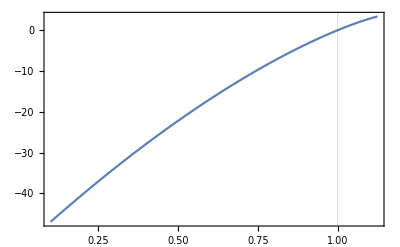

```mathematica
Plot[VbmVs/(3 Mc^4/(16λ)),{λbar,0.1,9/8},GridLines->{{1.},None},Frame->True]
```

Zoomed-in around the critical value λ̄=1:

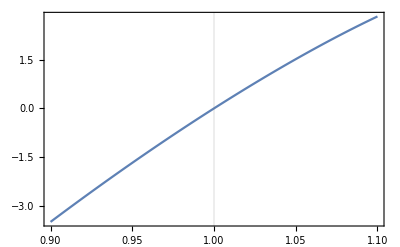

```mathematica
Plot[VbmVs/(3 Mc^4/(16λ)),{λbar,0.9,1.1},GridLines->{{1.},None},Frame->True]
```

Therefore, ΔV≡|V_b-V_s|=sign(λ̄-1)(V_b-V_s) is always positive:

```mathematica
(*ΔV=Abs[VbmVs]//Simplify*)
ΔV=(Sign[λbar-1]VbmVs)//FullSimplify
```

-(3 Mc^4 (27+(9-8 λbar)^(3/2)-36 λbar+8 λbar^2) Sign[-1+λbar])/(16 λ)

## 1.4 Dimensionless expressions

A convenient way to write our equations is in terms of dimensionless quantities. The actual physical quantities can then be obtained from the dimensionless ones by multiplying by the appropriate scales.

We define χ̄≡χ/χ_b and r̄=M·r. We will see that the dimensionality of the potential is given by M^2 χ_b^2:

```mathematica
DimPot=(((Xb^2 M^2)/.PotToMcλbar)//Simplify)
```

-(3 Mc^4 λbar (-3 (3+√(9-8 λbar))+4 λbar))/(2 λ)

Then, the dimensionless potential is:

```mathematica
dimlessV[x_,λbar_]=((V[x*Xb]/(Xb^2 M^2)/.PotToMcλbar)//FullSimplify)
```

(x^2 (-4 x (3+√(9-8 λbar))+x^2 (9+3 √(9-8 λbar)-4 λbar)+8 λbar))/(16 λbar)

The dimensionless potential energy difference between both minima is:

```mathematica
((ΔV/(Xb^2 M^2)/.PotToMcλbar)//FullSimplify)
```

-((3+√(9-8 λbar)-4 λbar) Sign[-1+λbar])/(16 λbar)

```mathematica
(ΔV/(Xb^2 M^2)/.PotToMcλbar)//FullSimplify(*this form looks ugly*)
dimlessΔV[λbar_]=(((((ΔV/(Xb^2 M^2)/.PotToMcλbar)(3-√(9-8 λbar)-4 λbar))//Expand)/(3-√(9-8 λbar)-4 λbar))//FullSimplify)(*multiplying by 1 trick, to express it in a more compact way*)
(*Checking:*)
Assuming[λbar<1,(Abs[ΔV]/(DimPot*dimlessΔV[λbar]))//FullSimplify]
Assuming[λbar>1,(Abs[ΔV]/(DimPot*dimlessΔV[λbar]))//FullSimplify]

dimlessΔV[λbar]
```

-((3+√(9-8 λbar)-4 λbar) Sign[-1+λbar])/(16 λbar)

Abs[-1+λbar]/(-3+√(9-8 λbar)+4 λbar)

1

1

Abs[-1+λbar]/(-3+√(9-8 λbar)+4 λbar)

## 1.5 Potential coefficients M(T) & δ(T)

Let us recall the important functions.

First, the potential:

```mathematica
V[x]
```

(M^2 x^2)/2-(x^3 δ)/3+(x^4 λ)/24

The substitutions in terms of M_c and λ̄:

```mathematica
PotToMcλbar
```

{M→Mc √λbar,δ→1/2 √3 Mc √λ}

Inverting those substitutions:

```mathematica
defMc=Mc->(2 δ)/(√(3 λ));
defλbar=(λbar->M^2/Mc^2)/.defMc;
McλbarToPot={defMc,defλbar}
```

{Mc→(2 δ)/(√3 √λ),λbar→(3 M^2 λ)/(4 δ^2)}

For some theories the M(T) and δ(T) potential coefficients have the following dependence on the temperature and other dimensionless quantities:

```mathematica
PotToCoeffs={M->μ √(T^2-T0^2),δ->A T};
```

where T_0 is the binodal temperature, and μ and A are dimensionless parameters. In terms of these quantities the potential looks like:

```mathematica
V[x]/.PotToCoeffs
```

-1/3 A T x^3+(x^4 λ)/24+1/2 (T^2-T0^2) x^2 μ^2

And M_c and λ̄ are:

```mathematica
McλbarToCoeffs=McλbarToPot/.PotToCoeffs
```

{Mc→(2 A T)/(√3 √λ),λbar→(3 (T^2-T0^2) λ μ^2)/(4 A^2 T^2)}

From here we can find the binodal temperature in terms of the critical temperature T_c, at which λ̄(T_c)=1:

```mathematica
Solve[((λbar/.McλbarToCoeffs)/.T->Tc)==1,T0]//Simplify
Tbinodal=%⟦2⟧
```

{{T0→-(Tc √(-(4 A^2)/λ+3 μ^2))/(√3 μ)},{T0→(Tc √(-(4 A^2)/λ+3 μ^2))/(√3 μ)}}

{T0→(Tc √(-(4 A^2)/λ+3 μ^2))/(√3 μ)}

Clearly the condition for there to be a critical temperature is

```mathematica
cond1[μ_,A_,λ_]=(1-4/3 A^2/(λ μ^2)>0)
```

1-(4 A^2)/(3 λ μ^2)>0

The spinodal temperature, on the other hand, is when λ̄=9/8 and the second minimum vanishes:

```mathematica
Solve[((λbar/.McλbarToCoeffs)/.T->Ts)==9/8,Ts]//Simplify
Tspinodal=(%⟦2⟧/.Tbinodal)//FullSimplify
```

{{Ts→-(T0 μ)/(√(-(3 A^2)/(2 λ)+μ^2))},{Ts→(T0 μ)/(√(-(3 A^2)/(2 λ)+μ^2))}}

{Ts→Tc/(√(1+A^2/(8 A^2-6 λ μ^2)))}

This occurs for parameter values that satisfy the following condition

```mathematica
cond2[μ_,A_,λ_]=(1+A^2/(8 A^2-6 λ μ^2)>0)
```

1+A^2/(8 A^2-6 λ μ^2)>0

We hereby define some functions of the coefficients of the potential that allow us to perform error handling whenever we stray from the physical parameter space.

```mathematica
noCritTemp[coeffs_] := If[cond1[coeffs⟦1⟧, coeffs⟦2⟧, coeffs⟦3⟧], None, 
   Message[noCritTemp::ParameterSpace, coeffs]; Abort[]]

noCritTemp::ParameterSpace = "The parameters {μ,A,λ}=`1` in the potential do not allow for a critical temperature, nor a first order phase transition.";
```

Finally, this leads to the updated rules, in terms of {T, T_c, μ, A}:

```mathematica
McλbarToCoeffs=((McλbarToCoeffs/.Tbinodal)//FullSimplify)
PotToCoeffs=((PotToCoeffs/.Tbinodal)//FullSimplify)
```

{Mc→(2 A T)/(√3 √λ),λbar→(4 Tc^2+(3 (T-Tc) (T+Tc) λ μ^2)/A^2)/(4 T^2)}

{M→√(T^2+1/3 Tc^2 (-3+(4 A^2)/(λ μ^2))) μ,δ→A T}

We can also write T in terms of λ̄ for a given set of parameters

```mathematica
(Solve[((λbar/.McλbarToCoeffs)/.T->√T2)==λbar,T2]//Flatten)
TToλbar={T->Sqrt[T2/.%]//Simplify}
```

{T2→(Tc^2 (4 A^2-3 λ μ^2))/(4 A^2 λbar-3 λ μ^2)}

{T→Tc √((4 A^2-3 λ μ^2)/(4 A^2 λbar-3 λ μ^2))}

And therefore M_c in terms of λ̄:

```mathematica
((Mc/.McλbarToCoeffs)/.TToλbar)//FullSimplify
McToλbar={Mc->%}
```

2 A Tc √((4 A^2-3 λ μ^2)/(12 A^2 λ λbar-9 λ^2 μ^2))

{Mc→2 A Tc √((4 A^2-3 λ μ^2)/(12 A^2 λ λbar-9 λ^2 μ^2))}

The variable Δ≡4/3 A^2/(λ μ^2) is very useful, since Δ=0 corresponds to no cubic term (and thus no broken phase), whereas Δ=1 corresponds to the 1PT condition not being satisfied, and Δ=8/9 to the spinodal temperature going to T_s→∞:

```mathematica
ARule={A->(√3)/2 √λ μ √Δ}
cond1[μ,(A/.ARule/.Δ->#),λ]&/@{0,0.5,0.99,1}
cond2[μ,(A/.ARule/.Δ->#),λ]&/@{0,0.5,8/9,1}
Normal@Series[((Ts/Tc/.Tspinodal)/.ARule)/.Δ->8/9-ϵ,{ϵ,0,0}]
```

{A→1/2 √3 √Δ √λ μ}

{True,True,True,False}

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

{True,True,False,ComplexInfinity>0}

(2 √2)/(9 √ϵ)

Indeed, we can make T_s arbitrarily large by fine-tuning Δ to be as close to 8/9 as desired; or we can get rid of T_s altogether for Δ∈[8/9,1]:

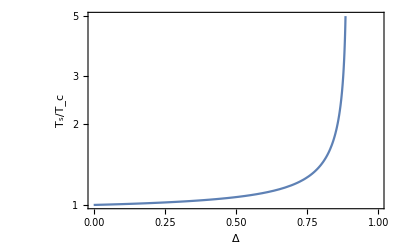

```mathematica
(Ts/Tc/.Tspinodal)/.ARule;
LogPlot[%,{Δ,0,1},GridLines->{{8/9},None},PlotRange->{{0,1},{1,5}},Frame->True,FrameLabel->{"Δ","T_s/T_c"}]
```

For future reference, we compute (d λ̄)/dT, (d λ̄)/(d ln T), (d^2 λ̄)/(d ln T^2), (d ln λ̄)/(d ln T), and (d^2 ln λ̄)/(d ln T^2):

```mathematica
dλdT=(D[(λbar/.McλbarToCoeffs),T]//Simplify)
```

(Tc^2 (-4 A^2+3 λ μ^2))/(2 A^2 T^3)

```mathematica
dλdlnT=dλdT*T
```

(Tc^2 (-4 A^2+3 λ μ^2))/(2 A^2 T^2)

```mathematica
d2λdlnT2=(T*D[dλdlnT,T])//Simplify
```

(Tc^2 (4 A^2-3 λ μ^2))/(A^2 T^2)

```mathematica
dlnλdlnT=(T*D[Log[(λbar/.McλbarToCoeffs)],T]//Simplify)
```

(2 Tc^2 (-4 A^2+3 λ μ^2))/(4 A^2 Tc^2+3 (T^2-Tc^2) λ μ^2)

```mathematica
d2lnλdlnT2=(T*D[dlnλdlnT,T])//Simplify
```

-(12 T^2 Tc^2 λ μ^2 (-4 A^2+3 λ μ^2))/((4 A^2 Tc^2+3 (T^2-Tc^2) λ μ^2)^2)

## 2. Critical Bubble

The critical bubble is the profile for χ_bubble(x)≡χ_bub that corresponds to a stationary solution interpolating between the two minima χ=constant minima (i.e. χ_s & χ_b), and are solutions to the stationary equation for the Euclidean action (S_E), which can be written in terms of the energy of the critical bubble, E_T:

S_E[χ] = E_T[χ]/T=T^-1∫d^3 x  1/2(∇χ)^2+ V_T(χ)

δE_T[χ]/δχ=0   ⇒   -∇^2 χ+(∂V_T(χ))/(∂χ)=0

Note that we will be dealing with spherically-symmetric, time-independent expressions, so this equation reduces to:

-1/r^2 d/dr(r^2 dχ_bub/dr)+V_T'(χ_bub)=0

The dimensionality of this equation is then M^2 χ_b. Dividing the whole expression by this dimension (M^2 χ_b) allows us to find its dimensionless form, which we will use in the next section. On the other hand, the dimensionality of the E_T energy is χ_b^2/M, and thus the action has a prefactor P_S≡χ_b^2/(M T).

This prefactor can be rewritten in terms of λ̄. It, and its first and second derivatives w.r.t. λ̄, are given by:

```mathematica
PS=((Xb^2/(M T)/.PotToCoeffs)/.TToλbar)//FullSimplify
dPSdλ=(D[PS,λbar])//FullSimplify
d2PSdλ2=(D[PS,{λbar,2}])//FullSimplify
```

(√3 A (9+3 √(9-8 λbar)-4 λbar))/(√(λ^3 λbar))

-(√3 A (9 (3+√(9-8 λbar))+4 √(9-8 λbar) λbar))/(2 λbar √(λ^3 (9-8 λbar) λbar))

-((√3 A (-243 (3+√(9-8 λbar))+4 λbar (216+45 √(9-8 λbar)+8 √(9-8 λbar) λbar)))/(4 (λ (9-8 λbar))^(3/2) λbar^(5/2)))

## 2.1 Differential Equation

The differential equation is:

-1/r^2 d/dr(r^2 dχ_bub/dr)+V_T'(χ_bub)=0,

which has dimensionality M^2 χ_b. Dividing the whole expression by this dimension (M^2 χ_b) allows us to find its dimensionless form.

The term with the derivative in the potential is:

```mathematica
dimlessVprime[x_,λbar_]=Collect[((V'[x*Xb]/(M^2 Xb))/.PotToMcλbar)//FullSimplify,x]
```

x+(x^2 (-9 √λ-3 √(λ (9-8 λbar))))/(4 √λ λbar)+(x^3 (9 √λ+3 √(λ (9-8 λbar))-4 √λ λbar))/(4 √λ λbar)

In terms of these dimensionless quantities, the bubble solution satisfies the following boundary conditions:

χ̄(r̄→∞)≡(χ̄)_ini  is the initial value of the scalar field χ̄ in the phase transition: (χ̄)_ini=(χ̄)_s=0 ((χ̄)_ini=(χ̄)_b=1) for a cold/subcritical PT (hot/supercritical PT)
χ̄(r̄=0)≡(χ̄)_fin is the final value of the scalar field χ̄ in the phase transition: close to (χ̄)_fin=(χ̄)_b=1 ((χ̄)_fin=(χ̄)_s=0) for a cold/subcritical PT (hot/supercritical PT).

Recall that whether we have a hot (supercritical)/cold (subcritical) phase transition depends on the value of λ̄ (≷1), and thus whether we tunnel from the broken to the symmetric phase, or vice versa.

In terms of these dimensionless quantities, the energy in the critical bubble is given by:

E_T[χ_bub]=∫d^3 x  1/2(∇χ_bub)^2+ V_T(χ_bub) = χ_b^2/M 4π ∫d r̄ (r̄)^2 ( 1/2((d(χ̄)_bub)/(d r̄))^2+(V̄)_T((χ̄)_bub))

with χ_bub=χ_b(χ̄)_bub and  (V̄)_T(χ̄)=(V_T(χ̄ χ_b))/(χ_b^2 M^2).

As we will see more clearly in the thin wall approximation, this expression is formally infinite. However, what the physics depends on is the (finite) difference between the energies of the initial constant-χ configuration ((χ̄)_ini) and the bubble (χ̄)_bub configuration. This is called the critical energy, and is given by:

E_c≡E_T[χ_bub]-E_T[χ_ini].

Finally, the dimensionless critical bubble equation is:

(d^2(χ̄)_bub)/(d(r̄)^2)+2/(r̄)(d(χ̄)_bub)/(d r̄)-(V̄)_T'((χ̄)_bub)=0

```mathematica
CritEqLHS[λbar_]=Hold[(r*D[χ[r],{r,2}]+2*D[χ[r],{r,1}]-r*dimlessVprime[χ[r],λbar])];
CritEq[λbar_]=(CritEqLHS[λbar]==0)
```

Hold[r ∂_{r,2} χ[r]+2 ∂_{r,1} χ[r]-r dimlessVprime[χ[r],λbar]]==0

## 2.2 Analytic solution: thin wall approximation

In the thin wall approximation (twa) ϵ≡ΔV/V_m<<1, which means that the gain in the vacuum energy from the bubble (~ΔV·R^3∝ϵ·R^3), only becomes larger than the energy from the bubble surface (~R^2) for a large bubble radius R, much larger than the thickness of the bubble wall.

One can show that in the twa χ'(r)^2 = 2 V_T(χ), and that the (dimensionless, factoring out χ_b^2/M) critical energy can be written as:

(Ē)_c=(Ē)_T[(χ̄)_bub]-(Ē)_T[(χ̄)_ini]=[(4π)/3(R̄)_c^3(V̄)_T((χ̄)_fin)+4π (R̄)_c^2 σ̄+(4π)/3 (V̄)_T((χ̄)_ini)(∞^3-(R̄)_c^3)]-(4π)/3 (V̄)_T((χ̄)_ini)∞^3=-(4π)/3(R̄)_c^3 Δ(V̄)_T+4π (R̄)_c^2 σ̄ ,

where R_c is the critical radius, and we have split the contributions to the energy in three parts: the inside (r̄<(R̄)_c), the surface (r̄≈(R̄)_c), and the outside (r̄>(R̄)_c). The (infinite) energy from the constant-χ initial configuration cancels out the (infinite) part from the energy of the critical bubble, as promised. What we are left with is a term from the difference ΔV̄≡V̄((χ̄)_ini)-V̄((χ̄)_fin)>0 between the two minima, as well as the surface term.

The contribution from the surface depends on the surface tension σ̄, given by:

σ̄≈|∫_((χ̄)_ini)^((χ̄)_fin) d χ̄ √(2 (V̄)_T(χ̄))|=∫_0^1 d χ̄ √(2 (V̄)_T(χ̄))

Since in the twa λ̄≈1, then:

```mathematica
(*approximate expression for the (dimensionless) potential in the twa*)
dimlessV[x,1]//FullSimplify
```

1/2 (-1+x)^2 x^2

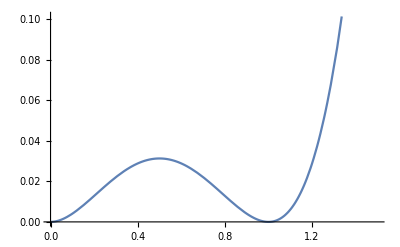

```mathematica
Plot[dimlessV[x,1],{x,0.,1.5}]
```

### Surface tension σ

```mathematica
(*the dimensionless surface tension*)
σ=Integrate[√(2*dimlessV[x,1]),{x,0,1}]
```

1/6

Its dimensionality is χ_b^2 M, as can be seen both from the fact that the dimensionality of E_c is χ_b^2/M and that of R_c is 1/M, and from the fact that the dimensionality of V_T is M^2 χ_b^2 and that of χ is χ_b. As a sanity check then, let us consider the dimensionful surface tension in the twa (λ̄≈1, or T≈T_c):

```mathematica
(*the dimensionful surface tension*)
dimSurfTens=((σ*Xb^2*M)/.PotToMcλbar)//FullSimplify

(Normal@Series[dimSurfTens/.McλbarToCoeffs,{T,Tc,0}])//FullSimplify
Clear[dimSurfTens,tempRule]
```

(Mc^3 (9+3 √(9-8 λbar)-4 λbar) √λbar)/(4 λ)

(16 A^3 Tc^3)/(3 √3 λ^(5/2))

Compare with Andrew Linde’s Eq. (3.16) (or taking δ=α T, Eq. (3.22)), and converting to our parameters, in the T≈T_c limit

```mathematica
((2 √2 δ^3)/(3^4 λL^(5/2))/.{δ->A*Tc,λL->λ/6})
```

(16 A^3 Tc^3)/(3 √3 λ^(5/2))

### Critical radius R_c

Moving on, we can calculate the critical bubble radius in the twa by realizing that, if the bubble is an extremum of (Ē)_c, then (R̄)_c is such that (∂(Ē)_c)/(∂(R̄)_c)=0:

```mathematica
Solve[D[-(4π)/3*dimlessΔV[λbar]*rc^3+4π rc^2 σ,rc]==0,rc]//Expand//Simplify//FullSimplify
Rctwa[λbar_]=(rc/.%⟦2⟧)(*the critical radius*)
```

{{rc→0},{rc→(-3+√(9-8 λbar)+4 λbar)/(3 Abs[-1+λbar])}}

(-3+√(9-8 λbar)+4 λbar)/(3 Abs[-1+λbar])

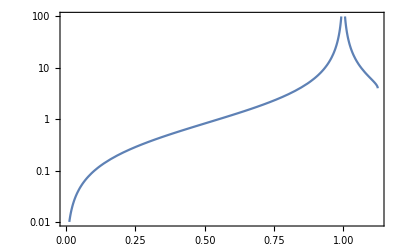

```mathematica
LogPlot[Rctwa[λbar],{λbar,0,9/8},PlotRange->{0.01,100},Frame->True]
```

With the dimensions M^-1:

```mathematica
Assuming[λbar<1&&T<Tc,(((Rctwa[λbar]/M/.PotToMcλbar))/.McλbarToCoeffs)//FullSimplify];
Normal@Series[%,{T,Tc,-1}]
```

(2 A √λ)/(√3 (T-Tc) (4 A^2-3 λ μ^2))

As a sanity check let us compare with Linde’s Eq. (3.18) (or Eq. (3.24))

```mathematica
(Assuming[λbar<1,(((2^(5/2)δ^3)/(3^4 λL^(5/2)ε)/.{δ->A*T,λL->λ/6,ε->Abs[ΔV]})//Simplify)]/.McλbarToCoeffs)//Simplify;
Normal@Series[%,{T,Tc,-1}]
```

(2 A √λ)/(√3 (T-Tc) (4 A^2-3 λ μ^2))

### Critical energy E_c

The bubble’s critical energy is then:

```mathematica
Ectwa[λbar_]=(-(4π)/3*dimlessΔV[λbar]*Rctwa[λbar]^3+4π Rctwa[λbar]^2 σ)//FullSimplify
```

(2 π (-3+√(9-8 λbar)+4 λbar)^2)/(81 (-1+λbar)^2)

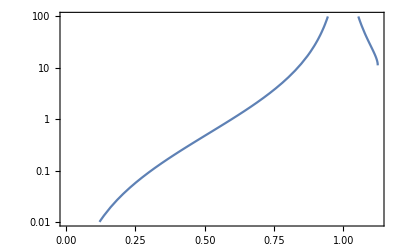

```mathematica
LogPlot[Ectwa[λbar],{λbar,0,9/8},PlotRange->{0.01,100},Frame->True]
```

With the dimensions χ_b^2/M

```mathematica
Assuming[λbar<1&&T<Tc,((Ectwa[λbar]*Xb^2/M/.PotToMcλbar)/.McλbarToCoeffs)//FullSimplify];
Normal@Series[%,{T,Tc,-2}]
```

(256 A^5 π Tc^3)/(27 √3 (T-Tc)^2 λ^(3/2) (4 A^2-3 λ μ^2)^2)

Which we can compare to Linde’s Eq. (3.18) (or Eq. 3.23)

```mathematica
(Assuming[λbar<1,(((2^(17/2)π*δ^9)/(3^13 λL^(15/2)ε^2)/.{δ->A*T,λL->λ/6,ε->Abs[ΔV]})//Simplify)]/.McλbarToCoeffs)//Simplify;
Normal@Series[%,{T,Tc,-2}]
```

(256 A^5 π Tc^3)/(27 √3 (T-Tc)^2 λ^(3/2) (4 A^2-3 λ μ^2)^2)

Defining the first and second derivatives

```mathematica
dEctwadλ[λbar_]=((D[Ectwa[λbar],λbar])//FullSimplify)(*derivative Subscript[Ē, c]'(λ̄) in thin-wall approximation*)

d2Ectwadλ2[λbar_]=((D[Ectwa[λbar],{λbar,2}])//FullSimplify)(*derivative Subscript[Ē, c]'(λ̄) in thin-wall approximation*)
```

-(8 π (-3+√(9-8 λbar)+4 (3-2 λbar) λbar))/(81 √(9-8 λbar) (-1+λbar)^3)

-((8 π (-5-9 √(9-8 λbar)+4 λbar (-9+2 √(9-8 λbar)+2 (9-4 λbar) λbar)))/(27 (9-8 λbar)^(3/2) (-1+λbar)^4))

### Bubble profile χ_bub(r)

It can be shown that in the twa

(d χ̄)/(d r̄)≈sign(λ̄-1)·√(2(V̄)_T(χ̄)),

(i.e. positive/negative derivatives for hot (supercritical)/cold (subcritical) PT). From here we can solve for r̄(χ̄):

r̄≈|∫_((χ̄)_ini)^(χ̄) (dχ̄')/(√(2 (V̄)_T(χ̄')))|

and then invert the equation.

```mathematica
Assuming[1>x>0,1/(√(2*dimlessV[x,1]))//Simplify](*|dr/dχ|; the choice of sign depends on whether λ̄-1>0 (+) or <0 (-)*)
Δrtwa[χlo_,χhi_]=Assuming[0<χlo<χhi<1,Integrate[%,{x,χlo,χhi}]](*Δr change in r due to a change in χ*)

χfintwa[λbar_]=Assuming[9/8>λbar>0&&Im[1/(-1+λbar)]==0&&λbar≠1,((HeavisideTheta[1-λbar]+Sign[λbar-1]*dx)/.Assuming[9/8>λbar>0&&Im[1/(-1+λbar)]==0&&λbar≠1,Solve[Sign[λbar-1] Δrtwa[HeavisideTheta[1-λbar]+Sign[λbar-1]*dx,1/2]==Rctwa[λbar],dx]//FullSimplify]⟦1⟧)//FullSimplify](*final value of χ from PT (namely, χ(r->0)) for a given critical radius Subscript[R, c](λ̄)*)

χtwa[r_,λbar_]=Assuming[9/8>λbar>0&&Im[1/Sign[-1+λbar]]==0&&λbar≠1&&r>0,(χ/.Solve[(Sign[λbar-1]*Δrtwa[χfintwa[λbar],χ]==r),χ]⟦1⟧//Simplify)//FullSimplify](*the bubble profile in the twa*)
```

1/(x-x^2)

Log[(χhi (-1+χlo))/((-1+χhi) χlo)]

ⅇ^(1/(-1+λbar))/(ⅇ^(1/(-1+λbar))+ⅇ^((√(9-8 λbar)+4 λbar)/(3 (-1+λbar))))

1/(1+ⅇ^((-3+√(9-8 λbar)+4 λbar-3 r Abs[-1+λbar])/(3 (-1+λbar))))

### Wall thickness l_w

We can define the wall thickness l_w in terms of the change in radius r upon a certain change Δ χ̄ in the scalar field, centered around half the field-distance χ_*=|(χ_fin-χ_ini)/2|:

(l̄)_w≡Δ r̄=∫_((1-Δ χ̄)/2)^((1+Δ χ̄)/2) (d χ̄)/(dχ̄/d r̄) =∫_((1+Δ χ̄)/2)^((1+Δ χ̄)/2) (d χ̄)/(√(2 (V̄)_T(χ̄)))

```mathematica
thickness[Δχ_]=Assuming[1>Δχ>0,Δrtwa[(1-Δχ)/2,(1+Δχ)/2]//FullSimplify](*wall thickness for arbitrary change Δ χ̄ in χ̄ around 1/2*)
```

Log[(1+Δχ)^2/(-1+Δχ)^2]

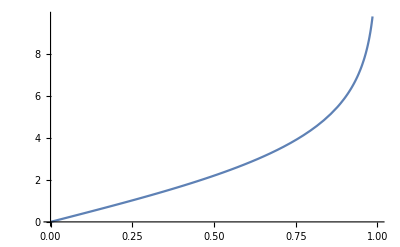

```mathematica
Plot[thickness[Δχ],{Δχ,0,1}](*plot of thicknes as a function of the change Δ χ̄ in χ̄ around 1/2*)
```

Since what where does the wall start and ends is an arbitrary definition, we simply take its value to be the thickness for changes of Δ χ̄=0.9 around 1/2:

```mathematica
lw=thickness[9/10](*bubble thickness*)
%//N
```

Log[361]

5.88888

Alternative definitions below:

```mathematica
Integrate[thickness[Δχ],{Δχ,0,1}](*average thickness*)
√Integrate[thickness[Δχ]^2,{Δχ,0,1}](*RMS thickness*)
```

Log[16]

(2 π)/(√3)

### Miscellaneous

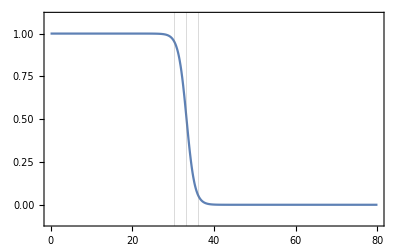

```mathematica
lb=0.98;
Plot[{χtwa[r,lb]},{r,0,80},PlotRange->{0-0.1,1.1},Frame->True,GridLines->{{Rctwa[lb],Rctwa[lb]-lw/2,Rctwa[lb]+lw/2}}]
Clear[lb]
```

## 2.3 Semi-analytical solution: thick wall approximation

The point of this section is to move beyond the thin wall approximation and derive semi-analytic expressions for the (dimensionless) critical bubble energy (Ē)_c(λ̄) with which we can complement the numerical runs.

We will then later recycle these results to give approximate expressions for the Euclidean action for all values of λ̄, which will be useful when studying the gravitational waves generated in 1PT.

### Numerical action

In the thick wall approximation, where λ̄<<1 (or λ̄>>1), we will manipulate the potential V̄(χ̄) in such a way that we will be able to approximate one of its coefficients to be close to 0, thus getting rid of one of its terms in its field variable χ̄. We will then manipulate the field variable and the bubble radius in such a way as to render the bubble equation exactly dimensionless and without any parameters. This is all inspired by Linde’s treatment of this thick-wall limit.

Anticipating this magic, we will find that the bubble equation can be written in terms of a new field variable z, whose bubble configuration satisfies:

(d^2 z_bub)/dρ^2+2/ρ dz_bub/dρ=z_bub-3/2 z_bub^2

for a thick-wall potential V(z)=1/2 z^2(1-z), and the dimensionless action

(S̄)_E≡4π ∫dρ ρ^2 [ 1/2(dz_bub/dρ)^2+1/2 z_bub^2(1-z_bub)]≈19.4.

The solution and (dimensionless) bubble energy are then given by:

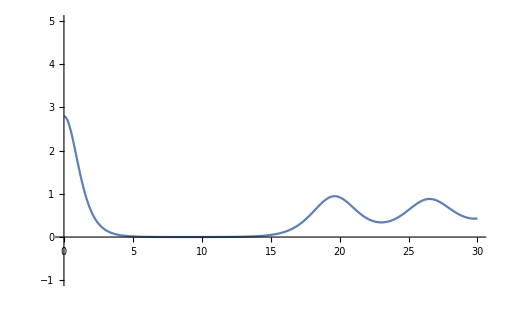

19.4047

```mathematica
sol=NDSolve[{z''[r]+2/r z'[r]==z[r]-3/2 z[r]^2,z'[0.01]==0,z[0.01]==2.7940},z[r],{r,0.01,30}]//Flatten;
Plot[z[r]/.sol,{r,0.01,30},PlotRange->{-1,5}]

1/2(D[(z[r]/.sol),r])^2+1/2 z^2(1-z)/.z->(z[r]/.sol);
SThickNum=NIntegrate[4π*r^2*%,{r,0.01,10}]

Clear[sol]
```

### Cold (subcritical) 1PT (λ̄<1)

```mathematica
Clear[tempPot,λbarTabs,tempTab,tempCoeffs,tempZeros,WPot,tempTab2,tempTab3,VandW,ith]
```

Let’s start by looking at V̄(χ̄) and its polynomial coefficients:

x^2/2-(x^3 (3+√(9-8 λbar)))/(4 λbar)+(x^4 (9+3 √(9-8 λbar)-4 λbar))/(16 λbar)

8/81

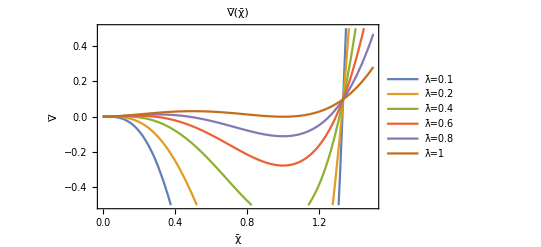

{0,0,1/2,(-3-√(9-8 λbar))/(4 λbar),(9+3 √(9-8 λbar)-4 λbar)/(16 λbar)}

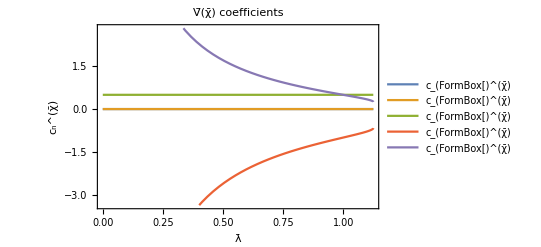

```mathematica
tempPot=Collect[dimlessV[x,λbar],x]
(tempPot/.x->4/3)//Simplify

λbarTabs={0.1,0.2,0.4,0.6,0.8,1};
tempTab=Table[tempPot,{λbar,λbarTabs}];
Plot[tempTab,{x,0,1.5},PlotRange->{-0.5,0.5},Frame->True,FrameLabel->{"χ̄","V̄"},PlotLegends->Table[StringForm["λ̄=``",val],{val,λbarTabs}],PlotLabel->"V̄(χ̄)"]

tempCoeffs=CoefficientList[tempPot,x]
Plot[tempCoeffs,{λbar,0,9/8},Frame->True,FrameLabel->{"λ̄","c_n^(χ̄)"},PlotLegends->Table[StringForm["c_(``)^(χ̄)",n],{n,0,4}],PlotLabel->"V̄(χ̄) coefficients"]
```

Now let us look at the zeros of the potential, which will allow us to identify what values of x should the bubble reach in order to trigger the 1PT:

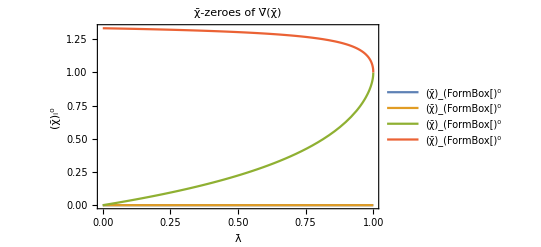

```mathematica
tempZeros=(x/.#&)/@Solve[tempPot==0,x];
Plot[tempZeros,{λbar,0,1},Frame->True,FrameLabel->{"λ̄","(χ̄)_i^0"},PlotLegends->Table[StringForm["(χ̄)_(``)^0",i],{i,1,4}],PlotLabel->"χ̄-zeroes of V̄(χ̄)"]
```

Two zeros are at χ̄=0, and the third one, (χ̄)_3^0, is smaller than 1 ((χ̄)_b≡1 is the broken minimum of the potential), which thus corresponds roughly to the χ̄ field value the bubble needs to reach in order to achieve the 1PT. In the thick wall approximation the potential broken minimum (χ̄)_b is very deep. This means that we can construct an approximate potential W(χ̄)=a (χ̄)^2(χ̄-(χ̄)_3^0)≈V̄(χ̄) that has approximately the same shape as the exact potential V̄(χ̄) for χ̄<(χ̄)_3^0.

To do this we just demand W''(0)=V̄''(0), or -2a (χ̄)_3^0=2 c_2^(χ̄) ⇒ a=-c_2^(χ̄)/x_3^0.

```mathematica
WPot=a*x^2*(x-tempZeros⟦3⟧);
(Solve[(D[WPot,{x,2}]/.x->0)==(D[tempPot,{x,2}]/.x->0),a]//Flatten)//FullSimplify

WPot=Collect[(WPot/.%)//FullSimplify,x];
FullSimplify@#&/@(CoefficientList[WPot,x]);
WPot=Collect[Sum[%⟦n+1⟧*x^n,{n,0,(Length@%)-1}],x]
```

{a→-1/(8 λbar)(3+√(9-8 λbar)+√2 √(-(9+3 √(9-8 λbar)-4 λbar) (-1+λbar)))}

x^2/2+1/(8 λbar)x^3 (-3-√(9-8 λbar)-√2 √(-(9+3 √(9-8 λbar)-4 λbar) (-1+λbar)))

We can now compare the exact potential V̄(χ̄), the approximate potential W(χ̄), and a potential (V̄)_trun(χ̄) truncated to 𝒪((χ̄)^3), i.e. where we have simply dropped the 𝒪((χ̄)^4) term:

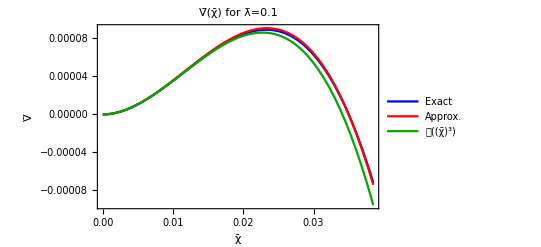

```mathematica
tempTab2=Table[WPot,{λbar,λbarTabs}];
tempTab3=Table[Sum[tempCoeffs⟦n+1⟧*x^n*If[n≠4,1,0],{n,0,4}],{λbar,λbarTabs}];

VandW=Transpose[{tempTab}~Join~{tempTab2}~Join~{tempTab3}];
ith=1;
VandW⟦ith⟧;
Plot[%,{x,0,1.1*(tempZeros⟦3⟧/.λbar->λbarTabs⟦ith⟧)},PlotRange->{{0,1.1*(tempZeros⟦3⟧/.λbar->λbarTabs⟦ith⟧)},Full},Frame->True,FrameLabel->{"χ̄","V̄"},PlotLegends->{"Exact","Approx.","𝒪((χ̄)^3)"},PlotLabel->StringForm["V̄(χ̄) for λ̄=``",λbarTabs⟦ith⟧],PlotStyle->{Blue,Red,Darker@Green}]
```

We are now ready to manipulate the bubble equation.

Note that we have V̄(χ̄)≈W(χ̄)=c_2(χ̄)^2-c_3(χ̄)^3 (where, crucially, c_i are no longer the same coefficients in V̄(χ̄)). Changing variables ρ=r̄ √(2 c_2) and χ̄=c_2/c_3 z we get:

V̄(χ̄)≈W(z)=c_2^3/c_3^2 z^2(1-z), and thus

E_T[χ_bub]=χ_b^2/M 4π ∫d r̄ (r̄)^2 ( 1/2((d(χ̄)_bub)/(d r̄))^2+(V̄)_T((χ̄)_bub))≈χ_b^2/M(c_2^3/(2 c_3^4))^(1/2)4π ∫dρ ρ^2 [ 1/2(dz_bub/dρ)^2+1/2 z_bub^2(1-z_bub)]=χ_b^2/M(c_2^3/(2 c_3^4))^(1/2)(S̄)_E,

with (S̄)_E≈19.4 as promised. We can then compare to the full solution:

310.475 √(1/(3+√(9-8 λbar)+√2 √(-(9+3 √(9-8 λbar)-4 λbar) (-1+λbar)))^4) λbar^2

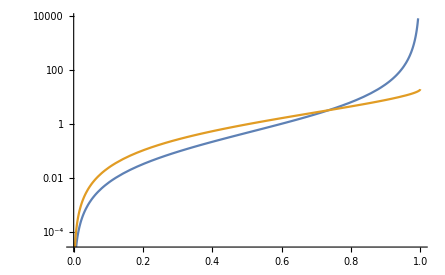

```mathematica
CoefficientList[WPot,x];
EcThick["cold"][λbar_]=((√((%⟦2+1⟧)^3/(2*(%⟦3+1⟧)^4)))*SThickNum)//FullSimplify
LogPlot[{Ectwa[λbar],EcThick["cold"][λbar]},{λbar,0,1}]
```

Defining the derivatives

```mathematica
dEcThickdλ["cold"][λbar_]=D[EcThick["cold"][λbar],λbar]//Simplify;
d2EcThickdλ2["cold"][λbar_]=D[dEcThickdλ["cold"][λbar],λbar]//Simplify;
```

Defining the limiting cases (they will be useful later on)

```mathematica
limEcThick["cold"][λbar_]=(Normal@Series[EcThick["cold"][λbar],{λbar,0,2}])//Simplify
limdEcThick["cold"][λbar_]=(Normal@Series[dEcThickdλ["cold"][λbar],{λbar,0,1}])//Simplify
limd2EcThick["cold"][λbar_]=(Normal@Series[d2EcThickdλ2["cold"][λbar],{λbar,0,0}])//Simplify
```

2.15608 λbar^2

4.31215 λbar

4.31215

### Hot (supercritical) 1PT (λ̄>1)

```mathematica
Clear[tempPot,λbarTabs,tempTab,tempCoeffs,tempZeros,WPot,tempTab2,tempTab3,VandW,ith]
```

Since here we’re interested in (χ̄)_ini=(χ̄)_b=1 (i.e. in generating bubbles of the symmetric phase within the broken phase), we better change variables y≡1-χ̄, and consider the corresponding potential V̄(y)≡V̄(χ̄=1-y) and its coefficients c_n^y for each y^n term:

(y^2 (9+3 √(9-8 λbar)-8 λbar))/(8 λbar)-(3+√(9-8 λbar)-4 λbar)/(16 λbar)+(y^4 (9+3 √(9-8 λbar)-4 λbar))/(16 λbar)+(y^3 (-3-√(9-8 λbar)+2 λbar))/(2 λbar)

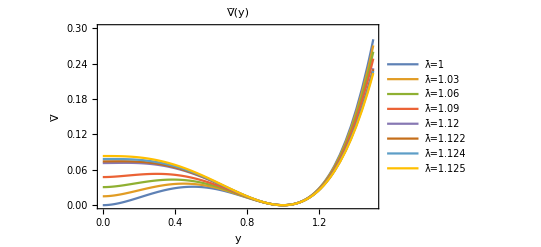

{-(3+√(9-8 λbar)-4 λbar)/(16 λbar),0,(9+3 √(9-8 λbar)-8 λbar)/(8 λbar),(-3-√(9-8 λbar)+2 λbar)/(2 λbar),(9+3 √(9-8 λbar)-4 λbar)/(16 λbar)}

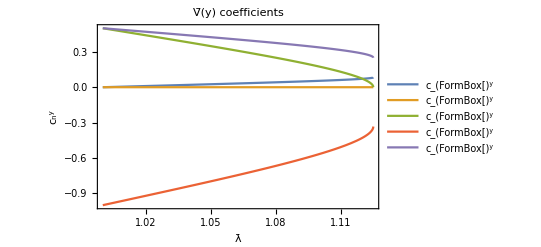

```mathematica
FullSimplify@#&/@(List@@(Collect[dimlessV[1-y,λbar],y]));
tempPot=Collect[Total[%],y]

λbarTabs={1,1.03,1.06,1.09,1.12,1.122,1.124,9./8};
tempTab=Table[tempPot,{λbar,λbarTabs}];
Plot[tempTab,{y,0,1.5},PlotRange->{0,0.3},Frame->True,FrameLabel->{"y","V̄"},PlotLegends->Table[StringForm["λ̄=``",val],{val,λbarTabs}],PlotLabel->"V̄(y)"]

tempCoeffs=CoefficientList[tempPot,y]
Plot[tempCoeffs,{λbar,1,9/8},Frame->True,FrameLabel->{"λ̄","c_n^y"},PlotLegends->Table[StringForm["c_(``)^y",n],{n,0,4}],PlotLabel->"V̄(y) coefficients"]
```

We can further split V̄(y)=(V̄)_0+Ṽ(y) and (V̄)_0≡V̄(0)=c_0^y, where we have simply dropped the constant term, which does not impact the bubble equation (since it involves only V̄'(y)). We will restore this constant term when we come to the point of computing the action.

(y^2 (9+3 √(9-8 λbar)-8 λbar))/(8 λbar)+(y^4 (9+3 √(9-8 λbar)-4 λbar))/(16 λbar)+(y^3 (-3-√(9-8 λbar)+2 λbar))/(2 λbar)

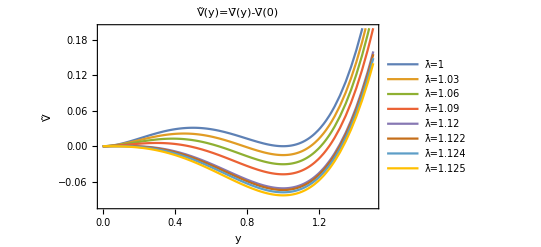

```mathematica
tempPotU=tempPot-CoefficientList[tempPot,y]⟦1⟧

tempTab=Table[tempPotU,{λbar,λbarTabs}];
Plot[tempTab,{y,0,1.5},PlotRange->{-0.1,0.2},Frame->True,FrameLabel->{"y","Ṽ"},PlotLegends->Table[StringForm["λ̄=``",val],{val,λbarTabs}],PlotLabel->"Ṽ(y)=V̄(y)-V̄(0)"]
```

This is not good enough. The whole point of the thick wall approximation is that the second minimum (in this case y=1) is very deep. The depth of the minimum here is finite, and simply given by

```mathematica
(tempPotU/.y->1)//Simplify
%/.λbar->9/8
```

(3+√(9-8 λbar)-4 λbar)/(16 λbar)

-1/12

The culprit here is the way we have split the dimensionful potential into a dimensionful prefactor and a dimensionless potential: V(χ)=χ_b^2 M^2 V̄(χ̄):

```mathematica
(V[χ]/.PotToMcλbar)//FullSimplify;
(DimPot*dimlessV[χ/Xb/.PotToMcλbar,λbar])//FullSimplify;
(%%-%)//FullSimplify
```

0

Note that the dimensionful coefficient is vanishes at λ̄=0, whereas the dimensionless potential V̄(χ̄) blows up there, which means that the potential is deep at χ̄=1 as λ̄→0: exactly the thick wall approximation:

```mathematica
DimPot/.λbar->0
dimlessV[x,0]
(DimPot*dimlessV[x,λbar])/.λbar->0
```

0

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

(27 Mc^4 x^2 (-24 x+18 x^2))/(16 λ)

Thus, if we want a deep potential at y=0 (χ̄=0=(χ̄)_s), we better split the full potential using V(χ)=χ_b^2 M_b^2 Ū(χ̄)=(χ_b^2 M^2)(M_b^2/M^2)Ū(χ̄), where M_b^2 is the mass of χ at the broken minimum χ_b. Therefore Ū(x)=(M^2/M_b^2)V̄(x)

```mathematica
dimlessU[x_,λbar_]=(M^2/Mb^2/.PotToMcλbar)*dimlessV[x,λbar]
dimfulU=(DimPot*Mb^2/M^2/.PotToMcλbar)
((dimfulU*dimlessU[x,λbar])-(DimPot*dimlessV[x,λbar]))//FullSimplify
```

(x^2 (-4 x (3+√(9-8 λbar))+x^2 (9+3 √(9-8 λbar)-4 λbar)+8 λbar))/(4 (9+3 √(9-8 λbar)-8 λbar))

-(3 Mc^4 (9+3 √(9-8 λbar)-8 λbar) (-3 (3+√(9-8 λbar))+4 λbar))/(8 λ)

0

Note that in terms of Ū, rather than V̄, the bubble’s energy, rewritten as an integral over r̃≡r M_b=r̄ M_b/M:

E_T[χ_bub]=χ_b^2/M 4π ∫d r̄ (r̄)^2 ( 1/2((d(χ̄)_bub)/(d r̄))^2+(V̄)_T((χ̄)_bub))=χ_b^2/M_b 4π ∫d r̃ (r̃)^2 ( 1/2(dy_bub/(d r̃))^2+Ū(y_bub))

Plotting U(y):

y^2/2+1/8 (-1+1/(√(9-8 λbar)))+1/8 y^4 (1+3/(√(9-8 λbar)))+(y^3 (9+√(9-8 λbar)-8 λbar))/(2 (-9+8 λbar))

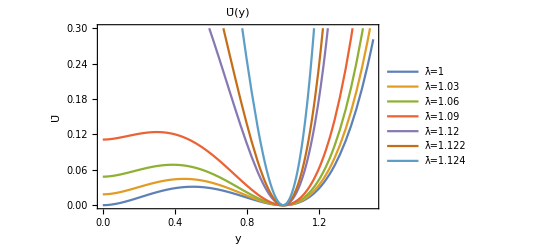

{1/8 (-1+1/(√(9-8 λbar))),0,1/2,(9+√(9-8 λbar)-8 λbar)/(2 (-9+8 λbar)),1/8 (1+3/(√(9-8 λbar)))}

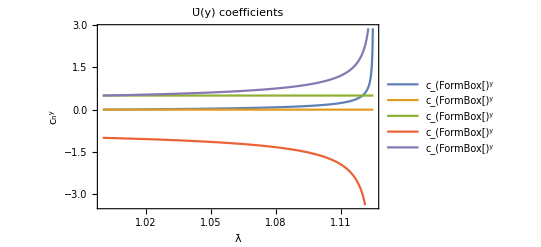

```mathematica
Collect[dimlessU[1-y,λbar],y];
FullSimplify@#&/@(List@@(Collect[dimlessU[1-y,λbar],y]));
tempPot=Collect[Total[%],y]

λbarTabs={1,1.03,1.06,1.09,1.12,1.122,1.124};
tempTab=Table[tempPot,{λbar,λbarTabs}];
Plot[tempTab,{y,0,1.5},PlotRange->{0,0.3},Frame->True,FrameLabel->{"y","Ū"},PlotLegends->Table[StringForm["λ̄=``",val],{val,λbarTabs}],PlotLabel->"Ū(y)"]

tempCoeffs=CoefficientList[tempPot,y]
Plot[tempCoeffs,{λbar,1,9/8},Frame->True,FrameLabel->{"λ̄","c_n^y"},PlotLegends->Table[StringForm["c_(``)^y",n],{n,0,4}],PlotLabel->"Ū(y) coefficients"]
```

Now we can further split Ū(y)=(Ū)_0+U(y) and (Ū)_0≡Ū(0)=c_0^y, where we have simply dropped the constant term, which does not impact the bubble equation (since it involves only Ū'(y)). Note that this coefficient diverges as λ̄→9/8. No matter: we will restore this constant term when we come to the point of computing the action, and we will discover it drops out of all physical quantities.

y^2/2+1/8 y^3 (-4-4/(√(9-8 λbar)))+1/8 y^4 (1+3/(√(9-8 λbar)))

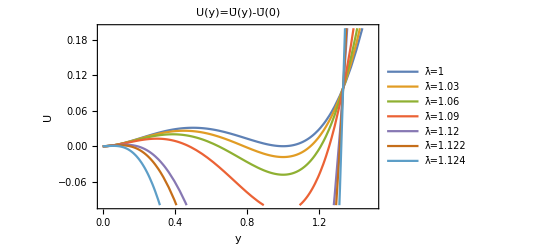

```mathematica
tempPotU=Collect[(tempPot-CoefficientList[tempPot,y]⟦1⟧)//Simplify,y]

tempTab=Table[tempPotU,{λbar,λbarTabs}];
Plot[tempTab,{y,0,1.5},PlotRange->{-0.1,0.2},Frame->True,FrameLabel->{"y","U"},PlotLegends->Table[StringForm["λ̄=``",val],{val,λbarTabs}],PlotLabel->"U(y)=Ū(y)-Ū(0)"]
```

Now let us look at the zeros of the potential U(y), which will allow us to identify what values of y should the bubble reach in order to trigger the 1PT:

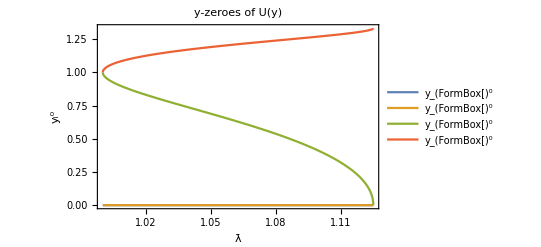

```mathematica
tempZeros=(y/.#&)/@Solve[tempPotU==0,y];
tempZeros=FullSimplify[#]&/@tempZeros;
Plot[tempZeros,{λbar,1,9/8},Frame->True,FrameLabel->{"λ̄","y_i^0"},PlotLegends->Table[StringForm["y_(``)^0",i],{i,1,4}],PlotLabel->"y-zeroes of U(y)"]
```

Two zeros are at y=0, and the third one, y_3^0, is smaller than 1 (y_3^0=1 corresponds to χ̄=1-y_3^0=0=(χ̄)_s, the symmetric minimum of the potential), which thus corresponds roughly to the y field value the bubble needs to reach in order to achieve the 1PT from broken-to-symmetric. In the thick wall approximation the potential symmetric minimum (χ̄)_s is very deep (w.r.t. (χ̄)_b); in other words, Ū(y=0)=(Ū)_0 is very high. This means that we can construct an approximate potential W(y)=a y^2(y-y_3^0) that has approximately the same shape as the exact potential U(y) for y<y_3^0.

To do this we just demand W''(0)=U''(0):

```mathematica
WPot=a*y^2*(y-tempZeros⟦3⟧);
(Solve[(D[WPot,{y,2}]/.y->0)==(D[tempPotU,{y,2}]/.y->0),a]//Flatten)//FullSimplify
WPot=Collect[(WPot/.%)//FullSimplify,y];

FullSimplify@#&/@(CoefficientList[WPot,y]);
WPot=Collect[Sum[%⟦n+1⟧*y^n,{n,0,(Length@%)-1}],y]
```

{a→-(3+√(9-8 λbar))/(4-4 √(1-√(9-8 λbar))+4 √(9-8 λbar))}

y^2/2+(y^3 (-3-√(9-8 λbar)))/(4-4 √(1-√(9-8 λbar))+4 √(9-8 λbar))

We can now compare the exact potential U(y), the approximate potential W(y), and a potential U_trun(y) truncated to 𝒪(y^3), i.e. where we have simply dropped the 𝒪(y^4) term:

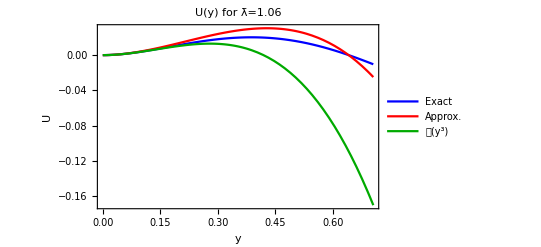

```mathematica
tempTab2=Table[WPot,{λbar,λbarTabs}];
tempTab3=Table[Sum[tempCoeffs⟦n+1⟧*y^n*If[n≠4,1,0],{n,0,4}]-tempCoeffs⟦1⟧,{λbar,λbarTabs}];

UandW=Transpose[{tempTab}~Join~{tempTab2}~Join~{tempTab3}];
ith=3;
UandW⟦ith⟧;
Plot[%,{y,0,1.1*(tempZeros⟦3⟧/.λbar->λbarTabs⟦ith⟧)},PlotRange->{{0,1.1*(tempZeros⟦3⟧/.λbar->λbarTabs⟦ith⟧)},Full},Frame->True,FrameLabel->{"y","U"},PlotLegends->{"Exact","Approx.","𝒪(y^3)"},PlotLabel->StringForm["U(y) for λ̄=``",λbarTabs⟦ith⟧],PlotStyle->{Blue,Red,Darker@Green}]
```

We are now ready to manipulate the bubble equation.

Note that we have Ū(y)=(Ū)_0+U(y)≈(Ū)_0+W(y)=(Ū)_0+c_2 y^2-c_3 y^3 (where, crucially, c_i are no longer the same coefficients in V̄(y)). Changing variables ρ=r̃ √(2 c_2) and y=c_2/c_3 z we get:

Ū(y)=(Ū)_0+U(y)≈(Ū)_0+W(z)=(Ū)_0+c_2^3/c_3^2 z^2(1-z)=(2 c_2^3)/c_3^2((c_3^2/(2 c_2^3))(Ū)_0+1/2 z^2(1-z)).

and thus

E_T[χ_bub]=χ_b^2/M_b 4π ∫d r̃ (r̃)^2 ( 1/2(dy_bub/(d r̃))^2+Ū(y_bub))=χ_b^2/M_b 4π ∫d r̃ (r̃)^2 ( 1/2(dy_bub/(d r̃))^2+(Ū)_0+U(y_bub))≈χ_b^2/M_b(c_2^3/(2 c_3^4))^(1/2)4π ∫dρ ρ^2 [ 1/2(dz/dρ)^2+1/2 z^2(1-z)+(c_3^2/(2 c_2^3))(Ū)_0]=χ_b^2/M×M/M_b(c_2^3/(2 c_3^4))^(1/2)[(S̄)_E+(c_3^2/(2 c_2^3))(Ū)_0×(4π)/3∞^3],

where we have restored the χ_b^2/M prefactor, (S̄)_E≈19.4, and there is an infinite contribution from the zero-point energy at the metastable broken minimum, (Ū)_0. However, recall that we are only interested in the (energy) difference between the bubble configuration and the initial, metastable configuration. The latter also has this zero-point energy contribution, and thus they cancel out in the difference. We can then compare to the full solution:

(155.237 √(((1-√(1-√(9-8 λbar))+√(9-8 λbar))^4 λbar)/(9+3 √(9-8 λbar)-8 λbar)))/(3.+√(9-8 λbar))^2

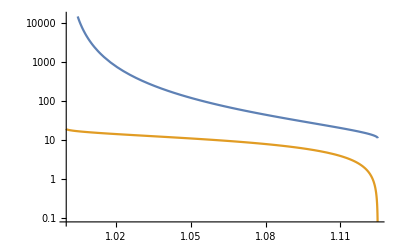

```mathematica
CoefficientList[WPot,y];
EcThick["hot"][λbar_]=((M/Mb/.PotToMcλbar)(√((%⟦2+1⟧)^3/(2*(%⟦3+1⟧)^4))//FullSimplify)*SThickNum)//FullSimplify
LogPlot[{Ectwa[λbar],EcThick["hot"][λbar]},{λbar,1,9/8}]
```

Defining the derivatives

```mathematica
dEcThickdλ["hot"][λbar_]=D[EcThick["hot"][λbar],λbar]//Simplify;
d2EcThickdλ2["hot"][λbar_]=D[dEcThickdλ["hot"][λbar],λbar]//Simplify;
```

Defining the limiting cases (they will be useful later on)

```mathematica
limEcThick["hot"][λbar_]=(Assuming[ϵ>0,(Normal@Series[EcThick["hot"][9/8-ϵ],{ϵ,0,1}])]/.ϵ->(9/8-λbar))
limdEcThick["hot"][λbar_]=(Assuming[ϵ>0,(Normal@Series[dEcThickdλ["hot"][9/8-ϵ],{ϵ,0,0}])]/.ϵ->(9/8-λbar))
limd2EcThick["hot"][λbar_]=(Assuming[ϵ>0,(Normal@Series[d2EcThickdλ2["hot"][9/8-ϵ],{ϵ,0,-1}])]/.ϵ->(9/8-λbar))//Chop
```

113.05 (9/8-λbar)^(3/4)

-84.7873/(9/8-λbar)^(1/4)

-21.1968/(9/8-λbar)^(5/4)

```mathematica
Clear[tempPot,λbarTabs,tempTab,tempCoeffs,tempPotU,tempZeros,WPot,tempTab2,tempTab3,UandW,ith]
```

### Thin vs. Thick Wall

The dimensionless energy of the critical bubble (Ē)_c(λ̄), in both limits, is

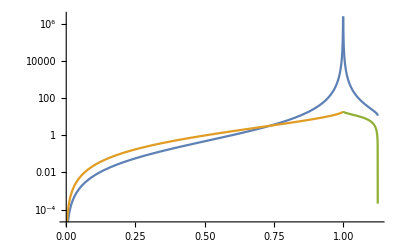

```mathematica
LogPlot[{Ectwa[λbar],EcThick["cold"][λbar],EcThick["hot"][λbar]},{λbar,0,9/8}]
```

## 2.4 Numerical solution

We now need to find the critical bubble profiles, i.e. the solutions to the critical bubble differential equation. Note that since χ̄=1(0) is a minimum (χ_b or χ_s respectively), then for both of these values V_T'(χ)=0 and χ̄ is constant in r̄: there is not bubble, just a constant value for all radii. Thus we need to start a bit off from these values, but not so much that we over/undershoot and get stuck in the maximum instead.

The whole point of the numerical approach is to perform a shooting algorithm to find the initial condition that allows us to interpolate between the required minima.

### # Routine

N.B.: because r̄=0 is a singular point, we will simply use a very small ε value instead.

```mathematica
(*Clear[BubbleSolution]

BubbleSolution[lb_,ε_:10^-2,nmax_:2,lowestRmax_:20,largestRmax_:100,tol_:10^-3,iter_:1000,ag_:50,wp_:50,XiniGuess_:False,debug_:False,verbose_:0]:=BubbleSolution[lb,ε,nmax,lowestRmax,largestRmax,tol,iter,ag,wp,XiniGuess,debug,verbose]=Block[{lbar,χ0,χ∞,χpost,χini,offset,offsetSize,uphill,downhill,RcGuess,rmax,res,i,Lstep,overshot,χiniOld,move,shift,LstepMax,diffeq,eqns,sol,χsol,χLast,divergedQ,χdiff,os,consecOverCtr,inc,shiftList={},χiniList={},offsetList={},χsolList={},χLastList={},χdiffList={},FinalRes
},

If[verbose>0,
Print["*****************************"];
Print["* Bubble numerical solution *"];
Print["*   (verbosity requested)   *"];
Print["*****************************"];
];

lbar=Rationalize[lb];(*turning λ̄ into exact fraction*)

(*exact true minimum (χ inside bubble is close to this number). Not exactly the value of χ(0), since the boundary condition χ(0)=Subscript[χ, min] does not yield a bubble, but only the χ=Subscript[χ, min]=constant solution.*)
χ0=HeavisideTheta[1-lb];
If[verbose>0,
Print["χ0 = "<>ToString[χ0//N]]
];

(*asymptotic value of χ(r->∞)*)
χ∞=HeavisideTheta[lb-1];
If[verbose>0,
Print["χ∞ = "<>ToString[χ∞//N]]
];

(*value of χ post-transition (i.e. inside bubble, Subscript[χ, fin]=χ(0)) in the twa*)
χpost=χfintwa[lbar];
If[verbose>0,
Print["χpost = "<>ToString[TraditionalForm[SetAccuracy[χpost,ag]]]]
];

(*initial value of χ(ε) for our numerical integration: use guess either an input guess XiniGuess, or χpost*)
χini=If[(XiniGuess===False)||(Abs[1-lbar]≤0.1),χpost,XiniGuess];

(*how much is the χini offset from the exact minimum*)
offset=SetAccuracy[Abs[χ0-χini]//Simplify,ag];

(*the order of magnitude; will be useful in our shooting algorithm*)
offsetSize=Floor[Log10[offset]];

(*numerical expressiong for initial value*)
χini=SetAccuracy[χini,ag];

(*in the particle-on-a-hill analogy, what direction in field-space is uphill/downhill*)
uphill=Sign[1-lb];
downhill=-uphill;

(*guess of the (dimensionless) critical bubble radius, in the thin-wall approximation*)
RcGuess=Rctwa[lbar];
If[verbose>0,
Print["Bubble radius guess Rc="<>ToString[RcGuess//N]]
];

(*largest radius we're interested in*)
rmax=Max[Min[nmax*RcGuess+lw,largestRmax],lowestRmax];
If[verbose>0,
Print["Largest radius of interest rmax="<>ToString[rmax//N]]
];

(*Begin shooting algorithm*)
If[verbose>0,
Print["-------------------------"];
Print["Begin: shooting algorithm"]
];
res=Catch@For[i=0;Lstep=(offsetSize-1/20);overshot=True;consecOverCtr=0;inc=0,i<iter,i++,
If[verbose>0,
Print["i="<>ToString[i]]
];

(*initial condition from previous iteration*)
χiniOld=χini;

(*in which direction to move for the new initial condition*)
move=If[i==0,0,Which[overshot==True,downhill,overshot==False,uphill]];

(*value of the shift*)
shift=move*10^Lstep;

(*appending shift in initial condition to list*)
AppendTo[shiftList,shift];

(*new initial condition*)
χini+=shift;

(*quick check that χini should not be negative; if so, swap it for a smaller, positive value *)
If[(χiniOld+shift)<0,
If[verbose>0,
Print["Woah! going into χini<0; will use instead half the previous positive value: old χini/2."]];χini=χiniOld/2,
None];

(*new offset (useful to limit size of new step)*)
offset=Abs[χ0-χini];
LstepMax=Log10[offset-10^(-(ag-1))];

If[verbose>0,
If[i==0,
Print["just starting!"];
Print["χini = "<>ToString[TraditionalForm[χiniOld]]],

Print["overshot previously?: "<>ToString[overshot]];
Print["old χini = "<>ToString[TraditionalForm[χiniOld]]];
Print["shift = "<>ToString[TraditionalForm[shift]]];
Print["new χini = "<>ToString[TraditionalForm[χini]]];
Print["new offset from minimum = "<>ToString[TraditionalForm[offset]]];
Print["max log step = "<>ToString[TraditionalForm[LstepMax]]];
]
];

(*appending new initial condition to list*)
AppendTo[χiniList,χini];

(*appending new offset in initial condition to list*)
AppendTo[offsetList,offset];

(*system of equations*)
diffeq=ReleaseHold[CritEq[lbar]]/.{χ->χfn};
eqns=SetAccuracy[{diffeq,χfn[ε]==χini,χfn'[ε]==0},ag];

(*solution*)
sol=NDSolve[eqns,χfn,{r,ε,rmax},Method->{"StiffnessSwitching"},InterpolationOrder->3,WorkingPrecision->wp,AccuracyGoal->ag];

(*profile*)
χsol=(χfn/.sol⟦1⟧);

(*appending solution to list*)
AppendTo[χsolList,χsol];

(*last value*)
χLast=χsol[rmax];
If[verbose>0,
Print["χLast = "<>ToString[TraditionalForm[χLast]]]
];

(*appending last value to lists*)
If[debug,AppendTo[χLastList,χLast]];

(*whether we have x(rmax) well past xtarget*)
divergedQ=((Sign[lbar-1]*(χLast-χ∞))>0);
If[verbose>0,
Print["diverged?: "<>ToString[divergedQ]]
];

(*difference between last value and target value*)
χdiff=Abs[χLast-χ∞];
If[verbose>0,
Print["i.e. χLast-χ∞ = "<>ToString[TraditionalForm[χdiff]]]
];

(*appending difference to list*)
AppendTo[χdiffList,χdiff];

(*finding out whether we overshot or undershot*)
os=Which[
divergedQ&&(i==0),
If[verbose>0,Print["Case 1: first point overshot"]];
{True,Lstep},

Not[divergedQ]&&(i==0),
If[verbose>0,Print["Case 2: first point undershot"]];
{False,Min[Lstep,LstepMax]},

divergedQ&&(overshot==True),
If[verbose>0,Print["Case 3: two consecutive overshots"]];
consecOverCtr++;
If[(verbose>0)&&(consecOverCtr>2),
Print["... there have been "<>ToString[consecOverCtr]<>" consecutive overshots."]
];
If[Mod[consecOverCtr,10]==0,inc++];
If[(verbose>0)&&(Mod[consecOverCtr,10]==0),
Print["... increasing order of magnitude of step by 1"];
];
{True,If[(consecOverCtr<10)||(Mod[consecOverCtr,10]≠ 0),Lstep,Lstep+inc]},

divergedQ&&(overshot==False),
If[verbose>0,Print["Case 4: undershot, then overshot"]];
{True,SetAccuracy[Log10[Abs[χiniList⟦-1⟧-χiniList⟦-2⟧]/2],ag]},

(χdiff>tol)&&(overshot==True),
If[verbose>0,Print["Case 5: overshot, then undershot"]];
consecOverCtr=0;
{False,Min[SetAccuracy[Log10[Abs[χiniList⟦-1⟧-χiniList⟦-2⟧]/2],ag],LstepMax]},

(χdiff>tol)&&(overshot==False),
If[verbose>0,Print["Case 6: two consecutive undershots"]];
{False,Min[Lstep,LstepMax]},

χdiff≤tol,
If[verbose>0,
Print["Done! Found it!!!"];
Print["~~~~~~~~~~~~~~~~~"]
];
Throw[(χfn/.sol⟦1⟧)]];

(*updating both the variable telling us whether this iteration overshot, and also the step*)
{overshot,Lstep}=os;
Lstep=SetAccuracy[Lstep,ag];

If[verbose>0,
Print["this iteration overshot: "<>ToString[overshot]];
Print["new Lstep: "<>ToString[TraditionalForm[Lstep]]];
Print["i.e. |shift| = "<>ToString[TraditionalForm[10^Lstep]]];
Print["....................."]];
];

(*if shooting failed, use last solution from iteration*)
If[res==Null,
Clear[res];
res=χsolList⟦-1⟧];

(*Returning results: {{λ̄,ε,rmax,res}, (if debug==True: χiniList, χLastList, shiftList, χsolList)}*)
FinalRes=If[debug,{{lb//N,ε,rmax,res},χiniList,χLastList,shiftList,χsolList},{{lb//N,ε,rmax,res}}];
FinalRes
]*)
```

#### # Tests

```mathematica
(*Clear[results,λbarRes,εRes,rmaxRes,bubbleRes,χinisRes,χLastsRes,shiftsRes,χsolsRes]*)
```

BubbleSolution[lb, ε, nmax, lowestRmax, largestRmax, tol, iter, ag, wp, debug, verbose]

```mathematica
(*results=BubbleSolution[1.124,10^-2,2,20,100,10^-3,3000,50,50,False,True,1]*)
```

```mathematica
(*BubbleSolution[1.124,10^-2,2,20,100,10^-3,3000,50,50,0.76032164828395855044726844131512876974824412924747960608212620903965690603617,True,1]*)
```

```mathematica
(*{λbarRes,εRes,rmaxRes,bubbleRes}=results⟦1⟧;
{χinisRes,χLastsRes,shiftsRes,χsolsRes}=Drop[results,1];*)
```

```mathematica
(*Plot[bubbleRes[r],{r,εRes,rmaxRes},PlotRange->{-0.1,1.1}]*)
```

```mathematica
(*(*Subscript[χ, last]≡χ(rmax)*)
ListLogPlot[{χLastsRes},PlotRange->{0,3},Frame->True]*)
```

```mathematica
(*(*Subscript[χ, ini]≡χ(ε)*)
ListLogPlot[χinisRes,Frame->True]*)
```

```mathematica
(*(*shifts: increments (blue) and decrements (orange) in Subscript[χ, ini]*)
ListLogPlot[{shiftsRes,-shiftsRes},Frame->True]*)
```

```mathematica
(*Clear[results,λbarRes,εRes,rmaxRes,bubbleRes,χinisRes,χLastsRes,shiftsRes,χsolsRes]*)
```

#### # Comparison to twa

```mathematica
(*Clear[lbarTest,twaBubTest,resultsTest,numBubTest,εTest,rmaxTest]*)
```

```mathematica
(*lbarTest=0.99;
twaBubTest[r_]=χtwa[r,lbarTest];
resultsTest=BubbleSolution[lbarTest];
numBubTest[r_]=resultsTest⟦1,-1⟧[r];

{εTest,rmaxTest}=resultsTest⟦1⟧⟦2;;3⟧;*)
```

```mathematica
(*Plot[{numBubTest[r],twaBubTest[r]},{r,εTest,rmaxTest},Frame->True]*)
```

```mathematica
(*Clear[lbarTest,twaBubTest,resultsTest,numBubTest,εTest,rmaxTest]*)
```

### Defining useful lists

```mathematica
Clear[λbarList,λbarString,rList]
```

Computing a list of λ̄

```mathematica
λbarList=Table[lb,{lb,0.01,0.99,0.005}];
λbarList=λbarList~Join~Table[lb,{lb,1.01,1.124,0.001}];
λbarList
λbarList//Length
```

{0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.105,0.11,0.115,0.12,0.125,0.13,0.135,0.14,0.145,0.15,0.155,0.16,0.165,0.17,0.175,0.18,0.185,0.19,0.195,0.2,0.205,0.21,0.215,0.22,0.225,0.23,0.235,0.24,0.245,0.25,0.255,0.26,0.265,0.27,0.275,0.28,0.285,0.29,0.295,0.3,0.305,0.31,0.315,0.32,0.325,0.33,0.335,0.34,0.345,0.35,0.355,0.36,0.365,0.37,0.375,0.38,0.385,0.39,0.395,0.4,0.405,0.41,0.415,0.42,0.425,0.43,0.435,0.44,0.445,0.45,0.455,0.46,0.465,0.47,0.475,0.48,0.485,0.49,0.495,0.5,0.505,0.51,0.515,0.52,0.525,0.53,0.535,0.54,0.545,0.55,0.555,0.56,0.565,0.57,0.575,0.58,0.585,0.59,0.595,0.6,0.605,0.61,0.615,0.62,0.625,0.63,0.635,0.64,0.645,0.65,0.655,0.66,0.665,0.67,0.675,0.68,0.685,0.69,0.695,0.7,0.705,0.71,0.715,0.72,0.725,0.73,0.735,0.74,0.745,0.75,0.755,0.76,0.765,0.77,0.775,0.78,0.785,0.79,0.795,0.8,0.805,0.81,0.815,0.82,0.825,0.83,0.835,0.84,0.845,0.85,0.855,0.86,0.865,0.87,0.875,0.88,0.885,0.89,0.895,0.9,0.905,0.91,0.915,0.92,0.925,0.93,0.935,0.94,0.945,0.95,0.955,0.96,0.965,0.97,0.975,0.98,0.985,0.99,1.01,1.011,1.012,1.013,1.014,1.015,1.016,1.017,1.018,1.019,1.02,1.021,1.022,1.023,1.024,1.025,1.026,1.027,1.028,1.029,1.03,1.031,1.032,1.033,1.034,1.035,1.036,1.037,1.038,1.039,1.04,1.041,1.042,1.043,1.044,1.045,1.046,1.047,1.048,1.049,1.05,1.051,1.052,1.053,1.054,1.055,1.056,1.057,1.058,1.059,1.06,1.061,1.062,1.063,1.064,1.065,1.066,1.067,1.068,1.069,1.07,1.071,1.072,1.073,1.074,1.075,1.076,1.077,1.078,1.079,1.08,1.081,1.082,1.083,1.084,1.085,1.086,1.087,1.088,1.089,1.09,1.091,1.092,1.093,1.094,1.095,1.096,1.097,1.098,1.099,1.1,1.101,1.102,1.103,1.104,1.105,1.106,1.107,1.108,1.109,1.11,1.111,1.112,1.113,1.114,1.115,1.116,1.117,1.118,1.119,1.12,1.121,1.122,1.123,1.124}

312

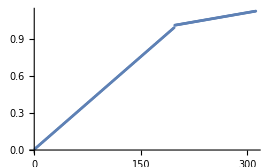

```mathematica
ListPlot[λbarList]
```

String form of λ̄

```mathematica
λbarString[λbar_]:=Module[{decimals,lbStr},
decimals=IntegerString[Round[1000*(λbar-IntegerPart[λbar])],10,3];
lbStr=ToString[IntegerPart[λbar]]<>"."<>decimals;
lbStr
]
```

A list of many values for radius:

```mathematica
rList={0.0}~Join~Table[r,{r,10^-2,100,(100-10^-2)/399}];
```

### # Full numerical results (takes ~2.5 hrs)

```mathematica
(*Clear[ColdTime,ColdResults,HotTime,HotResults,totalTime,resultsList,bubsList,rmaxList]*)
```

Computing the numerical results for that list of λ̄ (took ~2.5 hrs)

```mathematica
(*(*BubbleSolution[lb_,ε_:1/100,nmax_:2,lowestRmax_:20,largestRmax_:100,tol_:1/1000,iter_:1000,ag_:50,wp_:50,XiniGuess_:False,debug_:False,verbose_:0]*)*)
```

```mathematica
(*Coldλbar=Select[λbarList,(#<1&)];

ColdResults={};
XiniGuesses={False};

{ColdTime,nothing}=Timing[Monitor[Do[tempRes=BubbleSolution[Coldλbar⟦n⟧,10^-2,2,20,100,10^-4,5000,50,50,XiniGuesses⟦n⟧,True,0];
AppendTo[XiniGuesses,tempRes⟦2,-1⟧];
AppendTo[ColdResults,tempRes⟦1⟧],{n,Coldλbar//Length}],n]];

Print[ColdTime]
Print[ColdTime/3600]

Clear[XiniGuesses,tempRes,nothing]*)
```

```mathematica
(*Hotλbar=Select[λbarList,(#>1&)];

HotResults={};
XiniGuesses={False};

{HotTime,nothing}=Timing[Monitor[Do[tempRes=BubbleSolution[Hotλbar⟦n⟧,10^-2,2,20,100,10^-4,5000,50,50,XiniGuesses⟦n⟧,True,0];
AppendTo[XiniGuesses,tempRes⟦2,-1⟧];
AppendTo[HotResults,tempRes⟦1⟧],{n,Hotλbar//Length}],n]];

Print[HotTime]
Print[HotTime/3600]

Clear[XiniGuesses,tempRes,nothing]*)
```

```mathematica
(*totalTime=ColdTime+HotTime;
resultsList=ColdResults~Join~HotResults;*)
```

```mathematica
(*totalTime/60.(*time in minutes*)
%/60(*time in hours*)*)
```

Extracting the bubble solutions and the maximum radii

```mathematica
(*bubsList=(#⟦-1⟧[r]&/@resultsList);
rmaxList=(#⟦-2⟧&/@resultsList);*)
```

Plotting the cold bubble solutions:

```mathematica
(*Select[λbarList,(#<1&)]//Length*)
```

```mathematica
(*Do[p[i]=LogLinearPlot[bubsList⟦i⟧,{r,10^-2,rmaxList⟦i⟧},PlotRange->{{10^-2,100},{-0.1,1.1}},PlotStyle->ColorData[3,"ColorList"]⟦Mod[i,ColorData[3,"ColorList"]//Length]⟧],{i,50}];

Show[Table[p[i],{i,50}]]

Clear[p]

Do[p[i]=LogLinearPlot[bubsList⟦i⟧,{r,10^-2,rmaxList⟦i⟧},PlotRange->{{10^-2,100},{-0.1,1.1}},PlotStyle->ColorData[3,"ColorList"]⟦Mod[i,ColorData[3,"ColorList"]//Length]⟧],{i,51,100}];

Show[Table[p[i],{i,51,100}]]

Clear[p]

Do[p[i]=LogLinearPlot[bubsList⟦i⟧,{r,10^-2,rmaxList⟦i⟧},PlotRange->{{10^-2,100},{-0.1,1.1}},PlotStyle->ColorData[3,"ColorList"]⟦Mod[i,ColorData[3,"ColorList"]//Length]⟧],{i,101,150}];

Show[Table[p[i],{i,101,150}]]

Clear[p]

Do[p[i]=LogLinearPlot[bubsList⟦i⟧,{r,10^-2,rmaxList⟦i⟧},PlotRange->{{10^-2,100},{-0.1,1.1}},PlotStyle->ColorData[3,"ColorList"]⟦Mod[i,ColorData[3,"ColorList"]//Length]⟧],{i,151,197}];

Show[Table[p[i],{i,151,197}]]

Clear[p]*)
```

Plotting the hot bubble solutions:

```mathematica
(*Select[λbarList,(#>1&)]//Length*)
```

```mathematica
(*Do[p[i]=LogLinearPlot[bubsList⟦i⟧,{r,10^-2,rmaxList⟦i⟧},PlotRange->{{10^-2,100},{-0.1,1.1}},PlotStyle->ColorData[3,"ColorList"]⟦Mod[i,ColorData[3,"ColorList"]//Length]⟧],{i,198,250}];

Show[Table[p[i],{i,198,250}]]

Clear[p]

Do[p[i]=LogLinearPlot[bubsList⟦i⟧,{r,10^-2,rmaxList⟦i⟧},PlotRange->{{10^-2,100},{-0.1,1.1}},PlotStyle->ColorData[3,"ColorList"]⟦Mod[i,ColorData[3,"ColorList"]//Length]⟧],{i,251,312}];

Show[Table[p[i],{i,251,312}]]

Clear[p]*)
```

### # Bubble solutions for all r

Extending bubble solutions to any radius:

```mathematica
(*Clear[extBubsList]

extBubsList[iLoc_,rr_]:=Block[{rac,λbar,bubNum,bubNumIni,rmaxNum,χ∞,res},
rac=SetAccuracy[Rationalize[rr],50];
λbar=λbarList⟦iLoc⟧;
bubNum[rvar_]=bubsList⟦iLoc⟧/.r->rvar;
bubNumIni=SetAccuracy[bubsList⟦iLoc⟧/.r->0.01,50];
rmaxNum=rmaxList⟦iLoc⟧;
χ∞=HeavisideTheta[λbar-1];
res=Which[rr<10^-2,bubNumIni,rac<rmaxNum,bubNum[rac]//Evaluate,rac≥rmaxNum,χ∞];
res
]*)
```

### # Exporting numerical results

Exporting numerical results

```mathematica
(*Monitor[For[i=1,i≤(λbarList//Length),i++,
λbar=λbarList⟦i⟧;
fileName="bubble_lb-"<>λbarString[λbar]<>".csv";
table=Table[{SetAccuracy[r,50],extBubsList[i,r]//Evaluate},{r,Drop[rList,1]}];
PrependTo[table,{rList⟦1⟧,table⟦1,2⟧}];
Export[bubbleDir<>fileName,table]
],i]

Rtab=Table[{SetAccuracy[Rationalize[λbarList⟦i⟧],50],SetAccuracy[rmaxList⟦i⟧,50]},{i,Length@λbarList}];
Export[fnsLambdaDir<>"rmax.csv",Rtab];

Clear[i,λbar,fileName,table,Rtab]*)
```

### Importing numerical results

Importing numerical results previously computed

```mathematica
Clear[bubTab,bubFn,rmaxTab]

For[i=1,i≤(λbarList//Length),i++,
λbar=λbarList⟦i⟧;
fileName="bubble_lb-"<>λbarString[λbar]<>".csv";
bubTab[i]=Import[bubbleDir<>fileName];
bubFn[i]=Interpolation[bubTab[i],InterpolationOrder->2]
]

rmaxTab=Import[fnsLambdaDir<>"rmax.csv"];

Clear[i,λbar,fileName]
```

Some quick plots

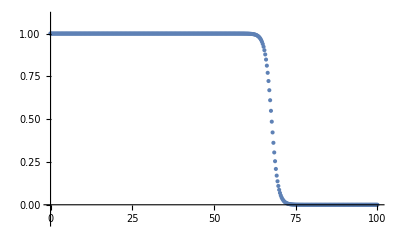

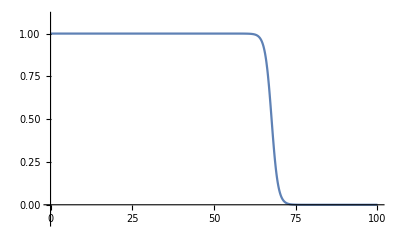

```mathematica
idx=197;
ListPlot[bubTab[idx],PlotRange->{-0.1,1.1}]
Plot[bubFn[idx][r],{r,0,100},PlotRange->{-0.1,1.1}]
Clear[idx]
```

## 2.5 Critical Energy (dimensionless): full value

The energy of the critical bubble is:

E_T[χ_bub]=∫d^3 x  1/2(∇χ_bub)^2+ V_T(χ_bub) = χ_b^2/M 4π ∫d r̄ (r̄)^2 ( 1/2((d(χ̄)_bub)/(d r̄))^2+(V̄)_T((χ̄)_bub))

with χ_bub=χ_b(χ̄)_bub and  (V̄)_T(χ̄)=(V_T(χ̄ χ_b))/(χ_b^2 M^2).

As we saw, this expression is formally infinite. However, what the physics depends on is the (finite) difference between the energies of the initial constant-χ configuration ((χ̄)_ini) and the bubble (χ̄)_bub configuration. This is called the critical energy, and is given by:

E_c≡E_T[χ_bub]-E_T[χ_ini].

### # Routine

```mathematica
(*Clear[EcRoutine]

EcRoutine[iLoc_,tormax_:True]:=Block[{lb,χsol,dχsol,χ∞,rmax,ke,vini,vbub,ec},
(*λ̄ from our data*)
lb=λbarList⟦iLoc⟧;

(*bubble profiles and their derivative*)
χsol[r_?NumberQ]=bubFn[iLoc][r];
dχsol[r_?NumberQ]=D[χsol[r],r];

(*field value at infinity*)
χ∞=HeavisideTheta[lb-1];

(*maximum radius of integration*)
rmax=If[tormax,rmaxTab⟦iLoc,2⟧,SetAccuracy[100,50]];

(*kinetic energy of the bubble*)
ke[r_?NumberQ]=1/2(dχsol[SetAccuracy[r,50]])^2;

(*potential energy of the bubble*)
vbub[r_?NumberQ]=dimlessV[χsol[SetAccuracy[r,50]],lb];

(*potential energy of the initial configuration (whether we use the last value of our data or the exact asymptotic value, makes little difference)*)
vini=dimlessV[χsol[rmax],lb];
(*vini=dimlessV[χ∞,lb];*)

ec=4π*NIntegrate[r^2(ke[r]+vbub[r]-vini),{r,0,rmax},Method->"DoubleExponential",MaxRecursion->500,PrecisionGoal->5];
ec
]*)
```

### # Exporting partial (Ē)_c table (for λ̄ ∈ [0.01, 0.99] ∪ [1.01, 1.124])

```mathematica
(*table=Table[{λbarList⟦i⟧,EcRoutine[i]},{i,1,Length@λbarList}];
Export[fnsLambdaDir<>"part_Ecrit.csv",table];
Clear[table]*)
```

### Importing partial (Ē)_c table (for λ̄ ∈ [0.01, 0.99] ∪ [1.01, 1.124])

```mathematica
partEcritTab=Import[fnsLambdaDir<>"part_Ecrit.csv"];
```

#### Comparing with twa

```mathematica
partEcritTab⟦196;;199⟧
Ectwa[0.99]
Ectwa[0.991]
Ectwa[1.009]
Ectwa[1.01]
```

{{0.985,1468.06},{0.99,3238.44},{1.01,2959.02},{1.011,2433.19}}

3100.42

3828.23

3828.05

3100.22

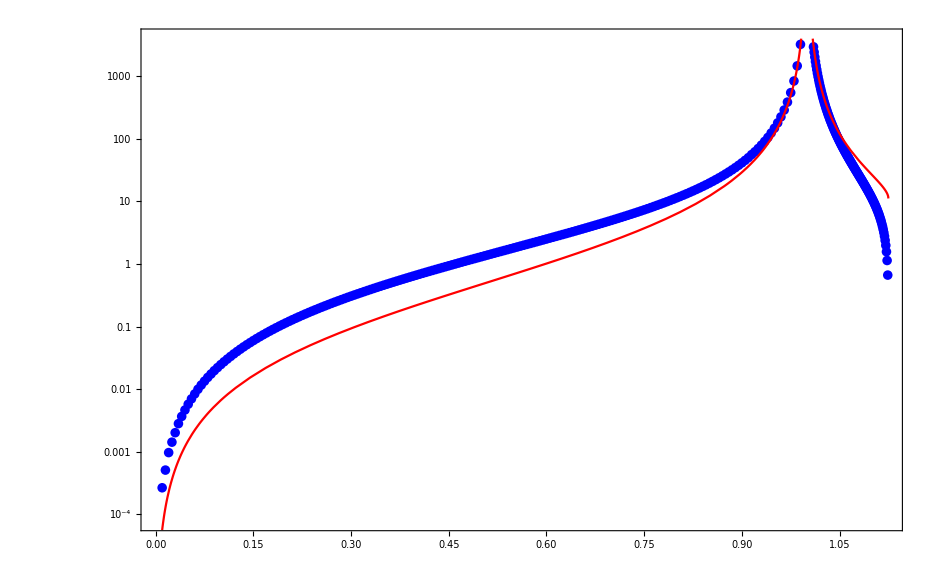

```mathematica
p1=ListLogPlot[partEcritTab,Frame->True,PlotRange->{0,4000},PlotStyle->Blue];
p2=LogPlot[Ectwa[λbar],{λbar,0.01,1.125},PlotRange->{0,4000},PlotStyle->Red];
Show[p1,p2]
Clear[p1,p2]
```

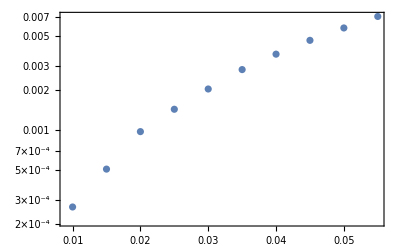

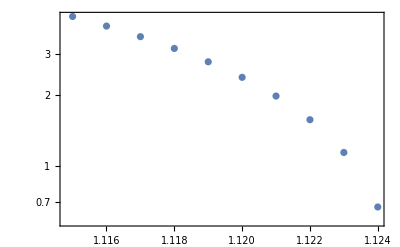

```mathematica
ListLogPlot[partEcritTab⟦1;;10⟧,Frame->True]
ListLogPlot[partEcritTab⟦-10;;-1⟧,Frame->True]
```

### # Preparing more complete (Ē)_c table (for λ̄ ∈ [0.001, 0.999] ∪ [1.001, 1.1249]), supplementing with thin & thick wall approximations

```mathematica
(*λbarList
cut=Position[λbarList,0.99]⟦1,1⟧
λbarListCold=λbarList⟦1;;cut⟧
λbarListHot=λbarList⟦cut+1;;-1⟧*)
```

```mathematica
(*table=Table[partEcritTab⟦i⟧,{i,cut}](*numeric cold*);
table=table~Join~Table[{λbar,Ectwa[λbar]},{λbar,0.995,0.999,0.001}](*thin cold*);
table=table~Join~Table[{λbar,Ectwa[λbar]},{λbar,1.001,1.009,0.001}](*thin hot*);
table=table~Join~Table[partEcritTab⟦i⟧,{i,cut+1,Length@partEcritTab}](*numeric hot*);
table={{SetAccuracy[10^-5,30],SetAccuracy[EcThick["cold"][10^-5],30]}}~Join~Table[{λbar,EcThick["cold"][λbar]},{λbar,0.001,0.005,0.001}]~Join~table(*thick cold*);
table=table~Join~Table[{λbar,EcThick["hot"][λbar]},{λbar,1.1245,1.12499,0.00001}]~Join~{{SetAccuracy[9/8-10^-15,30],SetAccuracy[EcThick["hot"][9/8-10^-15],30]}}(*thick hot*);
table
Export[fnsLambdaDir<>"Ecrit.csv",table];
Clear[table]*)
```

### (Ē)_c(λ̄)

#### Importing full (Ē)_c(λ̄) table

```mathematica
EcritTab=Import[fnsLambdaDir<>"Ecrit.csv"];
alllbarTab=#⟦1⟧&/@EcritTab;
```

Plots

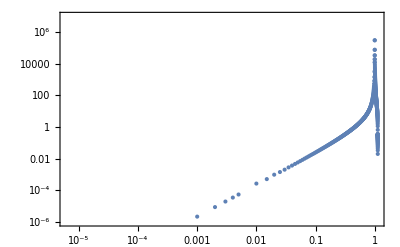

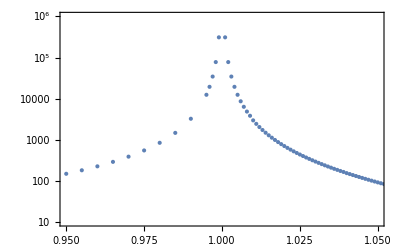

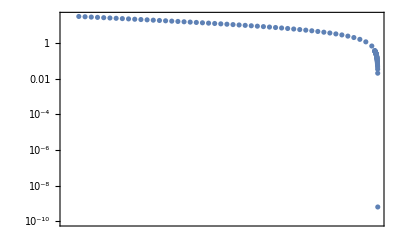

```mathematica
ListLogLogPlot[EcritTab,Frame->True,PlotRange->{10^-6,10^7}]
ListLogPlot[EcritTab,Frame->True,PlotRange->{{0.95,1.05},{10,10^6}}]
ListLogLogPlot[EcritTab⟦-100;;-1⟧,Frame->True]
```

#### Defining (Ē)_c(λ̄)

Separating the regions for λ̄<1 and λ̄>1.

```mathematica
Clear[lolbarTab,hilbarTab,lolbarFn,hilbarFn,loL,loR,hiL,hiR,EcFn]
```

```mathematica
lolbarTab=Select[EcritTab,#⟦1⟧<1&];
lolbarTab={#⟦1⟧//Log10,#⟦2⟧//Log10}&/@lolbarTab;

hilbarTab=Select[EcritTab,#⟦1⟧>1&];
hilbarTab={#⟦1⟧//Log10,#⟦2⟧//Log10}&/@hilbarTab;
```

Interpolating in log-space

```mathematica
lolbarFn=Interpolation[lolbarTab,InterpolationOrder->1,Method->"Spline"];
hilbarFn=Interpolation[hilbarTab,InterpolationOrder->1,Method->"Spline"];
```

Edges of the patches

```mathematica
{loL,loR}={10^lolbarTab⟦1,1⟧,10^lolbarTab⟦-1,1⟧};
{hiL,hiR}={10^hilbarTab⟦1,1⟧,10^hilbarTab⟦-1,1⟧};
```

Defining the full function

```mathematica
Clear[EcFn]

EcFn[λbar_]:=Which[0≤λbar<loL,limEcThick["cold"][λbar],loL≤λbar<loR,10^lolbarFn[Log10[λbar]],((loR≤λbar<1)||(1<λbar≤hiL)),Ectwa[λbar],hiL<λbar≤hiR,10^hilbarFn[Log10[λbar]],hiR<λbar≤9/8,limEcThick["hot"][λbar]]
```

Plots

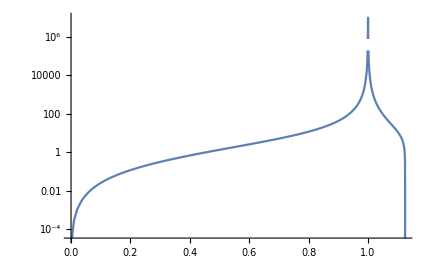

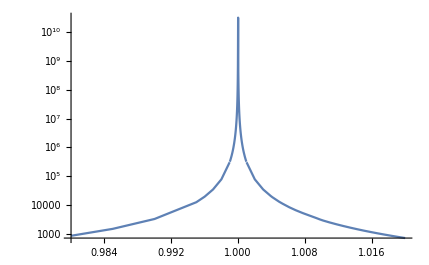

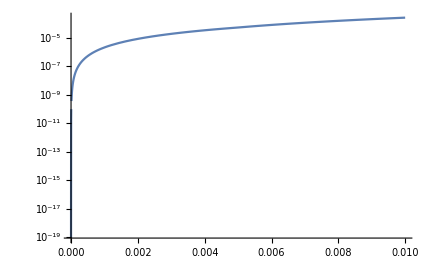

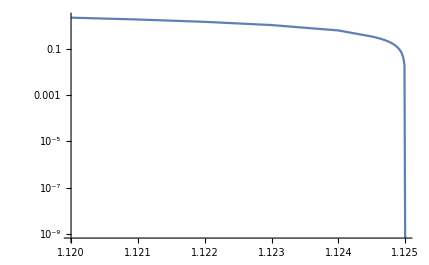

```mathematica
LogPlot[EcFn[λbar],{λbar,0,1.125}]
LogPlot[EcFn[λbar],{λbar,0.98,1.02},PlotRange->Full]
LogPlot[EcFn[λbar],{λbar,0,0.01},PlotRange->Full]
LogPlot[EcFn[λbar],{λbar,1.12,1.125},PlotRange->Full]
```

### # Exporting the first derivative of (Ē)_c(λ̄)

#### # Raw first derivative

The full derivative

```mathematica
(*Clear[dEc]
dEc[ll_?NumberQ]=D[EcFn[λbar],λbar]/.{λbar->ll}(*the derivative from the interpolated function*);
Dtab={#,dEc[#]}&/@λbarList;
LogPlot[dEc[λbar]//Abs,{λbar,0,9/8}]*)
```

#### # Smoothing

Convoluting with a Gaussian to smooth the data, for λ̄∈[0.01,0.995] and λ̄∈[1.005,1.1249]

```mathematica
(*ColdEdges={0.001,0.995};
CoolSteps=0.001;
HotEdges={1.005,1.1249};
HotSteps=0.0001;*)
```

```mathematica
(*ColdTransFnλbar[λbar_]:=ArcTanh[2(λbar-0.5)]
tab=Table[{ColdTransFnλbar[λbar],Log[dEc[λbar]]},{λbar,ColdEdges⟦1⟧,ColdEdges⟦-1⟧,CoolSteps}](*transforming the x- and y- axis, using tanh and log*);

smoothCold=GaussianFilter[#⟦2⟧&/@tab,{20,4}](*filtering in that space: crucially, the x-axis must be evenly spaced if this is to be truly a Gaussian function of the x-axis*);

(*interpolating*)
smoothCold=Transpose[{Table[ColdTransFnλbar[λbar],{λbar,ColdEdges⟦1⟧,ColdEdges⟦-1⟧,CoolSteps}],smoothCold}];
smoothColdInterp=Interpolation[smoothCold];

smoothCold=Transpose[{Table[λbar,{λbar,ColdEdges⟦1⟧,ColdEdges⟦-1⟧,CoolSteps}],Exp[#⟦2⟧&/@smoothCold]}](*putting everything together; exponentiating back the y-axis*);

tab=Table[{λbar,dEc[λbar]},{λbar,ColdEdges⟦1⟧,ColdEdges⟦-1⟧,CoolSteps}];

ListLogPlot[{tab//Abs,smoothCold//Abs}]

ListLogPlot[{tab//Abs,smoothCold//Abs},PlotRange->{{0.95,0.995},{1000,10^6}}]

(#⟦2⟧&/@(smoothCold-tab))/(#⟦2⟧&/@tab);
Max[%//Abs]

(tab//Length)
(tab//Length)-(smoothCold//Length)
Clear[tab]*)
```

```mathematica
(*HotTransFnλbar[λbar_]:=ArcTanh[(2/(9/8-1))(λbar-(9/8+1)/2)]
tab=Table[{HotTransFnλbar[λbar],Log[dEc[λbar]//Abs]},{λbar,HotEdges⟦1⟧,HotEdges⟦-1⟧,HotSteps}](*transforming the x- and y- axis, using tanh and log*);

smoothHot=GaussianFilter[#⟦2⟧&/@tab,{30,15}](*filtering in that space: crucially, the x-axis must be evenly spaced if this is to be truly a Gaussian function of the x-axis*);

(*interpolating*)
smoothHot=Transpose[{Table[HotTransFnλbar[λbar],{λbar,HotEdges⟦1⟧,HotEdges⟦-1⟧,HotSteps}],smoothHot}];
smoothHotInterp=Interpolation[smoothHot];

smoothHot=Transpose[{Table[λbar,{λbar,HotEdges⟦1⟧,HotEdges⟦-1⟧,HotSteps}],-Exp[#⟦2⟧&/@smoothHot]}](*putting everything together; exponentiating back the y-axis*);

tab=Table[{λbar,dEc[λbar]},{λbar,HotEdges⟦1⟧,HotEdges⟦-1⟧,HotSteps}];

ListLogPlot[{tab//Abs,smoothHot//Abs}]

ListLogPlot[{tab//Abs,smoothHot//Abs},PlotRange->{{1.01,1.05},{1000,10^7}}]

ListLogPlot[{tab//Abs,smoothHot//Abs},PlotRange->{{1.1,1.125},{200,10^3}}]

(#⟦2⟧&/@(smoothHot-tab))/(#⟦2⟧&/@tab);
Max[%//Abs]

(tab//Length)
(tab//Length)-(smoothHot//Length)
Clear[tab]*)
```

#### # Patching original and smoothed parts, and complementing with thin and thick approximations

```mathematica
(*Clear[table]
table={#,dEc[#]}&/@Select[λbarListCold,#<ColdEdges⟦1⟧&](*original cold derivative*);
table=table~Join~Table[{λbar,E^smoothColdInterp[ColdTransFnλbar[λbar]]},{λbar,Select[λbarListCold,ColdEdges⟦2⟧≥#≥ColdEdges⟦1⟧&]}](*smoothed, cold derivative*);
table=table~Join~({#,dEc[#]}&/@Select[λbarListCold,ColdEdges⟦2⟧<#≤λbarListCold⟦-1⟧&])(*original cold derivative*);
table=table~Join~Table[{λbar,dEctwadλ[λbar]},{λbar,0.993,0.999,0.001}](*thin cold derivative*);
table=table~Join~Table[{λbar,dEctwadλ[λbar]},{λbar,1.003,1.009,0.001}](*thin hot derivative*);
table=table~Join~(({#,dEc[#]}&/@Select[λbarListHot,λbarListHot⟦1⟧≤#<HotEdges⟦1⟧&]))(*original hot derivative*);
table=table~Join~Table[{λbar,-E^smoothHotInterp[HotTransFnλbar[λbar]]},{λbar,Select[λbarListHot,HotEdges⟦2⟧≥#≥HotEdges⟦1⟧&]}](*smoothed, hot derivative*);
table=table~Join~(({#,dEc[#]}&/@Select[λbarListHot,HotEdges⟦2⟧<#&]))(*original hot derivative*);

table=({#,dEcThickdλ["cold"][#]}&/@Select[alllbarTab,#<table⟦1,1⟧&])~Join~table(*thick cold*);
table=table~Join~({#,dEcThickdλ["hot"][#]}&/@Select[alllbarTab,#>table⟦-1,1⟧&])(*thick hot*);

table
Export[fnsLambdaDir<>"DEcrit.csv",table];*)
```

```mathematica
(*p1=ListLogPlot[table//Abs,Joined->True];
p2=LogPlot[dEc[λbar]//Abs,{λbar,0,9/8},PlotStyle->Orange];
Show[p2,p1]
Clear[p1,p2]

p1=ListLogPlot[table//Abs,Joined->True,PlotRange->{{0,0.1},{0.001,1}}];
p2=LogPlot[dEc[λbar]//Abs,{λbar,0,9/8},PlotStyle->Orange,PlotRange->{{0,0.1},{0.001,1}}];
Show[p2,p1]
Clear[p1,p2]

p1=ListLogPlot[table//Abs,Joined->True,PlotRange->{{1.08,1.125},{300,1000}}];
p2=LogPlot[dEc[λbar]//Abs,{λbar,0,9/8},PlotStyle->Orange,PlotRange->{{1.08,1.125},{300,1000}}];
Show[p2,p1]
Clear[p1,p2]

Clear[table]*)
```

### (Ē)_c'(λ̄)

#### Importing the first derivative of (Ē)_c(λ̄)

```mathematica
DEcritTab=Import[fnsLambdaDir<>"DEcrit.csv"];
```

#### Defining (Ē)_c'(λ̄)

Separating the regions for λ̄<1 and λ̄>1, which have positive/negative values of the derivative.

```mathematica
Clear[DlolbarTab,DhilbarTab,DlolbarFn,DhilbarFn,DloL,DloR,DhiL,DhiR,dEcFndλ]
```

```mathematica
DlolbarTab=Select[DEcritTab,#⟦1⟧<1&];
DlolbarTab={#⟦1⟧//Log10,#⟦2⟧//Log10}&/@DlolbarTab;

DhilbarTab=Select[DEcritTab,#⟦1⟧>1&];
DhilbarTab={#⟦1⟧//Log10,Abs[#⟦2⟧]//Log10}&/@DhilbarTab;
```

Interpolating in log-space

```mathematica
DlolbarFn=Interpolation[DlolbarTab,InterpolationOrder->1,Method->"Spline"];
DhilbarFn=Interpolation[DhilbarTab,InterpolationOrder->1,Method->"Spline"];
```

Edges of the patches

```mathematica
{DloL,DloR}={10^DlolbarTab⟦1,1⟧,10^DlolbarTab⟦-1,1⟧};
{DhiL,DhiR}={10^DhilbarTab⟦1,1⟧,10^DhilbarTab⟦-1,1⟧};
```

Defining the full function

```mathematica
Clear[dEcFndλ]

dEcFndλ[λbar_]:=Which[0≤λbar<DloL,limdEcThick["cold"][λbar],DloL≤λbar<DloR,10^DlolbarFn[Log10[λbar]],((DloR≤λbar<1)||(1<λbar≤DhiL)),dEctwadλ[λbar],DhiL<λbar≤DhiR,-10^DhilbarFn[Log10[λbar]],DhiR<λbar≤9/8,limdEcThick["hot"][λbar]]
```

Plots

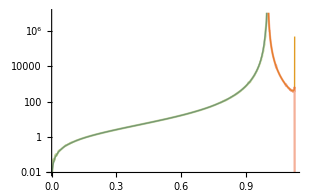

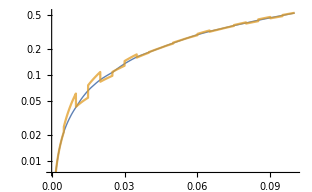

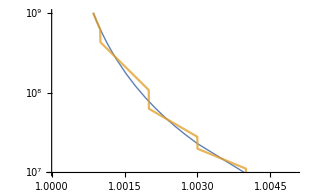

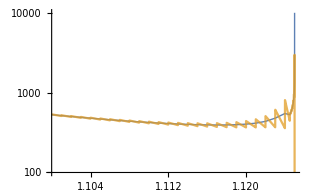

```mathematica
dEc[ll_?NumberQ]=D[EcFn[λbar],λbar]/.{λbar->ll}(*the derivative from the interpolated function*);

LogPlot[{dEcFndλ[λbar],-dEcFndλ[λbar],dEc[λbar],-dEc[λbar]},{λbar,0,9/8},PlotRange->{0.01,10^7},PlotStyle->{Thick,Thick,Opacity[0.5],Opacity[0.5]}]
LogPlot[{dEcFndλ[λbar],dEc[λbar]},{λbar,0,0.1},PlotStyle->{Thick,Opacity[0.75]}]
LogPlot[{-dEcFndλ[λbar],-dEc[λbar]},{λbar,0.995,1.005},PlotRange->{10^7,10^9},PlotStyle->{Thick,Opacity[0.75]}]
LogPlot[{-dEcFndλ[λbar],-dEc[λbar]},{λbar,1.1,9/8},PlotRange->{100,10^4},PlotStyle->{Thick,Opacity[0.75]}]

Clear[dEc]
```

# Test

Integrating result and comparing to original (Ē)_c(λ̄):

```mathematica
(*tab=Table[{λbar,NIntegrate[dEcFndλ[ll],{ll,0,λbar}]//Quiet},{λbar,Select[alllbarTab,#<1&]}];
tab=tab~Join~Table[{λbar,NIntegrate[dEcFndλ[ll],{ll,λbar,1.125}]//Quiet},{λbar,Select[alllbarTab,#>1&]}];
ListLogPlot[{EcritTab//Abs,tab//Abs}]
Clear[tab]*)
```

### # Exporting the second derivative of (Ē)_c(λ̄)

#### # Raw second derivative

The full derivative

```mathematica
(*Clear[d2Ec]
d2Ec[ll_?NumberQ]=D[dEcFndλ[λbar],λbar]/.{λbar->ll}(*the derivative from the interpolated function of the derivative*);
D2tab={#,d2Ec[#]}&/@λbarList;
LogPlot[d2Ec[λbar]//Abs,{λbar,0,9/8}]*)
```

#### # Smoothing

Convoluting with a Gaussian to smooth the data, for λ̄∈[0.01,0.995] and λ̄∈[1.005,1.1249]

```mathematica
(*ColdEdges={0.001,0.995};
CoolSteps=0.001;

HotEdges={1.005,1.115};
HotSteps=0.001;

SpinEdges={1.1151,1.118};
SpinSteps=0.0001;

HottestEdges={1.1181,1.1249};
HottestSteps=0.0001;*)
```

```mathematica
(*ColdTransFnλbar[λbar_]:=ArcTanh[2(λbar-0.5)]
tab=Table[{ColdTransFnλbar[λbar],Log[d2Ec[λbar]]},{λbar,ColdEdges⟦1⟧,ColdEdges⟦-1⟧,CoolSteps}](*transforming the x- and y- axis, using tanh and log*);

smoothCold=GaussianFilter[#⟦2⟧&/@tab,{17,10}](*filtering in that space: crucially, the x-axis must be evenly spaced if this is to be truly a Gaussian function of the x-axis*);

(*interpolating*)
smoothCold=Transpose[{Table[ColdTransFnλbar[λbar],{λbar,ColdEdges⟦1⟧,ColdEdges⟦-1⟧,CoolSteps}],smoothCold}];
smoothColdInterp=Interpolation[smoothCold];

smoothCold=Transpose[{Table[λbar,{λbar,ColdEdges⟦1⟧,ColdEdges⟦-1⟧,CoolSteps}],Exp[#⟦2⟧&/@smoothCold]}](*putting everything together; exponentiating back the y-axis*);

tab=Table[{λbar,d2Ec[λbar]},{λbar,ColdEdges⟦1⟧,ColdEdges⟦-1⟧,CoolSteps}];

ListLogPlot[{tab//Abs,smoothCold//Abs}]

ListLogPlot[{tab//Abs,smoothCold//Abs},PlotRange->{{0.95,0.995},{10^5,10^8}}]

(#⟦2⟧&/@(smoothCold-tab))/(#⟦2⟧&/@tab);
Max[%//Abs]

(tab//Length)
(tab//Length)-(smoothCold//Length)
Clear[tab]*)
```

```mathematica
(*HotTransFnλbar[λbar_]:=ArcTanh[(2/(9/8-1))(λbar-(9/8+1)/2)]
tab=Table[{HotTransFnλbar[λbar],Log[d2Ec[λbar]//Abs]},{λbar,HotEdges⟦1⟧,HotEdges⟦-1⟧,HotSteps}](*transforming the x- and y- axis, using tanh and log*);

smoothHot=GaussianFilter[#⟦2⟧&/@tab,{5,5}](*filtering in that space: crucially, the x-axis must be evenly spaced if this is to be truly a Gaussian function of the x-axis*);

(*interpolating*)
smoothHot=Transpose[{Table[HotTransFnλbar[λbar],{λbar,HotEdges⟦1⟧,HotEdges⟦-1⟧,HotSteps}],smoothHot}];
smoothHotInterp=Interpolation[smoothHot];

smoothHot=Transpose[{Table[λbar,{λbar,HotEdges⟦1⟧,HotEdges⟦-1⟧,HotSteps}],Exp[#⟦2⟧&/@smoothHot]}](*putting everything together; exponentiating back the y-axis*);

tab=Table[{λbar,d2Ec[λbar]},{λbar,HotEdges⟦1⟧,HotEdges⟦-1⟧,HotSteps}];

ListLogPlot[{tab//Abs,smoothHot//Abs}]

ListLogPlot[{tab//Abs,smoothHot//Abs},PlotRange->{{1.01,1.1},{1000,10^7}}]

(#⟦2⟧&/@(smoothHot-tab))/(#⟦2⟧&/@tab);
Max[%//Abs]

(tab//Length)
(tab//Length)-(smoothHot//Length)
Clear[tab]*)
```

```mathematica
(*tab=Table[{λbar,d2Ec[λbar]},{λbar,SpinEdges⟦1⟧,SpinEdges⟦-1⟧,SpinSteps}](*transforming the x- and y- axis, using tanh and log*);

smoothSpin=GaussianFilter[#⟦2⟧&/@tab,{10,10}](*filtering in that space: crucially, the x-axis must be evenly spaced if this is to be truly a Gaussian function of the x-axis*);

smoothSpin=Transpose[{Table[λbar,{λbar,SpinEdges⟦1⟧,SpinEdges⟦-1⟧,SpinSteps}],smoothSpin}](*putting everything together; exponentiating back the y-axis*);;
smoothSpinInterp=Interpolation[smoothSpin](*interpolating*);

tab=Table[{λbar,d2Ec[λbar]},{λbar,SpinEdges⟦1⟧,SpinEdges⟦-1⟧,SpinSteps}];

ListLogPlot[{tab//Abs,smoothSpin//Abs}]

(#⟦2⟧&/@(smoothSpin-tab))/(#⟦2⟧&/@tab);
Max[%//Abs]

(tab//Length)
(tab//Length)-(smoothSpin//Length)

Clear[tab]*)
```

```mathematica
(*tab=Table[{HotTransFnλbar[λbar],Log[d2Ec[λbar]//Abs]},{λbar,HottestEdges⟦1⟧,HottestEdges⟦-1⟧,HottestSteps}](*transforming the x- and y- axis, using tanh and log*);

smoothHottest=GaussianFilter[#⟦2⟧&/@tab,{15,15}](*filtering in that space: crucially, the x-axis must be evenly spaced if this is to be truly a Gaussian function of the x-axis*);

(*interpolating*)
smoothHottest=Transpose[{Table[HotTransFnλbar[λbar],{λbar,HottestEdges⟦1⟧,HottestEdges⟦-1⟧,HottestSteps}],smoothHottest}];
smoothHottestInterp=Interpolation[smoothHottest];

smoothHottest=Transpose[{Table[λbar,{λbar,HottestEdges⟦1⟧,HottestEdges⟦-1⟧,HottestSteps}],-Exp[#⟦2⟧&/@smoothHottest]}](*putting everything together; exponentiating back the y-axis*);

tab=Table[{λbar,d2Ec[λbar]},{λbar,HottestEdges⟦1⟧,HottestEdges⟦-1⟧,HottestSteps}];

ListLogPlot[{tab//Abs,smoothHottest//Abs,{#⟦1⟧,-#⟦2⟧}&/@smoothHottest},PlotRange->{HottestEdges,{1000,10^7}}]

(#⟦2⟧&/@(smoothHottest-tab))/(#⟦2⟧&/@tab);
Max[%//Abs]

(tab//Length)
(tab//Length)-(smoothHottest//Length)
Clear[tab]*)
```

#### # Patching original and smoothed parts, and complementing with thin and thick approximations

```mathematica
(*Clear[table]
table={#,d2Ec[#]}&/@Select[λbarListCold,#<ColdEdges⟦1⟧&](*original cold derivative*);
table=table~Join~Table[{λbar,E^smoothColdInterp[ColdTransFnλbar[λbar]]},{λbar,Select[λbarListCold,ColdEdges⟦2⟧≥#≥ColdEdges⟦1⟧&]}](*smoothed, cold derivative*);
table=table~Join~({#,d2Ec[#]}&/@Select[λbarListCold,ColdEdges⟦2⟧<#≤λbarListCold⟦-1⟧&])(*original cold derivative*);
table=table~Join~Table[{λbar,d2Ectwadλ2[λbar]},{λbar,0.993,0.999,0.001}](*thin cold derivative*);
table=table~Join~Table[{λbar,d2Ectwadλ2[λbar]},{λbar,1.003,1.009,0.001}](*thin hot derivative*);
table=table~Join~(({#,d2Ec[#]}&/@Select[λbarListHot,λbarListHot⟦1⟧≤#<HotEdges⟦1⟧&]))(*original hot derivative*);
table=table~Join~Table[{λbar,E^smoothHotInterp[HotTransFnλbar[λbar]]},{λbar,Select[λbarListHot,HotEdges⟦2⟧≥#≥HotEdges⟦1⟧&]}](*smoothed, hot derivative*);
table=table~Join~Table[{λbar,smoothSpinInterp[λbar]},{λbar,Select[λbarListHot,SpinEdges⟦2⟧≥#≥SpinEdges⟦1⟧&]}](*smoothed, spin derivative*);
table=table~Join~Table[{λbar,-E^smoothHottestInterp[HotTransFnλbar[λbar]]},{λbar,Select[λbarListHot,HottestEdges⟦2⟧≥#≥HottestEdges⟦1⟧&]}](*smoothed, spin derivative*);
table=table~Join~(({#,dEc[#]}&/@Select[λbarListHot,HottestEdges⟦2⟧<#&]))(*original hot derivative*);

table=({#,d2EcThickdλ2["cold"][#]}&/@Select[alllbarTab,#<table⟦1,1⟧&])~Join~table(*thick cold*);
table=table~Join~({#,d2EcThickdλ2["hot"][#]}&/@Select[alllbarTab,#>table⟦-1,1⟧&])(*thick hot*);

table
Export[fnsLambdaDir<>"D2Ecrit.csv",table];*)
```

```mathematica
(*p1=ListLogPlot[table//Abs,Joined->True];
p2=LogPlot[d2Ec[λbar]//Abs,{λbar,0,9/8},PlotStyle->Orange];
Show[p2,p1]
Clear[p1,p2]

p1=ListLogPlot[table//Abs,Joined->True,PlotRange->{{0,0.2},{3,15}}];
p2=LogPlot[d2Ec[λbar]//Abs,{λbar,0,9/8},PlotStyle->Orange,PlotRange->{{0,0.2},{3,15}}];
Show[p2,p1]
Clear[p1,p2]

p1=ListLogPlot[table//Abs,Joined->True,PlotRange->{{1.08,1.125},{100,10^8}}];
p2=LogPlot[d2Ec[λbar]//Abs,{λbar,0,9/8},PlotStyle->Orange,PlotRange->{{1.08,1.125},{100,10^8}}];
Show[p2,p1]
Clear[p1,p2]

Clear[table]*)
```

### (Ē)_c''(λ̄)

#### Importing the second derivative of (Ē)_c(λ̄)

```mathematica
D2EcritTab=Import[fnsLambdaDir<>"D2Ecrit.csv"];
```

#### Defining (Ē)_c''(λ̄)

Separating the regions according to λ̄ and the sign of the second derivative.

```mathematica
Clear[D2ColdlbarTab,D2HotlbarTab,D2SpinlbarTab,D2ColdlbarFn,D2HotlbarFn,D2SpinlbarFn,D2ColdL,D2ColdR,D2HotL,D2HotR,D2SpinL,D2SpinR,d2EcFndλ2]
```

```mathematica
D2ColdlbarTab=Select[D2EcritTab,#⟦1⟧<1&];
D2ColdlbarTab={#⟦1⟧//Log10,#⟦2⟧//Log10}&/@D2ColdlbarTab;

D2HotlbarTab=Select[D2EcritTab,((#⟦1⟧>1)&&(#⟦2⟧>0))&];
D2HotlbarTab={#⟦1⟧//Log10,#⟦2⟧//Log10}&/@D2HotlbarTab;

D2SpinlbarTab=Select[D2EcritTab,((#⟦1⟧>1)&&(#⟦2⟧<0))&];
D2SpinlbarTab={#⟦1⟧//Log10,Abs[#⟦2⟧]//Log10}&/@D2SpinlbarTab;
```

Interpolating in log-space

```mathematica
D2ColdlbarFn=Interpolation[D2ColdlbarTab,InterpolationOrder->1,Method->"Spline"];
D2HotlbarFn=Interpolation[D2HotlbarTab,InterpolationOrder->1,Method->"Spline"];
D2SpinlbarFn=Interpolation[D2SpinlbarTab,InterpolationOrder->1,Method->"Spline"];
```

Edges of the patches

```mathematica
{D2ColdL,D2ColdR}={10^D2ColdlbarTab⟦1,1⟧,10^D2ColdlbarTab⟦-1,1⟧};
{D2HotL,D2HotR}={10^D2HotlbarTab⟦1,1⟧,10^D2HotlbarTab⟦-1,1⟧};
{D2SpinL,D2SpinR}={10^D2SpinlbarTab⟦1,1⟧,10^D2SpinlbarTab⟦-1,1⟧};
```

Defining the full function

```mathematica
Clear[d2EcFndλ2]

d2EcFndλ2[λbar_]:=Which[0≤λbar<D2ColdL,limd2EcThick["cold"][λbar],D2ColdL≤λbar<D2ColdR,10^D2ColdlbarFn[Log10[λbar]],((D2ColdR≤λbar<1)||(1<λbar≤D2HotL)),d2Ectwadλ2[λbar],D2HotL<λbar≤D2HotR,10^D2HotlbarFn[Log10[λbar]],D2HotR<λbar≤D2SpinL,10^D2HotlbarFn[Log10[D2HotR]]+((-10^D2SpinlbarFn[Log10[D2SpinL]]-10^D2HotlbarFn[Log10[D2HotR]])/(D2SpinL-D2HotR))(λbar-D2HotR),D2SpinL<λbar≤D2SpinR,-10^D2SpinlbarFn[Log10[λbar]],D2SpinR<λbar≤9/8,limd2EcThick["hot"][λbar]]
```

Plots

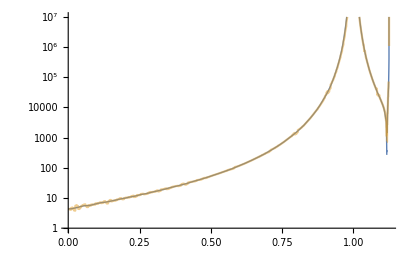

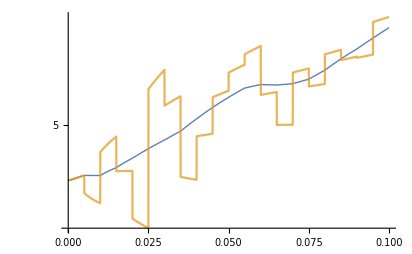

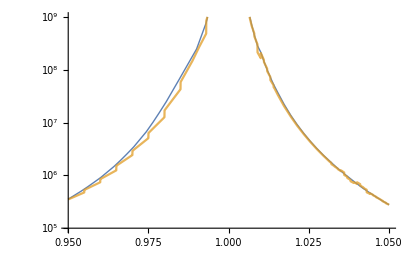

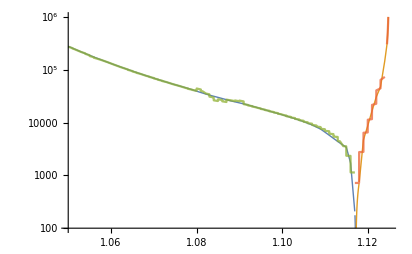

```mathematica
d2Ec[ll_?NumberQ]=D[dEcFndλ[λbar],λbar]/.{λbar->ll}(*the derivative from the interpolated function of the derivative*);

LogPlot[{d2EcFndλ2[λbar]//Abs,d2Ec[λbar]//Abs},{λbar,0,9/8},PlotRange->{1,10^7},PlotStyle->{Thick,Opacity[0.5]}]
LogPlot[{d2EcFndλ2[λbar],d2Ec[λbar]},{λbar,0,0.1},PlotStyle->{Thick,Opacity[0.75]}]
LogPlot[{d2EcFndλ2[λbar],d2Ec[λbar]},{λbar,0.95,1.05},PlotRange->{10^5,10^9},PlotStyle->{Thick,Opacity[0.75]}]
LogPlot[{d2EcFndλ2[λbar],-d2EcFndλ2[λbar],d2Ec[λbar],-d2Ec[λbar]},{λbar,1.05,9/8},PlotRange->{100,10^6},PlotStyle->{Thick,Thick,Opacity[0.75],Opacity[0.75]}]

Clear[d2Ec]
```

# Test

Integrating result and comparing with (Ē)_c'(λ̄)

```mathematica
(*tab=Table[{λbar,NIntegrate[d2EcFndλ2[ll],{ll,0,λbar}]//Quiet},{λbar,Select[alllbarTab,#<1&]}];
tab=tab~Join~Table[{λbar,dEcFndλ[1.12499]-NIntegrate[d2EcFndλ2[ll],{ll,λbar,1.12499}]//Quiet},{λbar,Select[alllbarTab,#>1&]}];
ListLogPlot[{DEcritTab//Abs,tab//Abs}]
Clear[tab]*)
```

### Plots

(Ē)_c(λ̄):

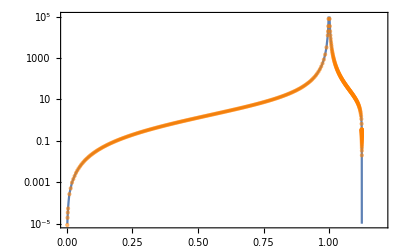

```mathematica
p1=LogPlot[EcFn[λbar],{λbar,0,9/8},PlotRange->{{0.0005,1.2},{0.00001,10^5}},Frame->True];
p2=ListLogPlot[EcritTab,Frame->True,PlotStyle->Directive[Orange,Opacity[0.6]]];

Show[p1,p2]

Clear[p1,p2]
```

(Ē)_c'(λ̄):

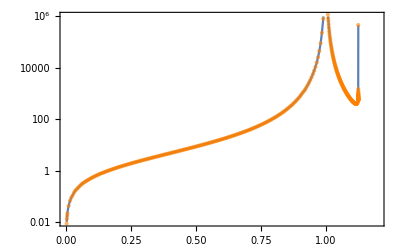

```mathematica
p1=LogPlot[dEcFndλ[λbar]//Abs,{λbar,0,9/8},PlotRange->{{0.0005,1.2},{0.01,10^6}},Frame->True];
p2=ListLogPlot[DEcritTab//Abs,Frame->True,PlotStyle->Directive[Orange,Opacity[0.6]]];

Show[p1,p2]

Clear[p1,p2]
```

(Ē)_c''(λ̄):

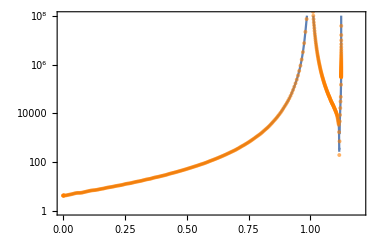

```mathematica
p1=LogPlot[d2EcFndλ2[λbar]//Abs,{λbar,0,9/8},PlotRange->{{0.0005,1.2},{1,10^8}},Frame->True];
p2=ListLogPlot[D2EcritTab//Abs,Frame->True,PlotStyle->Directive[Orange,Opacity[0.6]]];

Show[p1,p2]

Clear[p1,p2]
```

### Full vs. Thin vs. Thick vs. Approximate

We are interested in a simple, one-term, analytic expression for (Ē)_c(λ̄) that may approximately capture the behavior for all λ̄.

From the thin wall analysis we know the asymptotic behavior as λ̄→1:

```mathematica
Normal@Series[Ectwa[λbar],{λbar,1,-2}]
```

(8 π)/(81 (-1+λbar)^2)

From our thick wall analysis we know the asymptotic behavior as λ̄→0 or λ̄→9/8:

```mathematica
limEcThick["cold"][λbar]
limEcThick["hot"][λbar]
```

2.15608 λbar^2

113.05 (9/8-λbar)^(3/4)

Thus, we simply fit a non-linear model to the two regimes and slap them together:

(1.14099 λbar^2)/(1-λbar)^2

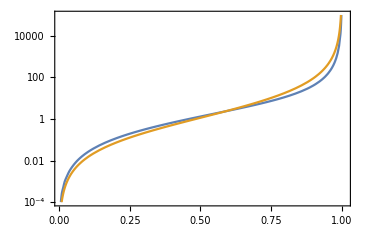

```mathematica
data=Table[{Log10[λbar],Log10[EcFn[λbar]]},{λbar,10^-2,0.999,0.001}];
Normal@NonlinearModelFit[data,a+2Ll-2Log10[(1-10^(Ll))],{a},Ll];
EcAnCold[λbar_]=10^(%/.Ll->Log10[λbar])
LogPlot[{EcFn[λbar],%},{λbar,0,1},PlotRange->{{0.005,1.01},{0.0001,10^5}},Frame->True]
Clear[data]
```

(1.64419 (9/8-λbar)^(3/4))/(1-λbar)^2

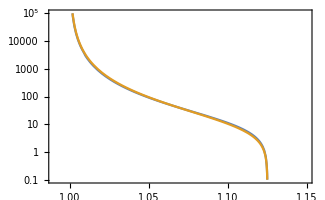

```mathematica
data=Table[{Log10[λbar],Log10[EcFn[λbar]]},{λbar,1.001,1.124,0.001}];
Normal@NonlinearModelFit[data,a+3/4 Log10[9/8-10^Ll]-2Log10[(1-10^(Ll))],{a},Ll];
EcAnHot[λbar_]=((10^(%/.Ll->Log10[λbar]))//Chop)
LogPlot[{EcFn[λbar],%},{λbar,1,9/8},PlotRange->{{0.99,1.15},{0.1,10^5}},Frame->True]
Clear[data]
```

Therefore we simply construct the expression:

```mathematica
EcAn[λbar_]:=Which[0≤λbar<1,EcAnCold[λbar],9/8≥λbar>1,EcAnHot[λbar],λbar==1,∞]
```

Which, we can see, agrees with the full result to within a factor of ~3 for the cold PT, and a factor of ~1 for the hot PT. Good enough!

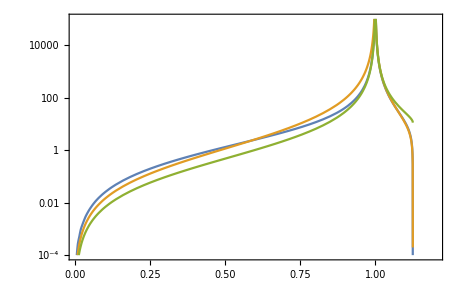

```mathematica
LogPlot[{EcFn[λbar],EcAn[λbar],Ectwa[λbar],EcThick["cold"],EcThick["hot"],Ectwa[λbar]+EcThick["cold"]},{λbar,0,9/8},PlotRange->{{0.005,1.2},{0.0001,10^5}},Frame->True]
```

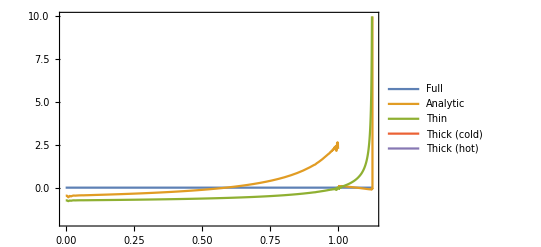

```mathematica
Plot[{0,EcAn[λbar]/EcFn[λbar]-1,Ectwa[λbar]/EcFn[λbar]-1,EcThick["cold"]/EcFn[λbar]-1,EcThick["hot"]/EcFn[λbar]-1},{λbar,0,9/8},Frame->True,PlotRange->{-2,10},PlotLegends->{"Full","Analytic","Thin","Thick (cold)","Thick (hot)"}]
```

## 3. Important Physical Quantities

## 3.1 Temperature function

### T_low and T_high

These will be shorthand names for the lowest and highest temperatures allowed (close to the binodal and spinodal temperatures):

```mathematica
TLow=(T/.TToλbar)/.λbar->Rationalize[alllbarTab⟦2⟧]
THigh=(T/.TToλbar)/.λbar->Rationalize[alllbarTab⟦-2⟧]
```

Tc √((4 A^2-3 λ μ^2)/(A^2/250-3 λ μ^2))

Tc √((4 A^2-3 λ μ^2)/((112499 A^2)/25000-3 λ μ^2))

### Transition strength α_n and runaway threshold strength α_∞

We start by defining a “master list” whose i-th entry consists of the the following information about the i-th particle of the dark sector:

{type, N_i, g_i},

where type = “B”/“F” denotes boson/fermion, N_i is the degrees of freedom of the i-th particle, and g_i is its coupling to the higgs χ.

μ^2/2=1/24∑_i c_i g_i^2,

A/3=1/(12π)∑_B g_B^2,

a=π^2/30 g_*=π^2/30∑_(m_i<<T) c_i',

where g_* is the usual number of relativistic d.o.f. in the dark sector plasma.

```mathematica
Clear[cType,cprimeType,μFromList,AFromList,aFromList]

(*Boson/Fermion factor in Subscript[V, T](T)*)
cType[type_String]:=Which[type=="B",1,type=="F",1/2]

(*Boson/Fermion factor in Subscript[ρ, rad](T)*)
cprimeType[type_String]:=Which[type=="B",1,type=="F",7/8]

(*μ-coefficient in thermal potential Subscript[V, T]*)
μFromList[particleContent_List]:=√(1/12 Total[cType[#⟦1⟧]*#⟦2⟧*(#⟦3⟧)^2&/@particleContent]);

(*A-coefficient in thermal potential Subscript[V, T]*)
AFromList[particleContent_List]:=1/(4π)Total[cType[#⟦1⟧]*#⟦2⟧*(#⟦3⟧)^3&/@particleContent];

(*a-coefficient in Subscript[ρ, rad](T) (a=π^2/30 g_*). Note only massless particles contribute to it*)
aFromList[particleContent_List,scalarValue_]:=π^2/30 Total[cprimeType[#⟦1⟧]*#⟦2⟧*HeavisideTheta[-Rationalize[(#⟦3⟧*scalarValue)]]&/@particleContent]/.{HeavisideTheta[0]->1};
```

Nevertheless we will most likely not bother nailing down the exact particle content of the dark sector. As such, we will be concerned mostly with μ, A, and a directly.

From this, let us write some functions that will help us directly write down the phase transition strength in terms of the relevant parameters.

```mathematica
Clear[α∞,αn]

α∞[gStar_,coeffs_List,Tcrit_,Temp_]:=Block[{μ,A,λ,Tc=Tcrit,T=Temp,λbar,sign,χVEV,aN,res},

(*distributing the coefficients*)
{μ,A,λ}=coeffs;

(*checking whether there can be a first order phase transition*)
noCritTemp[coeffs];

(*λ̄*)
λbar=(λbar/.McλbarToCoeffs);

(*the sign of the mass change Subscript[Δm, i]^2 as the particles move accross the bubble wall: if the PT is cold (subcritical) (λ̄<1) ⇒ Subscript[χ, s]->Subscript[χ, b] and the mass increases; if the PT is hot (supercritical) (λ̄>1) ⇒ Subscript[χ, b]->Subscript[χ, s] and the mass decreases  *)
sign=Sign[1-λbar];

(*the <χ> VEV, i.e. its value in the broken phase*)
χVEV=(Xb/.PotToCoeffs);

(*the coefficient in Subscript[ρ, rad](T)=Subscript[a, N] T^4 (Subscript[a, N]=π^2/30 g_*)*)
aN=π^2/30 gStar;

(*Subscript[α, ∞]*)
res=sign*(χVEV/T)^2*(μ^2/2)/aN;

res
]


αn[gStar_,coeffs_List,Tcrit_,Temp_]:=Block[{μ,A,λ,Tc=Tcrit,T=Temp,ϵ,an,res},

(*distributing the coefficients*)
{μ,A,λ}=coeffs;

(*checking whether there can be a first order phase transition*)
noCritTemp[coeffs];

(*energy density in PT*)
ϵ=(ΔV/.McλbarToCoeffs);

(*the coefficient in Subscript[ρ, rad](T)=Subscript[a, N] T^4 (Subscript[a, N]=π^2/30 g_*)*)
an=π^2/30 gStar;

(*Subscript[α, n]*)
res=ϵ/(an*T^4);

res
]
```

#### Plots, Tests & Examples:

```mathematica
(*cond1[μ,A,λ]*)
```

```mathematica
(*cond2[μ,A,λ]*)
```

```mathematica
(*p1=RegionPlot3D[((cond1[μ,A,λ])&&(cond2[μ,A,λ])),{μ,10^-4,1},{A,10^-4,1},{λ,10^-4,3},PlotStyle->Opacity[0.5],AxesLabel->{"μ","A","λ"}]

(*p2=RegionPlot3D[(μ==A),{μ,10^-4,1},{A,10^-4,1},{λ,10^-4,3},PlotStyle->Directive[Red,Opacity[0.5]]];*)

(*Show[p1,p2]*)

Clear[p1,p2]*)
```

```mathematica
(*Table[RegionPlot[cond1[μ,A,λ]&&cond2[μ,A,λ],{μ,10^-4,2},{A,10^-4,2},FrameLabel->{"μ","A"},PlotLabel->"λ="<>ToString[λ]],{λ,{0.1,0.5,1,2,3}}]*)
```

```mathematica
(*testList=Table[{{"B",nn,1}},{nn,1,20}];
lamTest=1;

gStarTest=Table[Total[#⟦2⟧&/@testList⟦i⟧],{i,Length@testList}];

muTest=Table[μFromList[testList⟦i⟧]//N,{i,Length@testList}];

ATest=Table[AFromList[testList⟦i⟧]//N,{i,Length@testList}];

cond1s=Table[1-(4 ATest⟦i⟧^2)/(3 lamTest muTest⟦i⟧^2),{i,Length@testList}];
cond2s=Table[1+ATest⟦i⟧^2/(8 ATest⟦i⟧^2-6 lamTest muTest⟦i⟧^2),{i,Length@testList}];

p1=ListPlot[muTest,Frame->True,PlotStyle->Blue,PlotLegends->{"μ"},PlotLabel->"λ="<>ToString[lamTest],FrameLabel->{"N_scalars",None}];
p2=ListPlot[ATest,Frame->True,PlotStyle->Red,PlotLegends->{"A"}];
Show[p1,p2]
Clear[p1,p2]

p1=ListPlot[cond1s,Frame->True,PlotStyle->Orange,PlotLegends->{"Tc exists"},PlotLabel->"λ="<>ToString[lamTest],FrameLabel->{"N_scalars",None}];
p2=ListPlot[cond2s,Frame->True,PlotStyle->Darker@Green,PlotLegends->{"Tspin exists"}];

Show[p1,p2]
Clear[p1,p2]

Clear[testList,lamTest,gStarTest,muTest,ATest,cond1s,cond2s]*)
```

```mathematica
(*testList={{"B",7,1}};
(*testList={{"B",10,0.7},{"F",0,1}};*)

gStarTest=Total[#⟦2⟧&/@testList]

muTest=μFromList[testList]//N

ATest=AFromList[testList]//N

lamTest=1;

aFromList[testList,0]

cond1[muTest,ATest,lamTest]

cond2[muTest,ATest,lamTest]

Timing[α∞[gStarTest,{muTest,ATest,lamTest},10,10.1]]

Timing[αn[gStarTest,{muTest,ATest,lamTest},10,10.1]]

Clear[testList,gStarTest,muTest,ATest,lamTest]*)
```

### Critical energy E_c(T)

We start by noting that E_c=χ_b^2/M(Ē)_c=T_c·χ_b^2/(M T_c)·(Ē)_c. We can then define our critical energy function in terms of the potential coefficients {μ,A,λ} (in that order) and T_c and T:

```mathematica
Clear[EcTemp]

EcTemp[coeffs_List,Tcrit_,Temp_]:=Block[{μ,A,λ,Tc=Tcrit,T=Temp,θ,λbar,dim,ec},

(*distributing the coefficients*)
{μ,A,λ}=coeffs;

(*checking whether there can be a first order phase transition*)
noCritTemp[coeffs];

(*θ≡T/Subscript[T, c]*)
θ=T/Tc;

(*λ̄*)
λbar=(λbar/.McλbarToCoeffs);

(*Subscript[χ, b]^2/(M·Subscript[T, c]): the dimensionality of Subscript[E, c], in units of Subscript[T, c]*)
dim=(Xb^2/(M*Tc)/.PotToCoeffs);

(*Subscript[E, c]*)
ec=Tc*dim*EcFn[λbar];

ec
]
```

Note that, depending on the potential coefficients, not all values of T will yield sensible values. In particular, T should be located between the binodal and spinodal temperatures.

#### Tests & Examples:

```mathematica
testCoeffs={0.2,0.1,1}(*μ, A, λ*);
{testμ,testA,testλ}=testCoeffs;
testTc=10(*[TeV]*);

testTbin=T0/.Tbinodal/.{μ->testμ,A->testA,λ->testλ,Tc->testTc}(*binodal temperature T0*)
(*TLow/.{μ->testμ,A->testA,λ->testλ,Tc->testTc}(*lowest temperature probed by interpolation*)

THigh/.{μ->testμ,A->testA,λ->testλ,Tc->testTc}(*highest temperature probed by interpolation*)*)
testTspin=Ts/.Tspinodal/.{μ->testμ,A->testA,λ->testλ,Tc->testTc}(*spinodal temperature Ts*)

EcTemp[testCoeffs,testTc,testTbin](*at T=T0*)
EcTemp[testCoeffs,testTc,testTbin*1.1](*at T=1.1*T0*)
EcTemp[testCoeffs,testTc,testTspin*0.9](*at T=0.9*Ts*)
EcTemp[testCoeffs,testTc,testTspin](*at T=Ts*)

Clear[testCoeffs,testμ,testA,testλ,testTc,testTbin,testTspin]
```

8.16497

10.328

3.41696×10^-21

43.6479

103.755

4.82482×10^-9

### Action S_E(T)

S_E=E_c/T=P_S·(Ē)_c, with P_S≡χ_b^2/(M T).

```mathematica
Clear[SETemp]

SETemp[coeffs_List,Tcrit_,Temp_]:=Block[{Tc=Tcrit,T=Temp,Ecrit},

(*Subscript[E, c]*)
Ecrit=EcTemp[coeffs,Tc,T];

(*Subscript[S, E]=Subscript[E, c]/T*)
Ecrit/T
]
```

First derivative w.r.t. λ̄:
(d S_E)/(d λ̄)=(d P_S)/(d λ̄)(Ē)_c+P_S(d (Ē)_c)/(d λ̄),
and second derivative w.r.t. λ̄:
(d^2 S_E)/(d (λ̄)^2)=(d^2 P_S)/(d (λ̄)^2)(Ē)_c+2(d P_S)/(d λ̄)(d (Ē)_c)/(d λ̄)+P_S(d^2 (Ē)_c)/(d (λ̄)^2)

```mathematica
Clear[dSdλ,d2Sdλ2]

dSdλ[coeffs_List,Tcrit_,Temp_]:=Block[{μ,A,λ,Tc=Tcrit,T=Temp,θ,λbar,ds},

(*distributing the coefficients*)
{μ,A,λ}=coeffs;

(*checking whether there can be a first order phase transition*)
noCritTemp[coeffs];

(*θ≡T/Subscript[T, c]*)
θ=T/Tc;

(*λ̄*)
λbar=(λbar/.McλbarToCoeffs);

(*Subscript[dS, E]/(d λ̄)*)
ds=dPSdλ*EcFn[λbar]+PS*dEcFndλ[λbar];

ds
]



d2Sdλ2[coeffs_List,Tcrit_,Temp_]:=Block[{μ,A,λ,Tc=Tcrit,T=Temp,θ,λbar,dds},

(*distributing the coefficients*)
{μ,A,λ}=coeffs;

(*checking whether there can be a first order phase transition*)
noCritTemp[coeffs];

(*θ≡T/Subscript[T, c]*)
θ=T/Tc;

(*λ̄*)
λbar=(λbar/.McλbarToCoeffs);

(*(d^2 Subscript[S, E])/(d(λ̄)^2)*)
dds=d2PSdλ2*EcFn[λbar]+2*dPSdλ*dEcFndλ[λbar]+PS*d2EcFndλ2[λbar];

dds
]
```

First derivative w.r.t. ln T:
(d S_E)/(d ln T)=(d λ̄)/(d ln T)(d S_E)/(d λ̄),
and second derivative w.r.t. T:
(d^2 S_E)/(d ln T^2)=(d^2 λ̄)/(d ln T^2)(d S_E)/(d λ̄)+((d λ̄)/(d ln T))^2(d^2 S_E)/(d (λ̄)^2)

```mathematica
Clear[dSdlnT,d2SdlnT2]

dSdlnT[coeffs_List,Tcrit_,Temp_]:=Block[{μ,A,λ,Tc=Tcrit,T=Temp,θ,λbar,res},

(*distributing the coefficients*)
{μ,A,λ}=coeffs;

(*checking whether there can be a first order phase transition*)
noCritTemp[coeffs];

(*θ≡T/Subscript[T, c]*)
θ=T/Tc;

(*λ̄*)
λbar=(λbar/.McλbarToCoeffs);

(*Subscript[dS, E]/dlnT*)
res=dλdlnT*dSdλ[coeffs,Tc,T];

res
]



d2SdlnT2[coeffs_List,Tcrit_,Temp_]:=Block[{μ,A,λ,Tc=Tcrit,T=Temp,θ,λbar,res},

(*distributing the coefficients*)
{μ,A,λ}=coeffs;

(*checking whether there can be a first order phase transition*)
noCritTemp[coeffs];

(*θ≡T/Subscript[T, c]*)
θ=T/Tc;

(*λ̄*)
λbar=(λbar/.McλbarToCoeffs);

(*(d^2 Subscript[S, E])/dlnT^2*)
res=d2λdlnT2*dSdλ[coeffs,Tc,T]+dλdlnT^2*d2Sdλ2[coeffs,Tc,T];

res
]
```

#### Tests and Examples

```mathematica
{muTest,ΔTest,λTest}={1,8/9+0.02,1};
ATest=A/.(ARule/.{μ->muTest,Δ->ΔTest,λ->λTest});
coeffsTest={muTest,ATest,λTest}

TcTest=500;
TempTest=2000;

(λbar/.McλbarToCoeffs)/.{μ->muTest,A->ATest ,λ->λTest,T->TempTest,Tc->TcTest}

SETemp[coeffsTest,TcTest,TempTest]

dSdλ[coeffsTest,TcTest,TempTest]
d2Sdλ2[coeffsTest,TcTest,TempTest]

dλdlnT/.{μ->muTest,A->ATest ,λ->λTest,T->TempTest,Tc->TcTest}
d2λdlnT2/.{μ->muTest,A->ATest ,λ->λTest,T->TempTest,Tc->TcTest}

dSdlnT[coeffsTest,TcTest,TempTest]
d2SdlnT2[coeffsTest,TcTest,TempTest]

Clear[muTest,ATest,ΔTest,λTest,coeffsTest,TcTest,TempTest]
```

{1,0.825631,1}

1.09398

121.852

-5879.23

208562.

0.0125306

-0.0250611

-73.67

180.088

### Nucleation rate Γ_nucl/𝒱(T)

The bubble nucleation rate (really, rate per unit volume 𝒱) is given by

Γ_nucl/𝒱≈K·T^4·(S_E/(2π))^(3/2)e^-S_E,

where S_E=E_c/T is the Euclidean action, and K some numerical coefficient.

```mathematica
Clear[Γnucl]

Γnucl[coeffs_List,Tcrit_,Temp_,Kfactor_:1,full_:False,yieldLog_:False]:=Block[{θ,action,pref,res},

(*θ≡T/Subscript[T, c]*)
θ=Temp/Tcrit;

(*Subscript[S, E]*)
action=SETemp[coeffs,Tcrit,Temp];

(*the prefactor from the 0-modes in the path integral*)
pref=If[full,(action/(2π))^(3/2),1];

(*Subscript[Γ, nucl]/𝒱 vs. log10(Subscript[Γ, nucl]/𝒱). log10(x)=ln(x)/ln(10). It will be useful when computing Subscript[T, PT].*)
res=If[yieldLog,(Log[Kfactor]+4*Log[Tcrit]+4*Log[θ]+Log[pref]-action)/Log[10],
Kfactor*(Tcrit^4)*(θ^4)*pref*Exp[-action]];

res
]
```

#### Tests & Examples:

```mathematica
(*testCoeffs={0.2,0.1,1}(*μ, A, λ*);
testTc=10(*[TeV]*);
testT=0.9*testTc;*)


testCoeffs={1,0.82,1}(*μ, A, λ*);
testTc=10(*[TeV]*);
testT=2*testTc;

{testμ,testA,testλ}=testCoeffs;

testTbin=T0/.Tbinodal/.{μ->testμ,A->testA,λ->testλ,Tc->testTc}(*binodal temperature T0*)
(*TLow/.{μ->testμ,A->testA,λ->testλ,Tc->testTc}(*lowest temperature probed by interpolation*)

THigh/.{μ->testμ,A->testA,λ->testλ,Tc->testTc}(*highest temperature probed by interpolation*)*)
testTspin=Ts/.Tspinodal/.{μ->testμ,A->testA,λ->testλ,Tc->testTc}(*spinodal temperature Ts*)

(*action*)
EcTemp[testCoeffs,testTc,testT]/(testT)
SETemp[testCoeffs,testTc,testT]

(*nucleation rate, with (S/2π)^(3/2) prefactor*)
Γnucl[testCoeffs,testTc,testT,1,True]

(*nucleation rate, w/o prefactor*)
Γnucl[testCoeffs,testTc,testT,1,False]

(*testing the ratio matches the prefactor*)
(%%/%)/(%%%/(2π))^(3/2)

(*Subscript[log, 10] of nucleation rate, w/ prefactor*)
Γnucl[testCoeffs,testTc,testT,1,True,True]

Clear[testCoeffs,testμ,testA,testλ,testTc,testT,testTbin,testTspin]
```

3.21662

0.-34.6857 ⅈ

170.949

170.949

1.3006×10^-67

9.16465×10^-70

1.

-66.8859

### Scale-invariant transition rate parameters

We define (β̄)_1 and (β̄)_2 as the first and second derivatives of ln(Γ_nucl/𝒱) w.r.t. ln T. They can be written in terms of the corresponding derivatives of S_E:

(β̄)_1≡(d ln Γ_nucl)/(d ln T)=4+(d S_E)/(d ln T)(-1+(3/2)/S_E)

(β̄)_2≡(d^2 ln Γ_nucl)/(d ln T^2)=(d^2 S_E)/(d ln T^2)(-1+(3/2)/S_E)-2/3((3/2)/S_E(d S_E)/(d ln T))^2

```mathematica
Γ=k T^4 (S[T]/(2π))^(f*3/2)Exp[-S[T]](*functional form of Γ*)
β1=(T D[Log[Γ],T])//Simplify(*Subscript[β̄, 1]*)
Collect[(β1/.{S'[T]->dS/T})//FullSimplify,{dS,f}](*Subscript[β̄, 1], in terms of dS=dS/dlnT*)

β2=(T D[β1,T])//FullSimplify(*Subscript[β̄, 2]*)
Collect[(β2/.{S'[T]->1/T dS,S''[T]->ddS/T^2-dS/T^2}),{ddS,dS,f}](*Subscript[β̄, 2], in terms of dS=dS/dlnT & ddS=(d^2 S)/dlnT^2*)

Clear[Γ,β1,β2]
```

ⅇ^(-S[T]) k (2 π)^(-3 f/2) T^4 S[T]^(3 f/2)

4+(-T+(3 f T)/(2 S[T])) S'[T]

4+dS (-1+(3 f)/(2 S[T]))

1/(2 S[T]^2)T (S'[T] (3 f S[T]-2 S[T]^2-3 f T S'[T])+T (3 f-2 S[T]) S[T] S''[T])

ddS (-1+(3 f)/(2 S[T]))-(3 dS^2 f)/(2 S[T]^2)

```mathematica
Clear[βbar1,βbar2]

βbar1[coeffs_List,Tcrit_,Temp_,Kfactor_:1,full_:False]:=Block[{SE,dSE,extra,betabar1},

(*Subscript[S, E]*)
SE=SETemp[coeffs,Tcrit,Temp];

(*Subscript[dS, E]/dlnT*)
dSE=dSdlnT[coeffs,Tcrit,Temp];

(*extra term coming from derivative of the prefactor from the 0-modes of the path integral*)
extra=(3/2)/SE Boole[full];

(*Subscript[β̄, 1]*)
betabar1=4+dSE*(-1+extra);

betabar1
]



βbar2[coeffs_List,Tcrit_,Temp_,Kfactor_:1,full_:False]:=Block[{SE,dSE,ddSE,extra,betabar2},

(*Subscript[S, E]*)
SE=SETemp[coeffs,Tcrit,Temp];

(*Subscript[dS, E]/dlnT*)
dSE=dSdlnT[coeffs,Tcrit,Temp];

(*(d^2 Subscript[S, E])/dlnT^2*)
ddSE=d2SdlnT2[coeffs,Tcrit,Temp];

(*extra term coming from derivative of the prefactor from the 0-modes of the path integral*)
extra=(3/2)/SE Boole[full];

(*Subscript[β̄, 2]*)
betabar2=ddSE(-1+extra)-2/3(extra*dSE)^2;

betabar2
]
```

#### Tests & Examples

```mathematica
(*testCoeffs={0.2,0.1,1}(*μ, A, λ*);
{testμ,testA,testλ}=testCoeffs;
testTc=10(*[TeV]*);

(*transition rate, with derivative of (S/2π)^(3/2) prefactor*)
βbar[testCoeffs,testTc,testTc*0.97]

(*transition rate, w/o derivative of prefactor*)
βbar[testCoeffs,testTc,testTc*.97,1,True]

Clear[testCoeffs,testμ,testA,testλ,testTc,testTbin,testTspin]*)
```

```mathematica
testCoeffs={0.2,0.1,1}(*μ, A, λ*);
{testμ,testA,testλ}=testCoeffs;
testTc=10(*[TeV]*);

(*transition rate, with derivative of (S/2π)^(3/2) prefactor*)
βbar1[testCoeffs,testTc,testTc*0.97]

(*transition rate, w/o derivative of prefactor*)
βbar1[testCoeffs,testTc,testTc*.97,1,True]

(*transition rate, with derivative of (S/2π)^(3/2) prefactor*)
βbar2[testCoeffs,testTc,testTc*0.97]

(*transition rate, w/o derivative of prefactor*)
βbar2[testCoeffs,testTc,testTc*.97,1,True]

Clear[testCoeffs,testμ,testA,testλ,testTc,testTbin,testTspin]
```

-2686.43

-2604.49

-243202.

-240272.

## 3.2 Time evolution

### Evolution of temperature T(t)

#### Analytic

In an analytic approximation, we parameterize the temperature evolution with a single power law

T(t)=(T_c((t-t_0)/(t_c-t_0)))^γ.

```mathematica
Clear[tempEvolAn,tOfTempAn]

tempEvolAn[Tcrit_,tcrit_,gamma_,t0_,t_]:=Tcrit*((t-t0)/(tcrit-t0))^gamma

tOfTempAn[Tcrit_,tcrit_,gamma_,t0_,Temp_]:=(tcrit-t0)*(Temp/Tcrit)^(1/gamma)+t0
```

From this:

(d lnT)/(d t)=γ/(t-t_0)
(d^2 ln T)/(d t^2)=-γ/(t-t_0)^2

```mathematica
D[Log[tempEvolAn[Tc,tc,γ,t0,t]],t]
D[Log[tempEvolAn[Tc,tc,γ,t0,t]],{t,2}]
```

γ/(t-t0)

-γ/(t-t0)^2

#### Numeric

However, we will also accommodate numerical (i.e. interpolated) functions.

Below, we define functions to:

1. find the time and temperature at which the temperature reaches its maximum value, and
2. find the time at which the temperature reaches a specific value

```mathematica
Clear[tTMax,tOfTempNum]

tTMax[Tfn_,argScale_:1]:=tTMax[Tfn,argScale]=Block[{dTdx,xA,xB,xData,prec,Tmx,xmx,result,eps=10^-6},
(*NOTE: CRUCIAL FOR NUMERICAL METHOD: we assume T(t) is a concave function, and that therefore it has a maximum in its domain. True during reheating.*)

(*derivative*)
dTdx[x_]=D[Tfn[x],x];

(*anatomy of the interpolating function*)
{xA,xB}=(InterpolatingFunctionDomain[Tfn]//Flatten);
xData=(InterpolatingFunctionCoordinates[Tfn]//Flatten);
prec=Round[Precision[xData⟦1⟧]];

(*slightly away from the leftmost edge*)
xA=If[xA<=0,eps,Min[xData⟦2⟧,xA*(1+eps)]];
Clear[xData];

(*searching for the time at which we get the maximum temperature*)
{Tmx,xmx}=FindMaximum[Log10[SetPrecision[Tfn[10^Lx],prec]],{Lx,0,Log10[xA],Log10[xB]},MaxIterations->10^6,WorkingPrecision->prec,AccuracyGoal->6,PrecisionGoal->4];
Tmx=10^Tmx;
xmx=10^(Lx/.xmx);

result={xmx*argScale,Tmx}
]

tOfTempNum[Tfn_,Temp_,argScale_:1]:=tOfTempNum[Tfn,Temp,argScale]=Block[{xA,xB,xData,yData,prec,Tmx,xmx,xLSet,xRSet,yLSet,yRSet,xLGuess,xRGuess,xLe,xRi,result,eps=10^-6},
(*NOTE: CRUCIAL FOR NUMERICAL METHOD: we assume T(t) is a concave function, and that therefore it has a maximum in its domain. True during reheating.*)

(*anatomy of the interpolating function*)
{xA,xB}=(InterpolatingFunctionDomain[Tfn]//Flatten);
xData=(InterpolatingFunctionCoordinates[Tfn]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[Tfn]//Flatten);
prec=Round[Precision[xData⟦1⟧]];

(*slightly away from the leftmost edge*)
xA=If[xA<=0,eps,Min[xData⟦2⟧,xA*(1+eps)]];

(*searching for the time at which we get the maximum temperature*)
{xmx,Tmx}=tTMax[Tfn,1];

(*testing whether Temp is in the probed temperature interval*)
If[IntervalMemberQ[Interval[{Max[Tfn[xA],Tfn[xB]],Tmx}],Temp]==False,Message[tOfTempNum::NoTemp, Temp,{Max[Tfn[xA],Tfn[xB]],Tmx}];Abort[]];

(*the initial guesses for the crossing times*)
If[(Length@yData != Length@xData),
xLGuess=GeometricMean[{xA,xmx}];
xRGuess=GeometricMean[{xB,xmx}],

xLSet=Select[xData,(#<xmx)&];
yLSet=yData⟦1;;Length@xLSet⟧;
yLSet=Abs[yLSet-Temp];

xLGuess=(Position[yLSet,Min[yLSet]]//Flatten)⟦1⟧;
xLGuess=xLSet⟦xLGuess⟧;

xRSet=Select[xData,(#>xmx)&];

yRSet=yData⟦(Length@yData-Length@xRSet)+1;;-1⟧;
yRSet=Abs[yRSet-Temp];

xRGuess=(Position[yRSet,Min[yRSet]]//Flatten)⟦1⟧;
xRGuess=xRSet⟦xRGuess⟧;

Clear[xLSet,xRSet,yLSet,yRSet,xData,yData];
	];

(*times at which the temperature is equal to some value. Since T(t) is concave, there are *two* such times. In increasing order: *)

xLe=(10^Logx)/.FindRoot[Log10[SetPrecision[Tfn[10^Logx],prec]]-Log10[SetPrecision[Temp,prec]],{Logx,Log10[xLGuess],Log10[xA],Log10[xmx*(1-eps)]},MaxIterations->10^6,WorkingPrecision->prec,AccuracyGoal->6,PrecisionGoal->4];

xRi=(10^Logx)/.FindRoot[Log10[SetPrecision[Tfn[10^Logx],prec]]-Log10[SetPrecision[Temp,prec]],{Logx,Log10[xRGuess],Log10[xmx*(1+eps)],Log10[xB]},MaxIterations->10^6,WorkingPrecision->prec,AccuracyGoal->6,PrecisionGoal->4];

(*the results*)
result=argScale*{xLe,xRi};

result
]
tOfTempNum::NoTemp="The temperature Temp=`1` is not in the interval `2` of temperatures probed by the Tfn function.";
```

Function to check whether a specified temperature is ever reached:

```mathematica
Clear[noTempFn]

noTempFn[Tfn_,Temp_,argScale_:1]:=Block[{xA,xB,xData,Tmx,xmx,Tmin,eps=10^-6},

(*anatomy of the interpolating function*)
{xA,xB}=(InterpolatingFunctionDomain[Tfn]//Flatten);
xData=(InterpolatingFunctionCoordinates[Tfn]//Flatten);

(*slightly away from the leftmost edge*)
xA=If[xA<=0,eps,Min[xData[[2]],xA*(1+eps)]];
Clear[xData];

(*searching for the time at which we get the maximum temperature*)
{xmx,Tmx}=tTMax[Tfn,1];

(*lowest temperature, depending on direction*)
Tmin=Max[Tfn[xB],Tfn[xA]];

If[IntervalMemberQ[Interval[{Tmin,Tmx}],Temp]==False,Message[noTempFn::NoTemp, Temp,{Tmin,Tmx}];Abort[]]
]
 noTempFn::NoTemp = "The temperature Temp=`1` is not in the interval `2` of temperatures probed by the Tfn function.";
```

#### Tests & Examples

0.169124

{1.176474319779719,581.417541394076}

{0.7708293033841647,2.97815383012368}

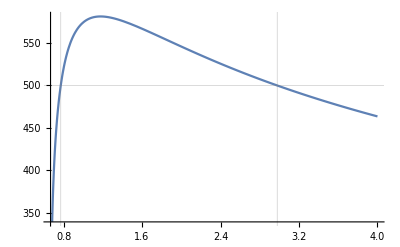

tOfTempNum::NoTemp: The temperature Temp=1000 is not in the interval {38.1928,581.417541394076} of temperatures probed by the Tfn function.

$Aborted

noTempFn::NoTemp: The temperature Temp=0.1 is not in the interval {38.1928,581.417541394076} of temperatures probed by the Tfn function.

$Aborted

```mathematica
Needs["DSReheating`"]

testTc=500(*[GeV]*);
testtc=((2*10^18)/testTc^2)*1/10(*roughly Hubble time at Tc [GeV^-1]*);
testTfn=TOfx[0.1,10,1/testtc];

dlnTtTest[t_]=D[Log[testTfn[t]],t];

dlnTtTest[1]

tTMax[testTfn]

tOfTempNum[testTfn,testTc,1]
Plot[testTfn[t],{t,2/3,4},GridLines->{%,{testTc}}]

tOfTempNum[testTfn,1000,1]
noTempFn[testTfn,0.1,1]

Clear[testTc,testtc,testTfn,dlnTtTest]
```

### Action rate change

Using the chain rule and our expressions for (d S_E)/(d lnT) and (d^2 S_E)/(d lnT^2), we get

```mathematica
Clear[S1Rate,S2Rate]

(*general formula for Subscript[dS, E]/dt*)
S1Rate[dlnTdt_,coeffs_List,Tcrit_,Temp_]:=dlnTdt*dSdlnT[coeffs,Tcrit,Temp]

(*general formula for (d^2 Subscript[S, E])/dt^2*)
S2Rate[dlnTdt_,d2lnTdt2_,coeffs_List,Tcrit_,Temp_]:=d2lnTdt2*dSdlnT[coeffs,Tcrit,Temp]+dlnTdt^2*d2SdlnT2[coeffs,Tcrit,Temp]
```

For the analytic, single-power law of the temperature, we have:

S_1(t)=γ/(t-t_0)(d S_E)/(d lnT)(T)
S_2(t)=-γ/(t-t_0)^2(d S_E)/(d lnT)(T) + (γ/(t-t_0))^2(d^2 S_E)/(d lnT^2)

```mathematica
Clear[S1An,S2An,S1OfTempAn,S2OfTempAn]

(*analytic approximation*)
S1An[gamma_,t0_,time_,coeffs_List,Tcrit_,Temp_]:=S1Rate[gamma/(time-t0),coeffs,Tcrit,Temp]

S2An[gamma_,t0_,time_,coeffs_List,Tcrit_,Temp_]:=S2Rate[gamma/(time-t0),-gamma/(time-t0)^2,coeffs,Tcrit,Temp]

(*analytic approximation, as a function of temperature and not time*)
S1OfTempAn[gamma_,t0_,tcrit_,coeffs_List,Tcrit_,Temp_]:=S1An[gamma,t0,tOfTempAn[Tcrit,tcrit,gamma,t0,Temp],coeffs,Tcrit,Temp]

S2OfTempAn[gamma_,t0_,tcrit_,coeffs_List,Tcrit_,Temp_]:=S2An[gamma,t0,tOfTempAn[Tcrit,tcrit,gamma,t0,Temp],coeffs,Tcrit,Temp]
```

### Transition rate parameters

Using the chain rule and our definitions of (β̄)_1 and (β̄)_2, we have:

β_1(t)≡(d ln Γ_nucl)/(d t)=(d ln T)/dt(β̄)_1(T)

β_2(t)≡(d^2 ln Γ_nucl)/(d t^2)=(d^2 ln T)/dt^2(β̄)_1(T)+((d ln T)/dt)^2(β̄)_2(T)

```mathematica
Clear[β1Rate,β2Rate]

(*general formula for Subscript[β, 1]*)
β1Rate[dlnTdt_,coeffs_List,Tcrit_,Temp_,Kfactor_:1,full_:False]:=dlnTdt*βbar1[coeffs,Tcrit,Temp,Kfactor,full]

(*general formula for Subscript[β, 2]*)
β2Rate[dlnTdt_,d2lnTdt2_,coeffs_List,Tcrit_,Temp_,Kfactor_:1,full_:False]:=d2lnTdt2*βbar1[coeffs,Tcrit,Temp,Kfactor,full]+dlnTdt^2*βbar2[coeffs,Tcrit,Temp,Kfactor,full]
```

For the analytic, single-power law of the temperature, we have:

β_1(t)=γ/(t-t_0)(β̄)_1(T)
β_2(t)=-γ/(t-t_0)^2(β̄)_1(T)+(γ/(t-t_0))^2(β̄)_2(T)

```mathematica
Clear[beta1An,beta2An,beta1OfTempAn,beta2OfTempAn]

(*analytic approximation*)
beta1An[gamma_,t0_,time_,coeffs_List,Tcrit_,Temp_,Kfactor_:1,full_:False]:=β1Rate[gamma/(time-t0),coeffs,Tcrit,Temp,Kfactor,full]
beta2An[gamma_,t0_,time_,coeffs_List,Tcrit_,Temp_,Kfactor_:1,full_:False]:=β2Rate[gamma/(time-t0),-gamma/(time-t0)^2,coeffs,Tcrit,Temp,Kfactor,full]

(*analytic approximation, as a function of temperature and not time*)
beta1OfTempAn[gamma_,t0_,tcrit_,coeffs_List,Tcrit_,Temp_,Kfactor_:1,full_:False]:=beta1An[gamma,t0,tOfTempAn[Tcrit,tcrit,gamma,t0,Temp],coeffs,Tcrit,Temp,Kfactor,full]
beta2OfTempAn[gamma_,t0_,tcrit_,coeffs_List,Tcrit_,Temp_,Kfactor_:1,full_:False]:=beta2An[gamma,t0,tOfTempAn[Tcrit,tcrit,gamma,t0,Temp],coeffs,Tcrit,Temp,Kfactor,full]
```

### Fractional volume h(t)

h(t)=exp[-∫_t_c^t ⅆt' Γ_nucl/𝒱(t')·(4π)/3(v_w^3(t-t'))^3] 

We also allow for the inclusion of the scale factor function a(t):

h(t)=exp[-∫_t_c^t ⅆt' Γ_nucl/𝒱(t')·(4π)/3(v_w a(t')∫_t'^t dt''/(a(t'')))^3] 

[see A. H. Guth & E. J. Weinberg 1981. Note that in their paper a(t) grows exponentially since at the time of the transition the Universe is vacuum dominated; in our case this will not be true]

For simplicity, we will compute & interpolate the log_10 of the exponent, as a function of log_10 of time instead:

log_10[-ln h(log_10(t))]

```mathematica
Clear[Lmlnh]

Lmlnh[direction_,vw_,TempEvol_List,coeffs_List,Tcrit_,Kfactor_:1,full_:False,scaleFactor_:1,Nlx_:250]:=Lmlnh[direction,vw,TempEvol,coeffs,Tcrit,Kfactor,full,scaleFactor,Nlx]=Block[{μ,A,λ,Tc=Tcrit,Tlo,Thi,Toffset,Tofx,tScale,xmax,Tmax,TmaxFlag,xA,xB,xData,prec,Trange,xrange,scale,Lnscale,LnGammaPT,GammaPT,aofx,radius,integrand,lxTable,lxMids,integral,table,resTable,non0Tab,reg,data,res,eps=10^-6,Δlx},

(*NOTE: CRUCIAL FOR NUMERICAL METHOD: we assume T(t) is a concave function, and that therefore it has a maximum in its domain. True during reheating.*)

(*distributing the coefficients*)
{μ,A,λ}=coeffs;

(*checking whether there can be a first order phase transition*)
noCritTemp[coeffs];

(*the phase transition is either cold (subcritical) or hot (supercritical):*)
noOption[direction,{"cold","hot"}];

(*checking consistency of 'TempEvol' arguments.*)
If[(Length@TempEvol)!=2,Message[Lmlnh::TempEvolError];Abort[]];

(*T(x), t/x*)
{Tofx,tScale}=TempEvol;

(*anatomy of the interpolating function*)
{xA,xB}=(InterpolatingFunctionDomain[Tofx]//Flatten);
xData=(InterpolatingFunctionCoordinates[Tofx]//Flatten);
prec=Round[Precision[xData⟦1⟧]];

(*slightly away from the leftmost edge*)
xA=If[xA<=0,eps,Min[xData⟦2⟧,xA*(1+eps)]];
Clear[xData];

(*time t at which T(t) reaches a maximum*)
{xmax,Tmax}=tTMax[Tofx,1];

(*checking whether Subscript[T, c] is in the interval of temperatures probed by T(t) function*)
noTempFn[Tofx,Tc,1];

(*lowest/highest temperatures probed by our pre-computed critical bubbles*)
Tlo=TLow;
Thi=THigh;
(*correcting Thi in case this corresponds to a non-existent temperature (because the spinodal temperature never disappears!)*)
Thi=If[(Im[Thi]!=0)||(Thi===ComplexInfinity),Tmax*2,Thi];

(*whether Tmax is in the interval of temperatures for which we computed the critical bubbles*)
TmaxFlag=IntervalMemberQ[Interval[{Tlo,Thi}],Tmax];

(*the temperature ranges for the hot (supercritical)/cold (subcritical) directions, depending on whether TmaxFlag is true ot no. If True, then extend the temperatures explored by the hot (supercritical) PT all the way past Tmax, down to the critical temperature back gain. If False, then only consider temperatures up to Thi.*)
Trange=If[TmaxFlag,
If[direction=="hot",{Tc,Tc},{Tc,Max[Tofx[xB],Tlo]}],
If[direction=="hot",{Tc,Thi},{Tc,Max[Tofx[xB],Tlo]}]
];

(* the corresponding range of times for the temperatures probed. Note that if TmaxFlag==True then the latest temperature explored in the hot (supercritical) PT is the critical temperature (after passing by Tmax), which is located in the "downwards" trajectory of the concave temperature curve.*)
xrange=If[TmaxFlag,
If[direction=="hot",{tOfTempNum[Tofx,Trange⟦1⟧,1]⟦1⟧,tOfTempNum[Tofx,Trange⟦2⟧,1]⟦2⟧}(*hot: {Subscript[t, c1],Subscript[t, c2]}*),{tOfTempNum[Tofx,Trange⟦1⟧,1]⟦2⟧,tOfTempNum[Tofx,Trange⟦2⟧,1]⟦2⟧}(*cold: {Subscript[t, c2],Subscript[t, end]}*)],
If[direction=="hot",{tOfTempNum[Tofx,Trange⟦1⟧,1]⟦1⟧,tOfTempNum[Tofx,Trange⟦2⟧,1]⟦1⟧}(*hot: {Subscript[t, c1],Subscript[t, hi]}*),{tOfTempNum[Tofx,Trange⟦1⟧,1]⟦2⟧,tOfTempNum[Tofx,Trange⟦2⟧,1]⟦2⟧}(*cold: {Subscript[t, c2],Subscript[t, end]}*)]
];

(*updating xrange: offset from xcrit (when T=Tc)*)
xrange=If[TmaxFlag,
If[direction=="hot",{xrange⟦1⟧*(1+eps),xrange⟦2⟧*(1-eps)},{xrange⟦1⟧*(1+eps),xrange⟦2⟧}],
If[direction=="hot",{xrange⟦1⟧*(1+eps),xrange⟦2⟧},{xrange⟦1⟧*(1+eps),xrange⟦2⟧}]
];

(*scale factor*)
aofx[xx_]:=If[scaleFactor===1,1,scaleFactor[xx]];

(*overall scale of integral: scale^4*)
scale=Tc*tScale;
(*LnS ≡ ln(scale)*)
Lnscale=Log[scale];

(*LnΓ ≡ ln(Subscript[Γ, nucl](Subscript[T, PT])/Subscript[T, c]^4)*)
LnGammaPT[xx_]:=Γnucl[coeffs,1,Tofx[xx]/Tc,Kfactor,full,True]*Log[10];

(*dimensionless (comoving) nucleation rate: a^4·Subscript[Γ, nucl](Subscript[T, PT])*tScale^4= a^4·(Subscript[Γ, nucl](Subscript[T, PT])/Subscript[T, c]^4)*scale^4 = exp[LnΓ+4*LnS] (a dimensionless quantity), regularized if it's too small. The reason for combining the nucleation rate and the overall scale of the integral is to make the exponent bigger*)
GammaPT[xx_]:=If[(LnGammaPT[xx]+4*Lnscale)>-500,aofx[xx]^4*Exp[LnGammaPT[xx]+4*Lnscale],0];

(*dimensionless comoving bubble radius*)
radius[x_,xp_]:=If[scaleFactor===1,vw*(x-xp)*HeavisideTheta[x-xp],If[xp≥x,0,vw*NIntegrate[xx/aofx[xx],{xx,xp,x}(*,WorkingPrecision->6,PrecisionGoal->3,Method->{"TrapezoidalRule","Points"->5},MaxRecursion->0*)]]];

(*integrand, in ln-space, with comoving prefactor 1/a*)
integrand[x_,xp_]:=xp/aofx[xp]*((4π)/3(radius[x,xp])^3*GammaPT[xp]);

(*differentials in ln(x), for the numerical integral*)
Δlx=(Log[xrange⟦2⟧]-Log[xrange⟦1⟧])/(Nlx-1);

(*table of ln(x) values*)
lxTable=Log[xrange⟦1⟧]+Table[Δlx*(i-1),{i,Nlx}];

(*table of ln(x) mid-points*)
lxMids=(lxTable⟦1;;-2⟧+lxTable⟦2;;-1⟧)/2;

(*table to integrate: rows (i) are x, columns (j) are xp. The function 'Outer' performs faster than 'Table'!*)
(*table=Table[integrand[Exp[lxTable⟦i⟧],Exp[lxTable⟦j⟧]],{i,Length@lxTable},{j,Length@lxTable}];*)
table=Outer[integrand,Exp[lxTable],Exp[lxMids]];

(*integrating along xp: a simple sum of columns, for each row!*)
resTable=Δlx*Total[table,{2}];
Clear[table];

(*selecting those that are not 0, to regularize*)
non0Tab=Select[resTable,#!=0&];
If[(Length@non0Tab)==0,Message[Lmlnh::NoNucleation,direction];Abort[]];

(*regularizing*)
reg=Min[non0Tab]*eps*eps;
resTable=If[#==0,reg,#]&/@resTable;

(*data to interpolate, in Subscript[log, 10] (which is ln/ln(10))*)
data=Transpose[{lxTable/Log[10],Log10[resTable]}];
Clear[resTable];

(*interpolating the data*)
res=Interpolation[data];

res
]
Lmlnh::TempEvolError="'TempEvol' should be {Tofx, tScale}: a list with only two elements: the temperature as a function of a time-like parameter x, T(x), and the time-scale given by the ratio t/x.";
Lmlnh::NoNucleation="The nucleation rate is so small at all times ((Γ/𝒱 * tScale^4) < e^(-500)~7.e-218) that there are effectively no bubbles being produced, and the `1` phase transition does not take place.";
```

#### # Testing integration methods

```mathematica
Clear[LhTest]

LhTest[direction_,vw_,TempEvol_List,coeffs_List,Tcrit_,Kfactor_:1,full_:False,scaleFactor_:1,Nlx_:300,sum_:False,method_:Automatic,MR_:Automatic,wp_:6,pg_:3]:=LhTest[direction,vw,TempEvol,coeffs,Tcrit,Kfactor,full,scaleFactor,Nlx,sum,method,MR,wp,pg]=Block[{μ,A,λ,Tc=Tcrit,Tlo,Thi,Toffset,Tofx,tScale,xmax,Tmax,TmaxFlag,xA,xB,xData,prec,Trange,xrange,scale,Lnscale,LnGammaPT,GammaPT,aofx,radius,integrand,lxTable,lxMids,integral,table,resTable,non0Tab,reg,data,res,eps=10^-6,Δlx},

(*NOTE: CRUCIAL FOR NUMERICAL METHOD: we assume T(t) is a concave function, and that therefore it has a maximum in its domain. True during reheating.*)

(*distributing the coefficients*)
{μ,A,λ}=coeffs;

(*checking whether there can be a first order phase transition*)
noCritTemp[coeffs];

(*the phase transition is either cold (subcritical) or hot (supercritical):*)
noOption[direction,{"cold","hot"}];

(*checking consistency of 'TempEvol' arguments.*)
If[(Length@TempEvol)!=2,Message[LhTest::TempEvolError];Abort[]];

(*T(x), t/x*)
{Tofx,tScale}=TempEvol;

(*anatomy of the interpolating function*)
{xA,xB}=(InterpolatingFunctionDomain[Tofx]//Flatten);
xData=(InterpolatingFunctionCoordinates[Tofx]//Flatten);
prec=Round[Precision[xData⟦1⟧]];

(*slightly away from the leftmost edge*)
xA=If[xA<=0,eps,Min[xData⟦2⟧,xA*(1+eps)]];
Clear[xData];

(*time t at which T(t) reaches a maximum*)
{xmax,Tmax}=tTMax[Tofx,1];

(*checking whether Subscript[T, c] is in the interval of temperatures probed by T(t) function*)
noTempFn[Tofx,Tc,1];

(*lowest/highest temperatures probed by our pre-computed critical bubbles*)
Tlo=TLow;
Thi=THigh;
(*correcting Thi in case this corresponds to a non-existent temperature (because the spinodal temperature never disappears!)*)
Thi=If[(Im[Thi]!=0)||(Thi===ComplexInfinity),Tmax*2,Thi];

(*whether Tmax is in the interval of temperatures for which we computed the critical bubbles*)
TmaxFlag=IntervalMemberQ[Interval[{Tlo,Thi}],Tmax];

(*the temperature ranges for the hot (supercritical)/cold (subcritical) directions, depending on whether TmaxFlag is true ot no. If True, then extend the temperatures explored by the hot (supercritical) PT all the way past Tmax, down to the critical temperature back gain. If False, then only consider temperatures up to Thi.*)
Trange=If[TmaxFlag,
If[direction=="hot",{Tc,Tc},{Tc,Max[Tofx[xB],Tlo]}],
If[direction=="hot",{Tc,Thi},{Tc,Max[Tofx[xB],Tlo]}]
];

(* the corresponding range of times for the temperatures probed. Note that if TmaxFlag==True then the latest temperature explored in the hot (supercritical) PT is the critical temperature (after passing by Tmax), which is located in the "downwards" trajectory of the concave temperature curve.*)
xrange=If[TmaxFlag,
If[direction=="hot",{tOfTempNum[Tofx,Trange⟦1⟧,1]⟦1⟧,tOfTempNum[Tofx,Trange⟦2⟧,1]⟦2⟧}(*hot: {Subscript[t, c1],Subscript[t, c2]}*),{tOfTempNum[Tofx,Trange⟦1⟧,1]⟦2⟧,tOfTempNum[Tofx,Trange⟦2⟧,1]⟦2⟧}(*cold: {Subscript[t, c2],Subscript[t, end]}*)],
If[direction=="hot",{tOfTempNum[Tofx,Trange⟦1⟧,1]⟦1⟧,tOfTempNum[Tofx,Trange⟦2⟧,1]⟦1⟧}(*hot: {Subscript[t, c1],Subscript[t, hi]}*),{tOfTempNum[Tofx,Trange⟦1⟧,1]⟦2⟧,tOfTempNum[Tofx,Trange⟦2⟧,1]⟦2⟧}(*cold: {Subscript[t, c2],Subscript[t, end]}*)]
];

(*updating xrange: offset from xcrit (when T=Tc)*)
xrange=If[TmaxFlag,
If[direction=="hot",{xrange⟦1⟧*(1+eps),xrange⟦2⟧*(1-eps)},{xrange⟦1⟧*(1+eps),xrange⟦2⟧}],
If[direction=="hot",{xrange⟦1⟧*(1+eps),xrange⟦2⟧},{xrange⟦1⟧*(1+eps),xrange⟦2⟧}]
];

(*scale factor*)
aofx[xx_]:=If[scaleFactor===1,1,scaleFactor[xx]];

(*overall scale of integral: scale^4*)
scale=Tc*tScale;
(*LnS ≡ ln(scale)*)
Lnscale=Log[scale];

(*LnΓ ≡ ln(Subscript[Γ, nucl](Subscript[T, PT])/Subscript[T, c]^4)*)
LnGammaPT[xx_]:=Γnucl[coeffs,1,Tofx[xx]/Tc,Kfactor,full,True]*Log[10];

(*dimensionless (comoving) nucleation rate: a^4·Subscript[Γ, nucl](Subscript[T, PT])*tScale^4= a^4·(Subscript[Γ, nucl](Subscript[T, PT])/Subscript[T, c]^4)*scale^4 = exp[LnΓ+4*LnS] (a dimensionless quantity), regularized if it's too small. The reason for combining the nucleation rate and the overall scale of the integral is to make the exponent bigger*)
GammaPT[xx_]:=If[(LnGammaPT[xx]+4*Lnscale)>-500,aofx[xx]^4*Exp[LnGammaPT[xx]+4*Lnscale],0];

(*dimensionless comoving bubble radius*)
radius[x_,xp_]:=If[scaleFactor===1,vw*(x-xp)*HeavisideTheta[x-xp],vw*NIntegrate[xx/aofx[xx],{xx,xp,x}]*HeavisideTheta[x-xp]];

(*integrand, in ln-space, with comoving prefactor 1/a*)
integrand[x_,xp_]:=xp/aofx[xp]*((4π)/3(radius[x,xp])^3*GammaPT[xp]);

(*differentials in ln(x), for the numerical integral*)
Δlx=(Log[xrange⟦2⟧]-Log[xrange⟦1⟧])/(Nlx-1);

(*table of ln(x) values*)
lxTable=Log[xrange⟦1⟧]+Table[Δlx*(i-1),{i,Nlx}];

(*table of ln(x) mid-points*)
lxMids=(lxTable⟦1;;-2⟧+lxTable⟦2;;-1⟧)/2;

If[sum,
table=Outer[integrand,Exp[lxTable],Exp[lxMids]];
resTable=Δlx*Total[table,{2}];
Print[table//Dimensions];
Print[resTable//Length];
Clear[table],

(*integrate over ln(xp)*)
integral[1]=0;
integral[i_]:=integral[i]=NIntegrate[integrand[Exp[lxTable⟦i⟧],Exp[lxp]],{lxp,lxTable⟦1⟧,lxTable⟦i⟧},Method->method,MaxRecursion->MR];
resTable=Monitor[Table[integral[i]//Quiet,{i,lxTable//Length}],ProgressIndicator[i,1,lxTable//Length]];
Clear[integral];
];

(*selecting those that are not 0, to regularize*)
non0Tab=Select[resTable,#!=0&];
If[(Length@non0Tab)==0,Message[LhTest::NoNucleation,direction];Abort[]];

(*regularizing*)
reg=Min[non0Tab]*eps*eps;
resTable=If[#==0,reg,#]&/@resTable;

(*data to interpolate, in Subscript[log, 10] (which is ln/ln(10))*)
data=Transpose[{lxTable/Log[10],Log10[resTable]}];

(*interpolating the data*)
res=Interpolation[data];

res
]
LhTest::TempEvolError="'TempEvol' should be {Tofx, tScale}: a list with only two elements: the temperature as a function of a time-like parameter x, T(x), and the time-scale given by the ratio t/x.";
LhTest::NoNucleation="The nucleation rate is so small at all times ((Γ/𝒱 * tScale^4) < e^(-500)~7.e-218) that there are effectively no bubbles being produced, and the `1` phase transition does not take place.";
```

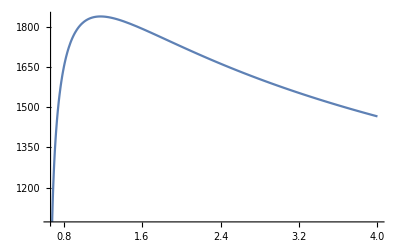

```mathematica
Clear[testdir,testvw,testCoeffs,testTc,testtc,testtab,testTfn,xrangeTest,TT,LmlnhTest1,LmlnhTest2,LmlnhTest3,LmlnhTest4,LmlnhTest5,LmlnhTest6]

Needs["DSReheating`"]

testdir="hot";
testvw=1;

testCoeffs={1,0.825631,1}(*μ, A, λ*);
(*testCoeffs={0.5,0.4,10}(*μ, A, λ*)*)

testTc=500(*[GeV]*);
testtc=((2*10^18)/testTc^2)*1/100(*roughly Hubble time at Tc [GeV^-1]*);

testTfn=TOfx[0.1,10,1/testtc];
Plot[testTfn[t],{t,2/3,4}]
```

```mathematica
{TT,LmlnhTest1}=Timing[LhTest[testdir,testvw,{testTfn,testtc},testCoeffs,testTc,1,False,1,300,False,Automatic,Automatic,6,3]];

Print["time=",TT, " (i=1, Nlx=300, method->Automatic, MaxRecursion->Automatic)"]

{TT,LmlnhTest2}=Timing[LhTest[testdir,testvw,{testTfn,testtc},testCoeffs,testTc,1,False,1,100,False,Automatic,Automatic,6,3]];

Print["time=",TT, " (i=2, Nlx=100, method->Automatic, MaxRecursion->Automatic)"]
```

time=1253.62 (i=1, Nlx=300, method->Automatic, MaxRecursion->Automatic)

time=415.285 (i=2, Nlx=100, method->Automatic, MaxRecursion->Automatic)

```mathematica
{TT,LmlnhTest3}=Timing[LhTest[testdir,testvw,{testTfn,testtc},testCoeffs,testTc,1,False,1,300,True,Automatic,Automatic,6,3]];

Print["time=",TT, " (i=3, Nlx=300, sum)"]

{TT,LmlnhTest4}=Timing[LhTest[testdir,testvw,{testTfn,testtc},testCoeffs,testTc,1,False,1,100,True,Automatic,Automatic,6,3]];

Print["time=",TT, " (i=4, Nlx=100, sum)"]
```

{300,299}

300

time=12.5753 (i=3, Nlx=300, sum)

{100,99}

100

time=1.3348 (i=4, Nlx=100, sum)

```mathematica
{TT,LmlnhTest5}=Timing[LhTest[testdir,testvw,{testTfn,testtc},testCoeffs,testTc,1,False,1,300,False,{"TrapezoidalRule", "Points"->10},0,6,3]];

Print["time=",TT, " (i=5, Nlx=300, method->{TrapezoidalRule, Points->10}, MaxRecursion->0)"]

{TT,LmlnhTest6}=Timing[LhTest[testdir,testvw,{testTfn,testtc},testCoeffs,testTc,1,False,1,100,False,{"TrapezoidalRule", "Points"->10},0,6,3]];

Print["time=",TT, " (i=6, Nlx=100, method->{TrapezoidalRule, Points->10}, MaxRecursion->0)"]
```

time=1048.75 (i=5, Nlx=300, method->{TrapezoidalRule, Points->10}, MaxRecursion->0)

time=340.77 (i=6, Nlx=100, method->{TrapezoidalRule, Points->10}, MaxRecursion->0)

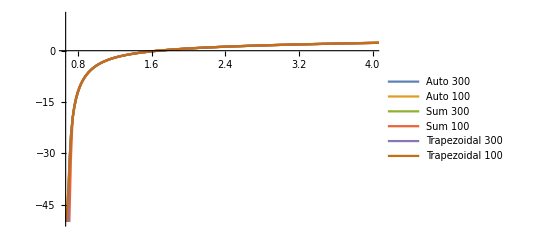

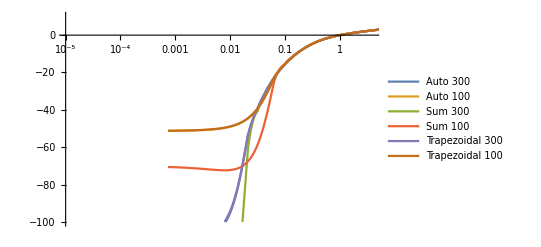

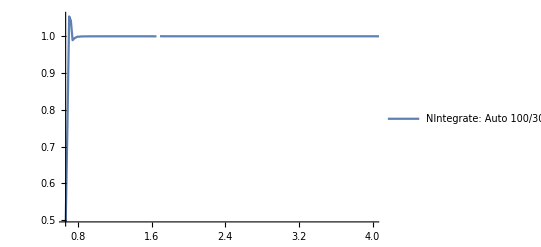

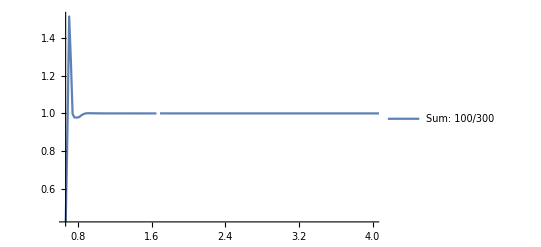

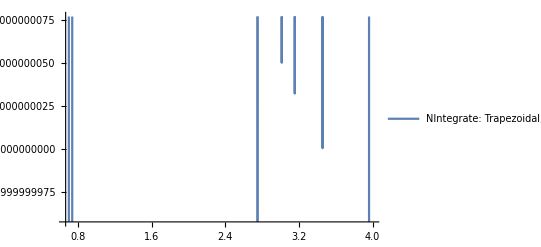

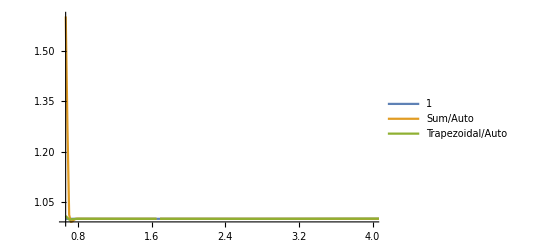

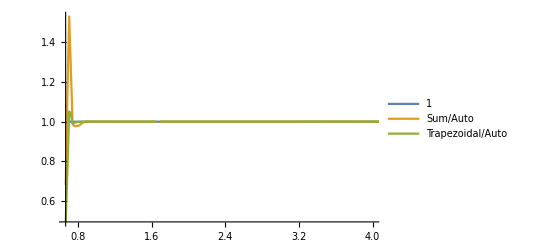

```mathematica
xrangeTest=10^(InterpolatingFunctionDomain[LmlnhTest1]//Flatten);

Plot[{LmlnhTest1[Log10[x]],LmlnhTest2[Log10[x]],LmlnhTest3[Log10[x]],LmlnhTest4[Log10[x]],LmlnhTest5[Log10[x]],LmlnhTest6[Log10[x]]},{x,xrangeTest⟦1⟧,xrangeTest⟦2⟧},PlotRange->{{2/3,4},{-50,10}},PlotLegends->{"Auto 300","Auto 100","Sum 300","Sum 100","Trapezoidal 300","Trapezoidal 100"}]

LogLinearPlot[{LmlnhTest1[Log10[2/3+dx]],LmlnhTest2[Log10[2/3+dx]],LmlnhTest3[Log10[2/3+dx]],LmlnhTest4[Log10[2/3+dx]],LmlnhTest5[Log10[2/3+dx]],LmlnhTest6[Log10[2/3+dx]]},{dx,xrangeTest⟦1⟧-2/3,xrangeTest⟦2⟧-2/3},PlotRange->{{10^-5,4},{-100,10}},PlotLegends->{"Auto 300","Auto 100","Sum 300","Sum 100","Trapezoidal 300","Trapezoidal 100"}]

Plot[{LmlnhTest2[Log10[x]]/LmlnhTest1[Log10[x]]},{x,xrangeTest⟦1⟧,xrangeTest⟦2⟧},PlotRange->{{2/3,4},Full},PlotLegends->{"NIntegrate: Auto 100/300"}]

Plot[{LmlnhTest4[Log10[x]]/LmlnhTest3[Log10[x]]},{x,xrangeTest⟦1⟧,xrangeTest⟦2⟧},PlotRange->{{2/3,4},Full},PlotLegends->{"Sum: 100/300"}]

Plot[{LmlnhTest6[Log10[x]]/LmlnhTest5[Log10[x]]},{x,xrangeTest⟦1⟧,xrangeTest⟦2⟧},PlotRange->{{2/3,4},Automatic},PlotLegends->{"NIntegrate: Trapezoidal, 10 pts: 100/300"}]


Plot[{LmlnhTest1[Log10[x]]/LmlnhTest1[Log10[x]],LmlnhTest3[Log10[x]]/LmlnhTest1[Log10[x]],LmlnhTest5[Log10[x]]/LmlnhTest1[Log10[x]]},{x,xrangeTest⟦1⟧,xrangeTest⟦2⟧},PlotRange->{{2/3,4},Full},PlotLegends->{"1","Sum/Auto","Trapezoidal/Auto"}]

Plot[{LmlnhTest1[Log10[x]]/LmlnhTest1[Log10[x]],LmlnhTest4[Log10[x]]/LmlnhTest1[Log10[x]],LmlnhTest6[Log10[x]]/LmlnhTest1[Log10[x]]},{x,xrangeTest⟦1⟧,xrangeTest⟦2⟧},PlotRange->{{2/3,4},Full},PlotLegends->{"1","Sum/Auto","Trapezoidal/Auto"}]

Clear[testdir,testvw,testCoeffs,testTc,testtc,testtab,testTfn,xrangeTest,TT]
```

#### Test

-Graphics-

time=33.4608 (sum, Nlx=500)

time=7.86518 (sum, Nlx=250)

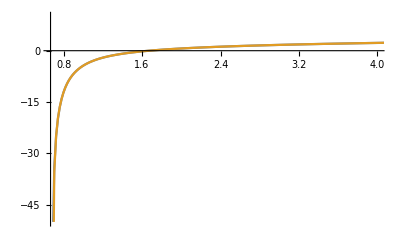

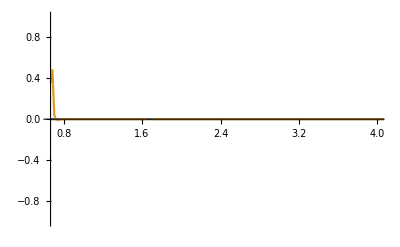

```mathematica
Needs["DSReheating`"]

testdir="hot";
testvw=1;

testCoeffs={1,0.825631,1}(*μ, A, λ*);
(*testCoeffs={0.5,0.4,10}(*μ, A, λ*)*)

testTc=500(*[GeV]*);
testtc=((2*10^18)/testTc^2)*1/100(*roughly Hubble time at Tc [GeV^-1]*);

testTfn=TOfx[0.1,10,1/testtc];
Plot[testTfn[t],{t,2/3,4}]

{TT,LmlnhTest1}=Timing[Lmlnh[testdir,testvw,{testTfn,testtc},testCoeffs,testTc,1,False,1,500]];
Print["time=",TT, " (sum, Nlx=500)"]

{TT,LmlnhTest2}=Timing[Lmlnh[testdir,testvw,{testTfn,testtc},testCoeffs,testTc,1,False,1,250]];
Print["time=",TT, " (sum, Nlx=250)"]

xrangeTest=10^(InterpolatingFunctionDomain[LmlnhTest1]//Flatten);

Plot[{LmlnhTest1[Log10[x]],LmlnhTest2[Log10[x]]},{x,xrangeTest⟦1⟧,xrangeTest⟦2⟧},PlotRange->{{2/3,4},{-50,10}}]

Plot[{LmlnhTest1[Log10[x]]/LmlnhTest1[Log10[x]]-1,LmlnhTest2[Log10[x]]/LmlnhTest1[Log10[x]]-1},{x,xrangeTest⟦1⟧,xrangeTest⟦2⟧},PlotRange->{{2/3,4},{-1,1}}]

Clear[testdir,testvw,testCoeffs,testTc,testtc,testTfn,xrangeTest,LmlnhTest1,LmlnhTest2,TT]
```

### Bubble number density n_b(t)

The bubble number density as a function of time:

n_b(t)=∫_t_c^t ⅆt' Γ_nucl/𝒱(t')·h(t').

We also allow for the inclusion of the scale factor function a(t):

n_b(t)=(a(t))^-3∫_t_c^t ⅆt' Γ_nucl/𝒱(t')·(a(t'))^3·h(t').

For simplicity, we will compute & interpolate the log_10 of n_b as a function of the log_10 of time instead:

log_10[n_b(log_10(t))]

Note that from here we can define R_*≡(n_b(t→∞))^(-1/3), the mean bubble separation.

```mathematica
Clear[Lnbubble]

Lnbubble[LmlnhLx_,TempEvol_List,coeffs_List,Tcrit_,Kfactor_:1,full_:False,scaleFactor_:1]:=Lnbubble[LmlnhLx,TempEvol,coeffs,Tcrit,Kfactor,full,scaleFactor]=Block[{Tc=Tcrit,Tofx,tScale,scale,Lnscale,LnGammaPT,GammaPT,LxA,LxB,LxData,hofx,aofx,integrand,lxTable,lxMids,table,resTable,non0Tab,reg,data,res,eps=10^-6,Δlx},

(*NOTE: CRUCIAL FOR NUMERICAL METHOD: we assume T(t) is a concave function, and that therefore it has a maximum in its domain. True during reheating.*)

(*checking consistency of 'TempEvol' arguments.*)
If[(Length@TempEvol)!=2,Message[Lnbubble::TempEvolError];Abort[]];

(*T(x), t/x*)
{Tofx,tScale}=TempEvol;

(*scale factor*)
aofx[xx_]:=If[scaleFactor===1,1,scaleFactor[xx]];

(*overall scale of the result*)
scale=Tc^4*tScale;
(*LnS ≡ ln(scale)*)
Lnscale=Log[scale];

(*LnΓ ≡ ln(Subscript[Γ, nucl](Subscript[T, PT])/Subscript[T, c]^4)*)
LnGammaPT[xx_]:=Γnucl[coeffs,1,Tofx[xx]/Tc,Kfactor,full,True]*Log[10];

(*dimensionless (comoving) nucleation rate: a^4·Subscript[Γ, nucl](Subscript[T, PT])*tScale= a^4·(Subscript[Γ, nucl](Subscript[T, PT])/Subscript[T, c]^4)*scale = exp[LnΓ+LnS] (a dimensionless quantity), regularized if it's too small. The reason for combining the nucleation rate and the overall scale of the integral is to make the exponent bigger*)
GammaPT[xx_]:=If[(LnGammaPT[xx]+Lnscale)>-500,aofx[xx]^4*Exp[LnGammaPT[xx]+Lnscale],0];

(*anatomy of the interpolating function of the fractional metastable volume. NOTE: must have been computed using the same parameters!*)
{LxA,LxB}=InterpolatingFunctionDomain[LmlnhLx]//Flatten;
LxData=InterpolatingFunctionCoordinates[LmlnhLx]//Flatten;

(*fractional volume h(x) in the metastable phase, obtained from LmlnhLx≡Subscript[log, 10](-ln h(Subscript[log, 10](x)))*)
hofx[xx_]:=If[(-10^LmlnhLx[Log10[xx]])>-500,Exp[-10^LmlnhLx[Log10[xx]]],0];

(*integrand, in ln-space*)
integrand[x_,xp_]:=aofx[x]^-3*xp/aofx[xp]*(GammaPT[xp]*hofx[xp])*(HeavisideTheta[x-xp]*Sign[x-xp]);

(*differentials in ln(x), for the numerical integral*)
Δlx=(LxData⟦2⟧-LxData⟦1⟧)*Log[10];

(*table of ln(x) values*)
lxTable=(LxData*Log[10]);

(*table of ln(x) mid-points*)
lxMids=(lxTable⟦1;;-2⟧+lxTable⟦2;;-1⟧)/2;

(*table to integrate*)
table=Outer[integrand,Exp[lxTable],Exp[lxMids]];

(*integrating along xp: a simple sum of columns, for each row!*)
resTable=Δlx*Total[table,{2}];
Clear[table];

(*selecting those that are not 0, to regularize*)
non0Tab=Select[resTable,#!=0&];
If[(Length@non0Tab)==0,Message[Lnbubble::NoNucleation];Abort[]];

(*regularizing*)
reg=Min[non0Tab]*eps*eps;
resTable=If[#==0,reg,#]&/@resTable;

(*data to interpolate, in Subscript[log, 10] (which is ln/ln(10))*)
data=Transpose[{lxTable/Log[10],Log10[resTable]}];
Clear[resTable];

(*interpolating the data*)
res=Interpolation[data];

res
]

Lnbubble::TempEvolError="'TempEvol' should be {Tofx, tScale}: a list with only two elements: the temperature as a function of a time-like parameter x, T(x), and the time-scale given by the ratio t/x.";
Lnbubble::NoNucleation="The nucleation rate is so small at all times that there are effectively no bubbles being produced.";
```

#### Test

-Graphics-

{0.667406,61.4788}

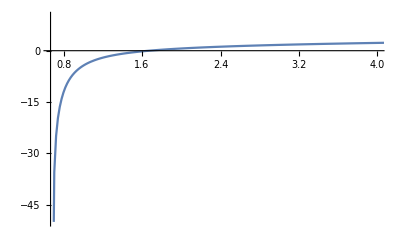

time=7.8898

3.8679×10^-33

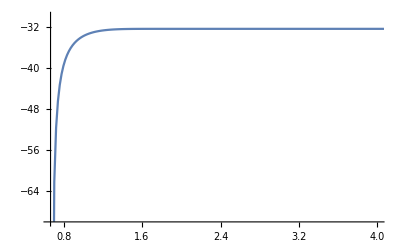

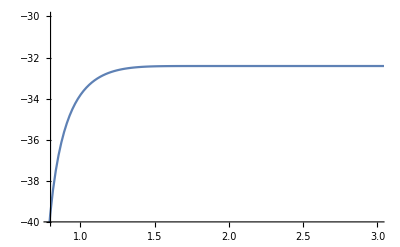

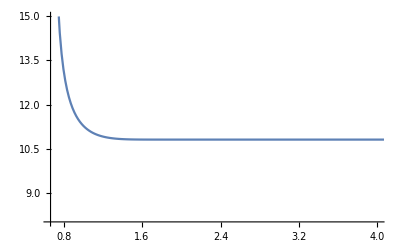

```mathematica
Needs["DSReheating`"]

testdir="hot";
testvw=1;

testCoeffs={1,0.825631,1}(*μ, A, λ*);

testTc=500(*[GeV]*);
testtc=((2*10^18)/testTc^2)*1/100(*roughly Hubble time at Tc [GeV^-1]*);

testTfn=TOfx[0.1,10,1/testtc];
Plot[testTfn[t],{t,2/3,4}]

LmlnhTest=Lmlnh[testdir,testvw,{testTfn,testtc},testCoeffs,testTc,1,False,1,250];
xrangeTest=10^(InterpolatingFunctionDomain[LmlnhTest]//Flatten)

Plot[LmlnhTest[Log10[x]],{x,xrangeTest⟦1⟧,xrangeTest⟦2⟧},PlotRange->{{2/3,4},{-50,10}}]

{TT,LnbTest}=Timing[Lnbubble[LmlnhTest,{testTfn,testtc},testCoeffs,testTc,1,False,1]];

Print["time=",TT]
10^(LnbTest[Log10[xrangeTest⟦2⟧]])

Plot[LnbTest[Log10[x]],{x,xrangeTest⟦1⟧,xrangeTest⟦2⟧},PlotRange->{{2/3,4},{-70,-30}}]

Plot[LnbTest[Log10[x]],{x,xrangeTest⟦1⟧,xrangeTest⟦2⟧},PlotRange->{{0.8,3},{-40,-30}}]

Plot[-1/3 LnbTest[Log10[x]],{x,xrangeTest⟦1⟧,xrangeTest⟦2⟧},PlotRange->{{2/3,4},{8,15}}]

Clear[testdir,testvw,testCoeffs,testTc,testtc,testtab,testTfn,xrangeTest,LmlnhTest,LnbTest,TT]
```

### Mean bubble radius ⟨R_b(t)⟩

The mean bubble radius:

⟨R_b(t)⟩=(∫_t_c^t ⅆt' Γ_nucl/𝒱(t')·h(t')·v_w(t-t'))/(∫_t_c^t ⅆt' Γ_nucl/𝒱(t')·h(t')).

We also allow for the inclusion of the scale factor function a(t):

⟨R_b(t)⟩=(a(t)∫_t_c^t ⅆt' Γ_nucl/𝒱(t')·(a(t'))^3·h(t')·(v_w∫_t'^t dt''/(a(t''))))/(∫_t_c^t ⅆt' Γ_nucl/𝒱(t')·(a(t'))^3·h(t')).

For simplicity, we will compute & interpolate the log_10 of ⟨R_b⟩ as a function of the log_10 of time instead:

log_10[⟨R_b(log_10(t))⟩]

NOTE: this is the average bubble radius, not the average separation between bubbles. The latter is simply given by R_*≡n_b^(-1/3). In particular, the way it’s defined, ⟨R_b(t)⟩ still grows with time, because the bubbles produced at some time t' when h(t') was not negligible are still growing! I.e. this does not account for collisions, and the fact that the bubbles will stop expanding.

```mathematica
Clear[LRbubble]

LRbubble[LmlnhLx_,LnbLx_,vw_,TempEvol_List,coeffs_List,Tcrit_,Kfactor_:1,full_:False,scaleFactor_:1]:=LRbubble[LmlnhLx,LnbLx,vw,TempEvol,coeffs,Tcrit,Kfactor,full,scaleFactor]=Block[{Tc=Tcrit,Tofx,tScale,scale,Lnscale,LnGammaPT,GammaPT,LxA,LxB,LxData,LnbData,hofx,aofx,radius,integrand,lxTable,lxMids,table,resTable,non0Tab,reg,Lnorm,data,res,eps=10^-6,Δlx},

(*NOTE: CRUCIAL FOR NUMERICAL METHOD: we assume T(t) is a concave function, and that therefore it has a maximum in its domain. True during reheating.*)

(*checking consistency of 'TempEvol' arguments.*)
If[(Length@TempEvol)!=2,Message[LRbubble::TempEvolError];Abort[]];

(*T(x), t/x*)
{Tofx,tScale}=TempEvol;

(*scale factor*)
aofx[xx_]:=If[scaleFactor===1,1,scaleFactor[xx]];

(*overall scale of the result*)
scale=Tc^4*tScale^2;
(*LnS ≡ ln(scale)*)
Lnscale=Log[scale];

(*LnΓ ≡ ln(Subscript[Γ, nucl](Subscript[T, PT])/Subscript[T, c]^4)*)
LnGammaPT[xx_]:=Γnucl[coeffs,1,Tofx[xx]/Tc,Kfactor,full,True]*Log[10];

(*dimensionless (comoving) nucleation rate: a^4·Subscript[Γ, nucl](Subscript[T, PT])*tScale^2= a^4·(Subscript[Γ, nucl](Subscript[T, PT])/Subscript[T, c]^4)*scale = exp[LnΓ+LnS] (a dimensionless quantity), regularized if it's too small. The reason for combining the nucleation rate and the overall scale of the integral is to make the exponent bigger*)
GammaPT[xx_]:=If[(LnGammaPT[xx]+Lnscale)>-500,aofx[xx]^4*Exp[LnGammaPT[xx]+Lnscale],0];

(*anatomy of the interpolating function of fractional metastable volume. NOTE: must have been computed using the same parameters!*)
{LxA,LxB}=InterpolatingFunctionDomain[LmlnhLx]//Flatten;
LxData=InterpolatingFunctionCoordinates[LmlnhLx]//Flatten;

(*extracting data from bubble number density. NOTE: must have been computed using the same parameters!*)
LnbData=InterpolatingFunctionValuesOnGrid[LnbLx]//Flatten;

(*fractional volume h(x) in the metastable phase, obtained from LmlnhLx≡Subscript[log, 10](-ln h(Subscript[log, 10](x)))*)
hofx[xx_]:=If[(-10^LmlnhLx[Log10[xx]])>-500,Exp[-10^LmlnhLx[Log10[xx]]],0];

(*dimensionless (comoving) bubble radius: w/ or w/o scale factor*)
radius[x_,xp_]:=If[scaleFactor===1,vw*(x-xp)*HeavisideTheta[x-xp],If[xp≥x,0,vw*NIntegrate[xx/aofx[xx],{xx,xp,x}(*,WorkingPrecision->6,PrecisionGoal->3,Method->{"TrapezoidalRule","Points"->5},MaxRecursion->0*)]]];

(*integrand, in ln-space*)
integrand[x_,xp_]:=aofx[x]*xp/aofx[xp]*(GammaPT[xp]*hofx[xp]*radius[x,xp]);

(*differentials in ln(x), for the numerical integral*)
Δlx=(LxData⟦2⟧-LxData⟦1⟧)*Log[10];

(*table of ln(x) values*)
lxTable=(LxData*Log[10]);

(*table of ln(x) mid-points*)
lxMids=(lxTable⟦1;;-2⟧+lxTable⟦2;;-1⟧)/2;

(*table to integrate*)
table=Outer[integrand,Exp[lxTable],Exp[lxMids]];

(*integrating along xp: a simple sum of columns, for each row!*)
resTable=Δlx*Total[table,{2}];
Clear[table];

(*selecting those that are not 0, to regularize*)
non0Tab=Select[resTable,#!=0&];
If[(Length@non0Tab)==0,Message[LRbubble::NoNucleation];Abort[]];

(*regularizing*)
reg=Min[non0Tab]*eps*eps;
resTable=If[#==0,reg,#]&/@resTable;

(*normalization factor Subscript[n, b] a^3 (present due to dimensionality of the probability distribution) in Subscript[log, 10]: Subscript[log, 10](Subscript[n, b] a^3)=Subscript[log, 10] Subscript[n, b] + 3 Subscript[log, 10] a*)
Lnorm=LnbData+3Log10[aofx[Exp[lxTable]]];

(*data to interpolate, in Subscript[log, 10] (which is ln/ln(10))*)
data=Transpose[{lxTable/Log[10],Log10[resTable]-Lnorm}];
Clear[resTable,LnbData,Lnorm];

(*interpolating the data*)
res=Interpolation[data];

res
]

LRbubble::TempEvolError="'TempEvol' should be {Tofx, tScale}: a list with only two elements: the temperature as a function of a time-like parameter x, T(x), and the time-scale given by the ratio t/x.";
LRbubble::NoNucleation="The nucleation rate is so small at all times that there are effectively no bubbles being produced.";
```

#### Test

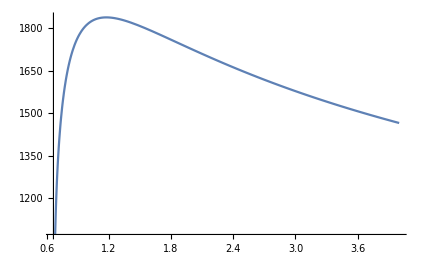

{0.667406,61.4788}

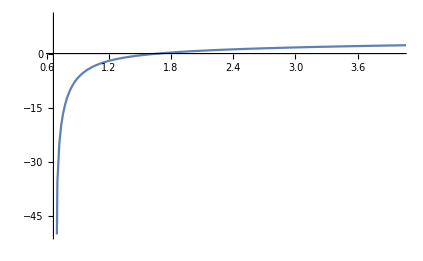

time=8.19228

4.8209×10^12

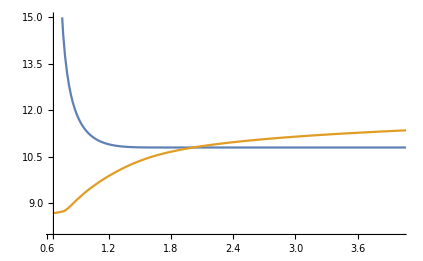

```mathematica
Clear[tabTest,ToftTest,mlnhTest]

testdir="hot";
testvw=1;

testCoeffs={1,0.825631,1}(*μ, A, λ*);

testTc=500(*[GeV]*);
testtc=((2*10^18)/testTc^2)*1/100(*roughly Hubble time at Tc [GeV^-1]*);

testTfn=TOfx[0.1,10,1/testtc];
Plot[testTfn[t],{t,2/3,4}]

LmlnhTest=Lmlnh[testdir,testvw,{testTfn,testtc},testCoeffs,testTc,1,False,1,250];
xrangeTest=10^(InterpolatingFunctionDomain[LmlnhTest]//Flatten)

Plot[LmlnhTest[Log10[x]],{x,xrangeTest⟦1⟧,xrangeTest⟦2⟧},PlotRange->{{2/3,4},{-50,10}}]

LnbTest=Lnbubble[LmlnhTest,{testTfn,testtc},testCoeffs,testTc,1,False,1];
{TT,LRbTest}=Timing[LRbubble[LmlnhTest,LnbTest,testvw,{testTfn,testtc},testCoeffs,testTc,1,False,1]];

Print["time=",TT]

10^(LRbTest[Log10[xrangeTest⟦2⟧]])

Plot[{-1/3 LnbTest[Log10[x]],LRbTest[Log10[x]]},{x,xrangeTest⟦1⟧,xrangeTest⟦2⟧},PlotRange->{{2/3,4},{8,15}}]

Clear[testdir,testvw,testCoeffs,testTc,testtc,testtab,testTfn,xrangeTest,LmlnhTest,LnbTest,LRbTest,TT]
```

### Temperature of the Phase Transition T_PT

This is obtained by demanding that there is roughly 1 bubble in a bubble-size volume (a sphere of radius v_w/β) in a time 1/β, i.e. -ln h(t) = 1.

Using the saddle point approximation we can analytically compute -ln h(t) as:
(8π v_w^3 Γ_nucl(T_PT)/𝒱)/(β^4(T_PT))=1.

However, since this is quickly varying (due to the e^-S_E in Γ_nucl/𝒱), it is more convenient to use the condition log_10(-ln h(t)) = 0 instead.

```mathematica
Clear[condPT,LogCondPT,NoDLogCondPT]

(*condition for PT: must be equal to 1*)
condPT[vw_,GammaNucl_,betaRate_]:=(8π vw^3 GammaNucl)/betaRate^4

(*Subscript[log, 10] version of the above condition, useful for numerical solutions in order to avoid Exp[-LARGE NUMBER] in Subscript[Γ, nucl]/𝒱*)
LogCondPT[vw_,LogGammaNucl_,betaRate_]:=Log10[8π]+3Log10[vw]+LogGammaNucl-4Log10[Abs[betaRate]]

(*same as above, except the dimensions of Subscript[Γ, nucl]/𝒱 and β have been factored out. Here LogGammList={Subscript[log, 10](Subscript[Γ, nucl]/𝒱/Subscript[d, 1]^4), Subscript[d, 1] } and betaList={β/Subscript[d, 2], Subscript[d, 2]}, with Subscript[d, 1] and Subscript[d, 2] the typical dimensions of Subscript[Γ, nucl]/𝒱 and β respectively *)
NoDLogCondPT[vw_,LogGammList_List,betaList_List]:=Log10[8π]+3Log10[vw]+LogGammList⟦1⟧-4Log10[Abs[betaList⟦1⟧]]+4Log10[LogGammList⟦2⟧/betaList⟦2⟧]
```

```mathematica
ClearAll[tTPT]

tTPT[direction_,vw_,TempEvol_List,coeffs_List,Tcrit_,method_:"analytic",Kfactor_:1,full_:False,scaleFactor_:1,Nlx_:250]:=tTPT[direction,vw,TempEvol,coeffs,Tcrit,method,Kfactor,full,scaleFactor,Nlx]=Block[{gamma,t0,tcrit,Tofx,tScale,dlnTdt,xmax,Tmax,xA,xB,xData,yData,prec,μ,A,λ,Tc=Tcrit,Tlo,Thi,TmaxFlag,PTCritFlag,Toffset,Tini,TLeft,TRight,x0,xlo,xhi,xRange,xLeft,xRight,GammaPT,LogGammaPT,betaPT,cond,LogCond,noDLogCond,LhLx,LnbLx,LRLx,data,xpt,tpt,Tpt,result,eps=10^-6},
(*NOTE: CRUCIAL FOR NUMERICAL METHOD: we assume T(t) is a concave function, and that therefore it has a maximum in its domain. True during reheating.*)

(*distributing the coefficients*)
{μ,A,λ}=coeffs;

(*checking whether there can be a first order phase transition*)
noCritTemp[coeffs];

(*lowest/highest temperatures probed by our pre-computed critical bubbles*)
Tlo=TLow;
Thi=THigh;

(*the phase transition is either cold (subcritical) or hot (supercritical):*)
noOption[direction,{"cold","hot"}];

(*the 'method' argument is either analytic, semi-analytic, numeric, or alternative*)
noOption[method,{"analytic","semi","numeric","alt"}];

(*checking consistency between 'method' and 'TempEvol' arguments.*)
If[(method=="analytic")&&(Length@TempEvol)!=3,Message[tTPT::AnalyticTempEvolError];Abort[]];
If[((method=="semi")||(method=="numeric")||(method=="alt"))&&(Length@TempEvol)!=2,Message[tTPT::NumericTempEvolError];Abort[]];

(*temperature offset from Subscript[T, c] depending on direction*)
Toffset=Tc*(1+eps*If[direction=="cold",-1,+1]);

(*routine for analytic method*)
If[method=="analytic",

(*{γ, Subscript[t, 0], Subscript[t, c]}*)
{gamma,t0,tcrit}=TempEvol;

(*correcting Thi in case this corresponds to a non-existent temperature (because the spinodal temperature never disappears!)*)
Thi=If[(Im[Thi]!=0)||(Thi===ComplexInfinity),Tc*10,Thi];

(*the initial guess for the PT temperature is either below Subscript[T, c] for cold (subcritical) PT, or above Subscript[T, c] for hot (supercritical) PT.*)
Tini=If[direction=="cold",GeometricMean[{Tlo,Tc}],GeometricMean[{Thi,Tc}]];

(*the lower and upper edges of the numerical solver*)
TLeft=If[direction=="cold",Tlo,Toffset];
TRight=If[direction=="cold",Toffset,Thi];

(*Subscript[Γ, nucl](Subscript[T, PT])*)
LogGammaPT[TT_]:=Γnucl[coeffs,Tc,TT,Kfactor,full,True];

(*β(Subscript[T, PT])*)
betaPT[TT_]:=beta1OfTempAn[gamma,t0,tcrit,coeffs,Tc,TT,Kfactor,full];

(*log-condition for PT: must be equal to 0*)
LogCond[TT_?NumericQ]:=LogCondPT[vw,LogGammaPT[TT],betaPT[TT]];

(*checking whether the PT finished immediately after Tc*)
PTCritFlag = (LogCond[Toffset]>0);
If[(PTCritFlag == True),Message[tTPT::AnalyticCritPT,direction,Tc,Toffset,LogCond[Toffset]]];

(*checking whether the PT can complete at all*)
If[(PTCritFlag == False) && (LogCond[TLeft]*LogCond[TRight]>0),Message[tTPT::AnalyticUnfinishedPT,direction,TLeft,LogCond[TLeft],TRight,LogCond[TRight]];Abort[]];

(*solving for Subscript[T, PT] (using the pre-calculated log of the PT condition)*)
Tpt=If[(PTCritFlag == True),Toffset,
10^(LT/.FindRoot[LogCond[10^LT],{LT,Log10[Tini],Log10[TLeft],Log10[TRight]},MaxIterations->10^6,AccuracyGoal->6,PrecisionGoal->4]//Quiet)];

(*Subscript[t, PT]*)
tpt=tOfTempAn[Tc,tcrit,gamma,t0,Tpt];

If[IntervalMemberQ[Interval[{Tlo,Thi}],Tpt]==False,Message[tTPT::NoTpt, Tpt,{Tlo,Thi}];Abort[],result={tpt,Tpt}];
];

(*routine for semi-analytic method*)
If[method=="semi",
(*NOTE: the crucial object for the 'numeric' method is T(t), the temperature as a function of time. However, the only purpose of the time t here is to serve as a parameter or variable with which the temperature evolves. It does *not* matter what its absolute scale or dimensions are. This is useful, since in our reheating code we will use x=t*Subscript[H, d] as our variable. In other words, tScale = 1/Subscript[H, d].*)

(*T(x), t/x*)
{Tofx,tScale}=TempEvol;

(*dlnTdt(t)*)
dlnTdt[x_]=1/tScale D[Log[Tofx[x]],x];

(*anatomy of the interpolating function*)
{xA,xB}=(InterpolatingFunctionDomain[Tofx]//Flatten);
xData=(InterpolatingFunctionCoordinates[Tofx]//Flatten);
prec=Round[Precision[xData⟦1⟧]];

(*slightly away from the leftmost edge*)
xA=If[xA<=0,eps,Min[xData⟦2⟧,xA*(1+eps)]];
Clear[xData];

(*checking whether Subscript[T, c] is in the interval of temperatures probed by the T(t) function along the stated direction*)
noTempFn[Tofx,Tc,1];

(*time t at which T(t) reaches a maximum*)
{xmax,Tmax}=tTMax[Tofx,1];

(*correcting Thi in case this corresponds to a non-existent temperature (because the spinodal temperature never disappears!)*)
Thi=If[(Im[Thi]!=0)||(Thi===ComplexInfinity),Tmax*2,Thi];

(*redefining Tlo and Thi based on what the interpolating function can accommodate*)
Tlo=If[direction=="cold",Max[Tofx[xB],Tlo],Max[Tofx[xA],Tlo,Toffset]];
Thi=If[direction=="cold",Min[Thi,Tmax,Toffset],Min[Thi,Tmax]];

(*finding the time range over which we will look for the PT time, for each direction*)
xlo=tOfTempNum[Tofx,Tlo,1];
xhi=tOfTempNum[Tofx,Thi,1];

(*the initial guess for the PT temperature is either below Subscript[T, c] for cold (subcritical) PT, or above Subscript[T, c] for hot (supercritical) PT.*)
Tini=If[direction=="cold",GeometricMean[{Tlo,Tc}],GeometricMean[{Thi,Tc}]];

(*the initial guess for the PT time*)
x0=tOfTempNum[Tofx,Tini,1];
x0=If[direction=="cold",x0⟦2⟧,x0⟦1⟧];

xLeft=If[direction=="cold",xhi⟦2⟧,xlo⟦1⟧];
xRight=If[direction=="cold",xlo⟦2⟧,xhi⟦1⟧];

(*Subscript[Γ, nucl](Subscript[T, PT]) in units of Subscript[T, c]^4*)
LogGammaPT[xx_]:=Γnucl[coeffs,1,Tofx[xx]/Tc,Kfactor,full,True];

(*β(Subscript[T, PT]), in units of 1/tScale*)
betaPT[xx_]:=β1Rate[tScale*dlnTdt[xx],coeffs,1,Tofx[xx]/Tc,Kfactor,full];

(*dimensionless log-condition for PT: must be equal to 0*)
noDLogCond[xx_?NumericQ]:=NoDLogCondPT[vw,{LogGammaPT[xx],Tc},{betaPT[xx],1/tScale}];

(*checking whether the PT finished immediately after Subscript[T, c]*)
PTCritFlag = (noDLogCond[xLeft]>0);
If[(PTCritFlag == True),Message[tTPT::SemiCritPT,direction,Tc,xLeft,xLeft*tScale,Tofx[xLeft],noDLogCond[xLeft]]];

(*checking whether the PT completes at all*)
If[(PTCritFlag == False) && (noDLogCond[xLeft]*noDLogCond[xRight]>0),Message[tTPT::SemiUnfinishedPT,direction,xLeft,xLeft*tScale,Tofx[xLeft],noDLogCond[xLeft],xRight,xRight*tScale,Tofx[xRight],noDLogCond[xRight]];Abort[]];

(*solving for Subscript[t, PT] (using the pre-calculated log of the PT condition)*)
xpt=If[(PTCritFlag == True),xLeft,10^(Lx/.FindRoot[noDLogCond[10^Lx],{Lx,Log10[x0],Log10[xLeft],Log10[xRight]},MaxIterations->10^6,AccuracyGoal->6,PrecisionGoal->4]//Quiet)];
tpt=xpt*tScale;

(*Subscript[T, PT]*)
Tpt=Tofx[xpt];

If[IntervalMemberQ[Interval[{Tlo,Thi}],Tpt]==False,Message[tTPT::NoTpt, Tpt,{Tlo,Thi}];Abort[],result={tpt,Tpt}];

];

(*routine for numeric full method*)
If[method=="numeric",
(*NOTE: the crucial object for the 'numeric' method is T(t), the temperature as a function of time. However, the only purpose of the time t here is to serve as a parameter or variable with which the temperature evolves. It does *not* matter what its absolute scale or dimensions are. This is useful, since in our reheating code we will use x=t*Subscript[H, d] as our variable. In other words, tScale = 1/Subscript[H, d].*)

(*T(x), t/x*)
{Tofx,tScale}=TempEvol;

(*anatomy of the interpolating function*)
{xA,xB}=(InterpolatingFunctionDomain[Tofx]//Flatten);
xData=(InterpolatingFunctionCoordinates[Tofx]//Flatten);
prec=Round[Precision[xData⟦1⟧]];

(*slightly away from the edges*)
xA=If[xA<=0,eps,Min[xData⟦2⟧,xA*(1+eps)]];
Clear[xData];

(*time t at which T(t) reaches a maximum*)
{xmax,Tmax}=tTMax[Tofx,1];

(*correcting Thi in case this corresponds to a non-existent temperature (because the spinodal temperature never disappears!)*)
Thi=If[(Im[Thi]!=0)||(Thi===ComplexInfinity),Tmax*2,Thi];

(*whether Tmax is in the interval of temperatures for which we computed the critical bubbles*)
TmaxFlag=IntervalMemberQ[Interval[{Tlo,Thi}],Tmax];

(*computing Subscript[log, 10](-ln h(Subscript[log, 10] x)), the PT condition; and the time range*)
LogCond=Lmlnh[direction,vw,TempEvol,coeffs,Tc,Kfactor,full,scaleFactor,Nlx];

(*the time range, slightly offset from the edges*)
xRange=10^(InterpolatingFunctionDomain[LogCond]//Flatten);
xLeft=xRange⟦1⟧;
xRight=xRange⟦2⟧;

(*checking whether the PT finished immediately after Tc*)
PTCritFlag = (LogCond[Log10[xLeft]]>0);
If[(PTCritFlag == True),Message[tTPT::NumericCritPT,direction,Tc,xLeft,xLeft*tScale,Tofx[xLeft],LogCond[Log10[xLeft]]]];

(*checking whether the PT completes at all*)
If[(PTCritFlag == False) && (direction == "cold") && (LogCond[Log10[xLeft]]*LogCond[Log10[xRight]]>0),Message[tTPT::NumericUnfinishedColdPT,direction,xLeft,xLeft*tScale,Tofx[xLeft],LogCond[Log10[xLeft]],xRight,xRight*tScale,Tofx[xRight],LogCond[Log10[xRight]]];Abort[]];
If[(PTCritFlag == False) && (direction == "hot") &&(TmaxFlag == True) && (LogCond[Log10[xLeft]]*LogCond[Log10[xRight]]>0),Message[tTPT::NumericUnfinishedHotPT1,direction,xLeft,xLeft*tScale,Tofx[xLeft],LogCond[Log10[xLeft]],xRight,xRight*tScale,Tofx[xRight],LogCond[Log10[xRight]]];Abort[]];
If[(PTCritFlag == False) && (direction == "hot") &&(TmaxFlag == False) && (LogCond[Log10[xLeft]]*LogCond[Log10[xRight]]>0),Message[tTPT::NumericUnfinishedHotPT2,direction,xLeft,xLeft*tScale,Tofx[xLeft],LogCond[Log10[xLeft]],xRight,xRight*tScale,Tofx[xRight],LogCond[Log10[xRight]]];Abort[]];

(*the initial guess for the PT time*)
If[(Length@yData != Length@xData),
x0=GeometricMean[xRange],

xData=(InterpolatingFunctionCoordinates[LogCond]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[LogCond]//Flatten);

yData=Abs[yData];
x0=(Position[yData,Min[yData]]//Flatten)⟦1⟧;
x0=10^xData⟦x0⟧;

Clear[xData,yData];
];

(*solving for Subscript[t, PT] (using the pre-calculated log of the PT condition)*)
xpt=If[(PTCritFlag == True),xLeft,10^(Lx/.FindRoot[LogCond[Lx],{Lx,Log10[x0],Log10[xLeft],Log10[xRight]},MaxIterations->10^6,WorkingPrecision->prec,AccuracyGoal->6,PrecisionGoal->4])];
tpt=xpt*tScale;

(*Subscript[T, PT]*)
Tpt=Tofx[xpt];

If[IntervalMemberQ[Interval[{Tlo,Thi}],Tpt]==False,Message[TPT::NoTpt, Tpt,{Tlo,Thi}];Abort[],result={tpt,Tpt}];
];

(*routine for alternative method*)
If[method=="alt",
(*NOTE: the crucial object for the 'numeric' method is T(t), the temperature as a function of time. However, the only purpose of the time t here is to serve as a parameter or variable with which the temperature evolves. It does *not* matter what its absolute scale or dimensions are. This is useful, since in our reheating code we will use x=t*Subscript[H, d] as our variable. In other words, tScale = 1/Subscript[H, d].*)

(*T(x), t/x*)
{Tofx,tScale}=TempEvol;

(*anatomy of the interpolating function*)
{xA,xB}=(InterpolatingFunctionDomain[Tofx]//Flatten);
xData=(InterpolatingFunctionCoordinates[Tofx]//Flatten);
prec=Round[Precision[xData⟦1⟧]];

(*slightly away from the edges*)
xA=If[xA<=0,eps,Min[xData⟦2⟧,xA*(1+eps)]];
Clear[xData];

(*time t at which T(t) reaches a maximum*)
{xmax,Tmax}=tTMax[Tofx,1];

(*correcting Thi in case this corresponds to a non-existent temperature (because the spinodal temperature never disappears!)*)
Thi=If[(Im[Thi]!=0)||(Thi===ComplexInfinity),Tmax*2,Thi];

(*whether Tmax is in the interval of temperatures for which we computed the critical bubbles*)
TmaxFlag=IntervalMemberQ[Interval[{Tlo,Thi}],Tmax];

(*computing Subscript[log, 10](-ln h(Subscript[log, 10] x))*)
LhLx=Lmlnh[direction,vw,TempEvol,coeffs,Tc,Kfactor,full,scaleFactor,Nlx];

(*computing Subscript[log, 10](Subscript[n, b](Subscript[log, 10] x))*)
LnbLx=Lnbubble[LhLx,TempEvol,coeffs,Tc,Kfactor,full,scaleFactor];

(*computing Subscript[log, 10](⟨R(Subscript[log, 10] x)⟩)*)
LRLx=LRbubble[LhLx,LnbLx,vw,TempEvol,coeffs,Tc,Kfactor,full,scaleFactor];

(*computing the PT condition: Subscript[log, 10] Subscript[R, b]-Subscript[log, 10]⟨R⟩, where Subscript[R, b]≡Subscript[n, b]^(-1/3)*)
xData=(InterpolatingFunctionCoordinates[LnbLx]//Flatten);
yData=(-1/3(InterpolatingFunctionValuesOnGrid[LnbLx]//Flatten))-(InterpolatingFunctionValuesOnGrid[LRLx]//Flatten);
data=Transpose[{xData,yData}];

LogCond=Interpolation[data];
Clear[LhLx,LnbLx,LRLx,xData,yData,data];

(*the time range, slightly offset from the edges*)
xRange=10^(InterpolatingFunctionDomain[LogCond]//Flatten);
xLeft=xRange⟦1⟧;
xRight=xRange⟦2⟧;

(*checking whether the PT finished immediately after Tc*)
PTCritFlag = (LogCond[Log10[xLeft]]<0);
If[(PTCritFlag == True),Message[tTPT::AltCritPT,direction,Tc,xLeft,xLeft*tScale,Tofx[xLeft],LogCond[Log10[xLeft]]]];

(*checking whether the PT completes at all*)
If[(PTCritFlag == False) && (direction == "cold") && (LogCond[Log10[xLeft]]*LogCond[Log10[xRight]]>0),Message[tTPT::AltUnfinishedColdPT,direction,xLeft,xLeft*tScale,Tofx[xLeft],LogCond[Log10[xLeft]],xRight,xRight*tScale,Tofx[xRight],LogCond[Log10[xRight]]];Abort[]];
If[(PTCritFlag == False) && (direction == "hot") &&(TmaxFlag == True) && (LogCond[Log10[xLeft]]*LogCond[Log10[xRight]]>0),Message[tTPT::AltUnfinishedHotPT1,direction,xLeft,xLeft*tScale,Tofx[xLeft],LogCond[Log10[xLeft]],xRight,xRight*tScale,Tofx[xRight],LogCond[Log10[xRight]]];Abort[]];
If[(PTCritFlag == False) && (direction == "hot") &&(TmaxFlag == False) && (LogCond[Log10[xLeft]]*LogCond[Log10[xRight]]>0),Message[tTPT::AltUnfinishedHotPT2,direction,xLeft,xLeft*tScale,Tofx[xLeft],LogCond[Log10[xLeft]],xRight,xRight*tScale,Tofx[xRight],LogCond[Log10[xRight]]];Abort[]];

(*the initial guess for the PT time*)
xData=(InterpolatingFunctionCoordinates[LogCond]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[LogCond]//Flatten);

yData=Abs[yData];
x0=(Position[yData,Min[yData]]//Flatten)⟦1⟧;
x0=10^xData⟦x0⟧;

Clear[xData,yData];

(*solving for Subscript[t, PT] (using the pre-calculated log of the PT condition)*)
xpt=If[(PTCritFlag == True),xLeft,10^(Lx/.FindRoot[LogCond[Lx],{Lx,Log10[x0],Log10[xLeft],Log10[xRight]},MaxIterations->10^6,WorkingPrecision->prec,AccuracyGoal->6,PrecisionGoal->4])];
tpt=xpt*tScale;

(*Subscript[T, PT]*)
Tpt=Tofx[xpt];

If[IntervalMemberQ[Interval[{Tlo,Thi}],Tpt]==False,Message[TPT::NoTpt, Tpt,{Tlo,Thi}];Abort[],result={tpt,Tpt}];
];

result
]

tTPT::AnalyticTempEvolError="If you pass 'method'=='analytic', then argument 'TempEvol' should be {gamma, t0, tcrit}: a list with three elements: the power-law behavior of the temperature T as a function of time t, some reference time t_0 at which the temperature vanishes, and the critical time.";
tTPT::NumericTempEvolError="If you pass 'method'=='semi'/'numeric'/'alt', then argument 'TempEvol' should be {Tofx, tScale}: a list with only two elements: the temperature as a function of a time-like parameter x, T(x), and the time-scale given by the ratio t/x.";

tTPT::AnalyticCritPT="The condition for the completion of the `1` Phase Transition was satisfied immediately after the critical temperature Tc=`2`: Toffset=`3`, log_10(cond.)=`4`. This is a very fast PT and quantities such as β should not be trusted. We will nevertheless proceed as if this was when the PT finished.";
tTPT::AnalyticUnfinishedPT="The condition for the completion of the `1` Phase Transition cannot be satisfied: at T=`2` the log_10(cond.)=`3`, while at T=`4` the log_10(cond.)=`5`: the function never crosses 0.";

tTPT::SemiCritPT="The condition for the completion of the `1` Phase Transition was satisfied immediately after the critical temperature Tc=`2`: at xLeft=`3` (tLeft=`4`) with T=`5`, log_10(cond.)=`6`. This is a very fast PT and quantities such as β should not be trusted. We will nevertheless proceed as if this was when the PT finished.";
tTPT::SemiUnfinishedPT="The condition for the completion of the `1` Phase Transition cannot be satisfied: at x=`2` (t=`3`, T=`4`) the log_10(cond.)=`5`, while at x=`6` (t=`7`, T=`8`) the log_10(cond.)=`9`: the function, which is monotonic in x, never crosses 0.";

tTPT::NumericCritPT="The condition for the completion of the `1` Phase Transition was satisfied immediately after the critical temperature Tc=`2`: at xLeft=`3` (tLeft=`4`) with T=`5`, log_10(cond.)=`6`. This is a very fast PT and quantities such as β should not be trusted. We will nevertheless proceed as if this was when the PT finished.";
tTPT::NumericUnfinishedColdPT="The condition for the completion of the `1` Phase Transition cannot be satisfied: at x=`2` (t=`3`, T=`4`) the log_10(cond.)=`5`, while at x=`6` (t=`7`, T=`8`) the log_10(cond.)=`9`: the function, which is monotonic in x, never crosses 0.";
tTPT::NumericUnfinishedHotPT1="The condition for the completion of the `1` Phase Transition cannot be satisfied between the two times at which the critical temperature is reached: at x=`2` (t=`3`, T=`4`) the log_10(cond.)=`5`, while at x=`6` (t=`7`, T=`8`) the log_10(cond.)=`9`: the function, which is monotonic in x, never crosses 0. In other words, the PT does not finish by the time the temperature drops below its critical value again.";
tTPT::NumericUnfinishedHotPT2="The condition for the completion of the `1` Phase Transition cannot be satisfied between the times at which the critical and the spinodal temperatures are reached: at x=`2` (t=`3`, T=`4`) the log_10(cond.)=`5`, while at x=`6` (t=`7`, T=`8`) the log_10(cond.)=`9`: the function, which is monotonic in x, never crosses 0. In other words, the PT does not finish by the time the spinodal temperature is reached, and the broken minimum disappears, leading to a rolling transition.";

tTPT::AltCritPT="The condition for the completion of the `1` Phase Transition was satisfied immediately after the critical temperature Tc=`2`: at xLeft=`3` (tLeft=`4`) with T=`5`, log_10(cond.)=`6`. This is a very fast PT and quantities such as β should not be trusted. We will nevertheless proceed as if this was when the PT finished.";
tTPT::AltUnfinishedColdPT="The condition for the completion of the `1` Phase Transition cannot be satisfied: at x=`2` (t=`3`, T=`4`) the log_10(cond.)=`5`, while at x=`6` (t=`7`, T=`8`) the log_10(cond.)=`9`: the function, which is monotonic in x, never crosses 0.";
tTPT::AltUnfinishedHotPT1="The condition for the completion of the `1` Phase Transition cannot be satisfied between the two times at which the critical temperature is reached: at x=`2` (t=`3`, T=`4`) the log_10(cond.)=`5`, while at x=`6` (t=`7`, T=`8`) the log_10(cond.)=`9`: the function, which is monotonic in x, never crosses 0. In other words, the PT does not finish by the time the temperature drops below its critical value again.";
tTPT::AltUnfinishedHotPT2="The condition for the completion of the `1` Phase Transition cannot be satisfied between the times at which the critical and the spinodal temperatures are reached: at x=`2` (t=`3`, T=`4`) the log_10(cond.)=`5`, while at x=`6` (t=`7`, T=`8`) the log_10(cond.)=`9`: the function, which is monotonic in x, never crosses 0. In other words, the PT does not finish by the time the spinodal temperature is reached, and the broken minimum disappears, leading to a rolling transition.";

tTPT::NoTpt="Tpt=`1` is outside the interval `2`. In other words, the PT could not finish before the radiation cooled-down/heated-up beyond this interval.";
```

#### Tests & Examples

```mathematica
testdir="hot";
testvw=1;
testgamma=1/4;

testCoeffs={0.5,0.4,10}(*μ, A, λ*);

testTc=10(*[TeV]*);
testtc=((2*10^(18-3))/testTc^2)(*roughly Hubble time at Tc*);
testt0=testtc/100.;

tTPT[testdir,testvw,{testgamma,testt0,testtc},testCoeffs,testTc,"analytic",1,False]

%⟦2⟧/testTc

beta1OfTempAn[testgamma,testt0,testtc,testCoeffs,testTc,%%⟦2⟧,1,False]

Clear[testdir,testvw,testgamma,testCoeffs,testTc,testtc,testt0]
```

{2.00828×10^13,10.0104}

1.00104

2.4346×10^-9

```mathematica
testdir="cold";
testvw=0.4;
testgamma=-1/2;

testCoeffs={0.3,0.1,0.5}(*μ, A, λ*);

testTc=10(*[TeV]*);
testtc=((2*10^(18-3))/testTc^2)(*roughly Hubble time at Tc*);

testt0=testtc/100.;

tTPT[testdir,testvw,{testgamma,testt0,testtc},testCoeffs,testTc]

%⟦2⟧/testTc

beta1OfTempAn[testgamma,testt0,testtc,testCoeffs,testTc,%%⟦2⟧]

Clear[testdir,testvw,testgamma,testCoeffs,testTc,testtc,testt0]
```

{2.12834×10^13,9.69086}

0.969086

1.24859×10^-10

```mathematica
testdir="hot";
testvw=1;

testCoeffs={1,0.825631,1}(*μ, A, λ*);
(*testCoeffs={0.5,0.4,10}(*μ, A, λ*)*)

testTc=500(*[GeV]*);
testtc=((2*10^18)/testTc^2)*1/100(*roughly Hubble time at Tc [GeV^-1]*);

testTfn=TOfx[0.1,10,1/testtc];
Plot[testTfn[t],{t,2/3,4}]
LmlnhTest=Lmlnh[testdir,testvw,{testTfn,testtc},testCoeffs,testTc,1,False,1,250];
xrangeTest=10^(InterpolatingFunctionDomain[LmlnhTest]//Flatten)

Plot[LmlnhTest[Log10[x]],{x,xrangeTest⟦1⟧,xrangeTest⟦2⟧},PlotRange->{{2/3,4},{-50,10}}]

tTPT[testdir,testvw,{testTfn,testtc},testCoeffs,testTc,"numeric",1,False,1,250]

%⟦2⟧/testTc

tTPT[testdir,testvw,{testTfn,testtc},testCoeffs,testTc,"alt",1,False,1,250]

Clear[testdir,testvw,testCoeffs,testTc,testtc,testtab,testTfn,LmlnhTest,xrangeTest]
```

-Graphics-

{0.667406,61.4788}

-Graphics-

{1.337874719755671×10^11,1781.14}

3.56227

{1.611053351924781×10^11,1724.07}

## 4. Full Physics Routine

The full physics routine. The only function that matters in the end.

Input: g_*, "direction", v_w, {Temperature Evolution}, {μ,A,λ}, T_c, (method="analytic"), (K=1), (full [0-modes from path integral]: False), (scale factor=1), (number of ln-space x: 300)

If method=”analytic” ⇒ {Temperature Evolution}={γ, t_0, t_c}
If method=”semi” ⇒ {Temperature Evolution}={T(x), t_scale}
If method=”numeric” ⇒ {Temperature Evolution}={T(x), t_scale}
If method=”alt” ⇒ {Temperature Evolution}={T(x), t_scale}

Recall that:

1. g_* is the # d.o.f. in the radiation (i.e. light particles) outside the bubble,
2. the direction is one of the strings “hot” or “cold”
3. v_w is the bubble wall speed
4. For ‘Temperature Evolution’: γ is the power-law behavior ot T(t), t_0 is a reference time at which T(t_0)=0, t_c is the time at which the critical temperature is reached, T(x) is an interpolated function of the temperature as a function of a time-like variable x, and t_scale is the time scale: x=t/t_scale.
5. {μ, A, λ} are the dimensionless coefficients in the thermal potential (see their definition in previous section),
6. T_c the critical temperature of the phase transition.

The last five arguments (the method to compute the PT temperature, the numerical coefficient in front of Γ_nucl/𝒱, whether we include T-dependent contributions from the 0-modes of the path integral, whether we consider the impact of the scale factor on bubble nucleation, and the number of log steps in time for the full numerical method) are optional parameters, and as such they have default values.

Output: T_PT(t_PT), t_pt, λ̄(t_PT), ⟨χ_b(t_PT)⟩, ΔV(t_PT) (also called ϵ), E_c(t_PT), S_E(t_PT), S_E'(t_PT), S_E''(t_PT), Γ_nucl(t_PT)/𝒱, β_1(t_PT), β_2(t_PT), n_b(t_PT), R_b(t_PT), ⟨R(t_PT)⟩, β_eff(t_PT), α_∞(T_PT), α_n(T_PT), κ_run≡(α_n-α_∞)/α_n.

```mathematica
Clear[ptParams]

ptParams[gStar_,direction_,vw_,TempEvol_List,coeffs_List,Tcrit_,method_:"analytic",Kfactor_:1,full_:False,scaleFactor_:1,Nlx_:250]:=ptParams[gStar,direction,vw,TempEvol,coeffs,Tcrit,method,Kfactor,full,scaleFactor,Nlx]=Block[{μ,A,λ,Tc=Tcrit,gamma,t0,tcrit,Tfn,Toft,dlnTdt,d2lnTdt2,tt,tScale,Tpt,tpt,T,λbar,χb,ϵ,Ec,SE,SE1,SE2,GammaNucl,beta1Rate,beta2Rate,LmlnhLx,LnbLx,LRbLx,nbPT,RPT,Ravg,betaEff,alphInf,alphn,effRun},

(*distributing the coefficients*)
{μ,A,λ}=coeffs;

(*checking whether there can be a first order phase transition*)
noCritTemp[coeffs];

(*{Subscript[t, PT], Subscript[T, PT]}*)
{tpt,Tpt}=tTPT[direction,vw,TempEvol,coeffs,Tc,method,Kfactor,full,scaleFactor,Nlx];
T=Tpt;

(*allocating some parameters*)
If[method=="analytic",{gamma,t0,tcrit}=TempEvol,
{Tfn,tScale}=TempEvol;
Toft[tt_]=Tfn[tt/tScale];
dlnTdt[t_]=D[Log[Toft[t]],t];
d2lnTdt2[t_]=D[Log[Toft[t]],{t,2}]];

(*λ̄*)
λbar=(λbar/.McλbarToCoeffs);

(*Subscript[χ, b]*)
χb=(Xb/.PotToCoeffs);

(*ϵ (|ΔV|)*)
ϵ=(ΔV/.McλbarToCoeffs);

(*Subscript[E, c]*)
Ec=EcTemp[coeffs,Tc,Tpt];

(*Subscript[S, E]*)
SE=SETemp[coeffs,Tc,Tpt];

(*Subscript[S, E]'*)
SE1=If[method=="analytic",S1OfTempAn[gamma,t0,tcrit,coeffs,Tc,Tpt],S1Rate[dlnTdt[tpt],coeffs,Tc,Tpt]];

(*Subscript[S, E]''*)
SE2=If[method=="analytic",S2OfTempAn[gamma,t0,tcrit,coeffs,Tc,Tpt],S2Rate[dlnTdt[tpt],d2lnTdt2[tpt],coeffs,Tc,Tpt]];

(*Subscript[Γ, nucl]/𝒱*)
GammaNucl=Γnucl[coeffs,Tc,Tpt,Kfactor,full];

(*Subscript[β, 1]*)
beta1Rate=If[method=="analytic",beta1OfTempAn[gamma,t0,tcrit,coeffs,Tc,Tpt,Kfactor,full],β1Rate[dlnTdt[tpt],coeffs,Tc,Tpt,Kfactor,full]];

(*Subscript[β, 2]*)
beta2Rate=If[method=="analytic",beta2OfTempAn[gamma,t0,tcrit,coeffs,Tc,Tpt,Kfactor,full],β2Rate[dlnTdt[tpt],d2lnTdt2[tpt],coeffs,Tc,Tpt,Kfactor,full]];

If[MemberQ[{"analytic","semi"},method],
nbPT=(beta1Rate^3/(8π*vw^3));
RPT=nbPT^(-1/3);
Ravg=vw*(tpt-tcrit);
betaEff=(8π*vw^3*nbPT)^(1/3),

LmlnhLx=Lmlnh[direction,vw,TempEvol,coeffs,Tc,Kfactor,full,scaleFactor,Nlx];
LnbLx=Lnbubble[LmlnhLx,TempEvol,coeffs,Tc,Kfactor,full,scaleFactor];
LRbLx=LRbubble[LmlnhLx,LnbLx,vw,TempEvol,coeffs,Tc,Kfactor,full,scaleFactor];
nbPT=10^(LnbLx[Log10[tpt/tScale]]);
RPT=nbPT^(-1/3);
Ravg=10^(LRbLx[Log10[tpt/tScale]]);
betaEff=(8π*vw^3*nbPT)^(1/3)
];

(*Subscript[α, ∞]*)
alphInf=α∞[gStar,coeffs,Tc,Tpt];

(*Subscript[α, n]*)
alphn=αn[gStar,coeffs,Tc,Tpt];

(*Subscript[κ, run]: the "efficiency" for runaway bubbles. This is the fraction of energy that actually goes into accelerating the bubble wall when we have runaway. For runaway bubbles we will take this to be the efficiency corresponding to the energy going into the envelope. For non-runaway bubbles we should NOT use this number.*)
effRun=(alphn-alphInf)/alphn;

(*final result, 19 parameters: {Subscript[T, PT], Subscript[t, PT], λ̄, Subscript[χ, b], ϵ, Subscript[E, c], Subscript[S, E], Subscript[S, E]', Subscript[S, E]'', Subscript[Γ, nucl]/𝒱, Subscript[β, 1], Subscript[β, 2], Subscript[n, b], Subscript[R, b], <R>, Subscript[β, eff], Subscript[α, ∞], Subscript[α, n], Subscript[κ, run]}*)
{Tpt,tpt,λbar,χb,ϵ,Ec,SE,SE1,SE2,GammaNucl,beta1Rate,beta2Rate,nbPT,RPT,Ravg,betaEff,alphInf,alphn,effRun}

]
```

#### Tests & Examples

```mathematica
(*testdir="hot";
testvw=1;
testgamma=1/4;
testCoeffs={.64,0.27,1}(*μ, A, λ*);
*)

testdir="cold";
testvw=1;
testgamma=-1/2;

μ=0.4;
A=0.7;
λ=4/3*A^2/μ^2*1.2
testCoeffs={μ,A,λ}(*μ, A, λ*);
Clear[μ,A,λ]

testgstar=10;

testTc=1(*[TeV]*);

(*whether the critical temperature exists*)
cond1[testCoeffs⟦1⟧,testCoeffs⟦2⟧,testCoeffs⟦3⟧]
Tbinodal/.{μ->testCoeffs⟦1⟧,A->testCoeffs⟦2⟧,λ->testCoeffs⟦3⟧,Tc->testTc}

(*whether the spinodal temperature exists*)
cond2[testCoeffs⟦1⟧,testCoeffs⟦2⟧,testCoeffs⟦3⟧]
Tspinodal/.{μ->testCoeffs⟦1⟧,A->testCoeffs⟦2⟧,λ->testCoeffs⟦3⟧,Tc->testTc}

testtc=((2.*10^(18-3))/testTc^2)(*roughly Hubble time at Tc*)

testt0=testtc/10000;

(*{Subscript[T, PT], Subscript[t, PT], λ̄, Subscript[χ, b], ϵ, Subscript[E, c], Subscript[S, E], Subscript[S, E]', Subscript[S, E]'', Subscript[Γ, nucl]/𝒱, Subscript[β, 1], Subscript[β, 2], Subscript[n, b], Subscript[R, b], <R>, Subscript[β, eff], Subscript[α, ∞], Subscript[α, n], Subscript[κ, run]}*)
ptParams[testgstar,testdir,testvw,{testgamma,testt0,testtc},testCoeffs,testTc]

Clear[testgstar,testdir,testvw,testgamma,testt0,testtc,testCoeffs,testTc]
```

4.9

True

{T0→0.408248}

True

{Ts→1.63299}

2.×10^15

{0.881584,2.57331×10^15,0.942663,0.529929,0.000795014,103.419,117.311,-3.62572×10^-13,1.92406×10^-27,6.81724×10^-52,3.61795×10^-13,-1.92376×10^-27,1.88428×10^-39,8.09626×10^12,5.73312×10^14,3.61795×10^-13,0.00878655,0.000400074,-20.9623}

```mathematica
testdir="hot";
testvw=1;
testgamma=1/4;
testCoeffs={.64,0.27,1}(*μ, A, λ*);

(*testdir="cold";
testvw=1;
testgamma=-1/2;

μ=0.4;
A=0.7;
λ=4/3*A^2/μ^2*1.2
testCoeffs={μ,A,λ}(*μ, A, λ*);
Clear[μ,A,λ]*)

testgstar=10;

testTc=1(*[TeV]*);

(*whether the critical temperature exists*)
cond1[testCoeffs⟦1⟧,testCoeffs⟦2⟧,testCoeffs⟦3⟧]
Tbinodal/.{μ->testCoeffs⟦1⟧,A->testCoeffs⟦2⟧,λ->testCoeffs⟦3⟧,Tc->testTc}

(*whether the spinodal temperature exists*)
cond2[testCoeffs⟦1⟧,testCoeffs⟦2⟧,testCoeffs⟦3⟧]
Tspinodal/.{μ->testCoeffs⟦1⟧,A->testCoeffs⟦2⟧,λ->testCoeffs⟦3⟧,Tc->testTc}

testtc=((2.*10^(18-3))/testTc^2)(*roughly Hubble time at Tc*)

testt0=testtc/10000;

(*{Subscript[T, PT], Subscript[t, PT], λ̄, Subscript[χ, b], ϵ, Subscript[E, c], Subscript[S, E], Subscript[S, E]', Subscript[S, E]'', Subscript[Γ, nucl]/𝒱, Subscript[β, 1], Subscript[β, 2], Subscript[n, b], Subscript[R, b], <R>, Subscript[β, eff], Subscript[α, ∞], Subscript[α, n], Subscript[κ, run]}*)
ptParams[testgstar,testdir,testvw,{testgamma,testt0,testtc},testCoeffs,testTc]

Clear[testgstar,testdir,testvw,testgamma,testt0,testtc,testCoeffs,testTc]
```

True

{T0→0.873324}

True

{Ts→1.02003}

2.×10^15

{1.01132,2.09211×10^15,1.07155,0.997721,0.00391085,109.919,108.688,-3.58275×10^-12,1.27527×10^-25,6.55927×10^-48,3.58322×10^-12,-1.27528×10^-25,1.83055×10^-36,8.17472×10^11,9.21058×10^13,3.58322×10^-12,-0.0605888,0.00113642,54.3157}

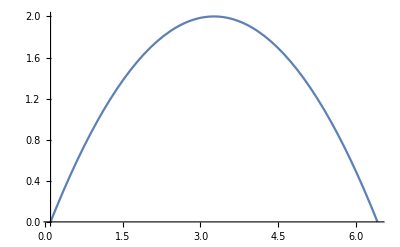

True

{T0→0.873324}

True

{Ts→1.02003}

FindRoot::precw: The precision of the argument function (0.0587729252079707+Log[InterpolatingFunction[«1»][(«7»)^(«4»)]]/Log[10]) is less than WorkingPrecision (16.).

{0.978963,1.1043486225102×10^16,0.860386,1.17754,0.00818119,109.969,112.332,-3.99055×10^-12,2.32439×10^-25,1.13906×10^-47,3.93541×10^-12,-2.31229×10^-25,3.1609×10^-37,1.46801×10^12,8.69826×10^11,1.99534×10^-12,0.0900673,0.00270753,-32.2655}

```mathematica
testdir="cold";
testvw=1;

testCoeffs={.64,0.27,1}(*μ, A, λ*);

testTc=1(*[TeV]*);
testtc=((2*10^(18-3))/testTc^2)(*roughly Hubble time at Tc [TeV^-1]*);

testtab=Table[{x,testTc/5(-(x-1/10-√10)^2+10)},{x,1/10,1/10 (1+20 √10),5./100}];
testTfn=Interpolation[testtab];

Plot[testTfn[x],{x,0.1,6.42455532033676}]

testgstar=10;

(*whether the critical temperature exists*)
cond1[testCoeffs⟦1⟧,testCoeffs⟦2⟧,testCoeffs⟦3⟧]
Tbinodal/.{μ->testCoeffs⟦1⟧,A->testCoeffs⟦2⟧,λ->testCoeffs⟦3⟧,Tc->testTc}

(*whether the spinodal temperature exists*)
cond2[testCoeffs⟦1⟧,testCoeffs⟦2⟧,testCoeffs⟦3⟧]
Tspinodal/.{μ->testCoeffs⟦1⟧,A->testCoeffs⟦2⟧,λ->testCoeffs⟦3⟧,Tc->testTc}


(*{Subscript[T, PT], Subscript[t, PT], λ̄, Subscript[χ, b], ϵ, Subscript[E, c], Subscript[S, E], Subscript[S, E]', Subscript[S, E]'', Subscript[Γ, nucl]/𝒱, Subscript[β, 1], Subscript[β, 2], Subscript[n, b], Subscript[R, b], <R>, Subscript[β, eff], Subscript[α, ∞], Subscript[α, n], Subscript[κ, run]}*)
ptParams[testgstar,testdir,testvw,{testTfn,testtc},testCoeffs,testTc,"numeric",1,True,1,316]

Clear[testgstar,testdir,testvw,testCoeffs,testTc,testtc,testtab,testTfn]
```

#### # Test scale factor

Takes ~40 mins to run

```mathematica
(*Needs["DSReheating`"]*)
```

```mathematica
(*testdir="hot";
testvw=1;

testCoeffs={1,0.82,1}(*μ, A, λ*);

testTc=1(*[TeV]*);
testtc=((2*10^(18-3))/testTc^2)(*roughly Hubble time at Tc [TeV^-1]*);

testtab=Table[{x,testTc/5(-(x-1/10-√10)^2+10)},{x,1/10,1/10 (1+20 √10),5./100}];
testTfn=Interpolation[testtab];

Plot[testTfn[x],{x,0.1,6.42455532033676}]

testgstar=10;

aOfx[0.01,10,1,0,1000,30,20];

{TT,Lh1}=Timing[Lmlnh[testdir,testvw,{testTfn,testtc},testCoeffs,testTc,1,False,aOfx[0.01,10,1,0,1000,30,20],250]];
Print["time = ",TT]

{TT,Lh2}=Timing[Lmlnh[testdir,testvw,{testTfn,testtc},testCoeffs,testTc,1,False,1,250]];
Print["time = ",TT]

Plot[{Lh1[Log10[x]],Lh2[Log10[x]]},{x,1/10,1/10 (1+20 √10)}]

Plot[{Lh1[Log10[x]]/Lh2[Log10[x]]-1},{x,1/10,1/10 (1+20 √10)}]*)
```

```mathematica
(*Clear[testgstar,testdir,testvw,testCoeffs,testTc,testtc,testtab,testTfn,TT,Lh1,Lh2]*)
```

```mathematica
(*2292.458232/3600*)
```